```mathematica
(* initial vectors *)
a=Transpose[{7, 12}];
b=Transpose[{-4, 2}];
```

```mathematica
(* vector 'c' at t = 0, will be equal to the tensor product of vectors 'a' and 'b' *)
c0=Transpose[{a[[1]]*b[[1]], a[[1]]*b[[2]], a[[2]]*b[[1]], a[[2]]*b[[2]]}];
```

```mathematica
(* change matrix *)
h={{0, 0, 0, 0}, {0, -1, 1, 0}, {0, 1, -1, 0}, {0, 0, 0, 0}};
```

```mathematica
(* function describing the evolution of the system *)
evolution[x_]:=MatrixExp[I h x, c0];
```

```mathematica
(* moments of time *)
t=Range[0, 4, 0.001];
```

```mathematica
(* form list containing vectors 'c' at each moment of time *)
c={};
Do [AppendTo[c, evolution[i]], {i, t}];
```

```mathematica
(* form list containing displacement vector 'g' at each moment of time *)
g={};
Do [AppendTo[g, i-c0], {i, c}];
```

```mathematica
(* finding the norm of 'g' vectors *)
gNorm={};
Do[AppendTo[gNorm, Norm[i, 2]], {i, g}];
```

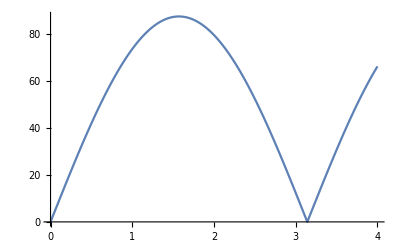

```mathematica
(* plot norms of 'g' *)
ListLinePlot[gNorm, DataRange->{t[[1]],t[[-1]]}]
```

```mathematica
(* function of finding vectors 'a' and 'b' at which the displacement vector 'g' is minimal *)
(* input: vector 'c' coordinates *)
findMinimumAB[c11_,c12_,c21_,c22_]:=FindMinimum[Norm[{c11-a1 b1,c12-a1 b2, c21-a2 b1,  c22-a2 b2},2],{a1, a2, b1, b2}];
```

```mathematica
(* calculating vectors 'a' and 'b' for which the displacement vector 'g' is minimal and writing them to an array 'ab' *)
ab={};
Do [AppendTo[ab, findMinimumAB[i[[1]], i[[2]],i[[3]],i[[4]]]], {i, c}];
```

```mathematica
(* print 'ab' matrix *)
ab // MatrixForm
```

(0.000119954 | {a1→1.90376,a2→3.26357,b1→-14.7078,b2→7.35391}
0.0876812 | {a1→1.90559,a2→3.26673,b1→-14.6936,b2→7.34679}
0.175362 | {a1→1.9055,a2→3.26657,b1→-14.6942,b2→7.34712}
0.263043 | {a1→1.90571,a2→3.26693,b1→-14.6926,b2→7.34628}
0.350723 | {a1→1.90601,a2→3.26743,b1→-14.6902,b2→7.34508}
0.438402 | {a1→1.90602,a2→3.26745,b1→-14.69,b2→7.34496}
0.52608 | {a1→1.89344,a2→3.24587,b1→-14.7875,b2→7.39369}
0.613756 | {a1→1.89387,a2→3.24661,b1→-14.7839,b2→7.39191}
0.701431 | {a1→1.89436,a2→3.24745,b1→-14.7799,b2→7.38988}
0.789104 | {a1→1.89495,a2→3.24845,b1→-14.7751,b2→7.38743}
0.876776 | {a1→1.89566,a2→3.24965,b1→-14.7693,b2→7.38455}
0.964445 | {a1→1.89649,a2→3.25106,b1→-14.7626,b2→7.38117}
1.05211 | {a1→1.89742,a2→3.25266,b1→-14.755,b2→7.37735}
1.13978 | {a1→1.89847,a2→3.25444,b1→-14.7466,b2→7.37309}
1.22744 | {a1→1.89962,a2→3.25641,b1→-14.7373,b2→7.36841}
1.3151 | {a1→1.90087,a2→3.25853,b1→-14.7273,b2→7.36337}
1.40275 | {a1→1.90217,a2→3.26073,b1→-14.7168,b2→7.35812}
1.4904 | {a1→1.905,a2→3.26557,b1→-14.6945,b2→7.34693}
1.57805 | {a1→1.90642,a2→3.268,b1→-14.6831,b2→7.34118}
1.66569 | {a1→1.90794,a2→3.27058,b1→-14.671,b2→7.33507}
1.75333 | {a1→1.90953,a2→3.27329,b1→-14.6583,b2→7.32866}
1.84097 | {a1→1.9112,a2→3.27613,b1→-14.645,b2→7.32196}
1.9286 | {a1→1.91293,a2→3.27908,b1→-14.6312,b2→7.31502}
2.01622 | {a1→1.91472,a2→3.28211,b1→-14.617,b2→7.30787}
2.10384 | {a1→1.91654,a2→3.28522,b1→-14.6025,b2→7.30055}
2.19146 | {a1→1.9184,a2→3.28839,b1→-14.5877,b2→7.29311}
2.27907 | {a1→1.92029,a2→3.29159,b1→-14.5727,b2→7.28558}
2.36667 | {a1→1.92219,a2→3.29482,b1→-14.5577,b2→7.27799}
2.45427 | {a1→1.92408,a2→3.29805,b1→-14.5426,b2→7.27041}
2.54186 | {a1→1.92598,a2→3.30127,b1→-14.5276,b2→7.26283}
2.62945 | {a1→1.92786,a2→3.30447,b1→-14.5127,b2→7.2553}
2.71703 | {a1→1.92972,a2→3.30763,b1→-14.4979,b2→7.24785}
2.8046 | {a1→1.93156,a2→3.31074,b1→-14.4834,b2→7.2405}
2.89217 | {a1→1.93336,a2→3.3138,b1→-14.4691,b2→7.23328}
2.97972 | {a1→1.93512,a2→3.31678,b1→-14.4551,b2→7.22621}
3.06727 | {a1→1.93684,a2→3.3197,b1→-14.4414,b2→7.21929}
3.15482 | {a1→1.93851,a2→3.32253,b1→-14.4281,b2→7.21254}
3.24235 | {a1→1.94014,a2→3.32528,b1→-14.4151,b2→7.20596}
3.32988 | {a1→1.94148,a2→3.32753,b1→-14.4043,b2→7.20045}
3.4174 | {a1→1.94274,a2→3.32966,b1→-14.3939,b2→7.1952}
3.50491 | {a1→1.94398,a2→3.33174,b1→-14.3838,b2→7.19005}
3.59241 | {a1→1.94518,a2→3.33377,b1→-14.3739,b2→7.18501}
3.6799 | {a1→1.94635,a2→3.33574,b1→-14.3642,b2→7.18008}
3.76738 | {a1→1.94749,a2→3.33765,b1→-14.3548,b2→7.17525}
3.85486 | {a1→1.9486,a2→3.3395,b1→-14.3455,b2→7.17054}
3.94232 | {a1→1.94968,a2→3.3413,b1→-14.3366,b2→7.16595}
4.02977 | {a1→1.95071,a2→3.34303,b1→-14.3278,b2→7.16148}
4.11722 | {a1→1.95171,a2→3.34469,b1→-14.3194,b2→7.15714}
4.20465 | {a1→1.95267,a2→3.34629,b1→-14.3112,b2→7.15292}
4.29207 | {a1→1.9536,a2→3.34783,b1→-14.3032,b2→7.14883}
4.37949 | {a1→1.94544,a2→3.3338,b1→-14.362,b2→7.17808}
4.46689 | {a1→1.94606,a2→3.33482,b1→-14.3561,b2→7.17504}
4.55428 | {a1→1.94671,a2→3.33588,b1→-14.3501,b2→7.17192}
4.64166 | {a1→1.94737,a2→3.33695,b1→-14.344,b2→7.16873}
4.72902 | {a1→1.94804,a2→3.33805,b1→-14.3377,b2→7.16548}
4.81638 | {a1→1.94872,a2→3.33916,b1→-14.3314,b2→7.16219}
4.90372 | {a1→1.94941,a2→3.34028,b1→-14.325,b2→7.15886}
4.99105 | {a1→1.9501,a2→3.34141,b1→-14.3185,b2→7.15549}
5.07837 | {a1→1.95079,a2→3.34255,b1→-14.312,b2→7.1521}
5.16568 | {a1→1.95149,a2→3.34368,b1→-14.3055,b2→7.14871}
5.25297 | {a1→1.95218,a2→3.34481,b1→-14.2989,b2→7.14532}
5.34025 | {a1→1.95286,a2→3.34592,b1→-14.2925,b2→7.14193}
5.42752 | {a1→1.95354,a2→3.34702,b1→-14.286,b2→7.13856}
5.51477 | {a1→1.95421,a2→3.3481,b1→-14.2796,b2→7.13521}
5.60201 | {a1→1.95487,a2→3.34917,b1→-14.2732,b2→7.13189}
5.68923 | {a1→1.95552,a2→3.35021,b1→-14.2669,b2→7.1286}
5.77644 | {a1→1.95615,a2→3.35122,b1→-14.2607,b2→7.12535}
5.86364 | {a1→1.95677,a2→3.35222,b1→-14.2546,b2→7.12214}
5.95082 | {a1→1.95736,a2→3.35317,b1→-14.2486,b2→7.11898}
6.03799 | {a1→1.95795,a2→3.35411,b1→-14.2427,b2→7.11586}
6.12514 | {a1→1.95852,a2→3.35501,b1→-14.2369,b2→7.1128}
6.21228 | {a1→1.95906,a2→3.35587,b1→-14.2312,b2→7.1098}
6.2994 | {a1→1.95959,a2→3.3567,b1→-14.2256,b2→7.10685}
6.3865 | {a1→1.9601,a2→3.3575,b1→-14.2202,b2→7.10396}
6.47359 | {a1→1.96058,a2→3.35826,b1→-14.2149,b2→7.10114}
6.56066 | {a1→1.96105,a2→3.35898,b1→-14.2097,b2→7.09838}
6.64772 | {a1→1.96149,a2→3.35966,b1→-14.2047,b2→7.0957}
6.73476 | {a1→1.96191,a2→3.3603,b1→-14.1998,b2→7.09307}
6.82178 | {a1→1.96231,a2→3.3609,b1→-14.1951,b2→7.09052}
6.90879 | {a1→1.96268,a2→3.36146,b1→-14.1905,b2→7.08805}
6.99578 | {a1→1.96302,a2→3.36197,b1→-14.186,b2→7.08565}
7.08275 | {a1→1.96334,a2→3.36244,b1→-14.1818,b2→7.08333}
7.1697 | {a1→1.96364,a2→3.36286,b1→-14.1777,b2→7.0811}
7.25664 | {a1→1.9639,a2→3.36323,b1→-14.1738,b2→7.07895}
7.34355 | {a1→1.96415,a2→3.36356,b1→-14.17,b2→7.07688}
7.43045 | {a1→1.96436,a2→3.36385,b1→-14.1664,b2→7.07488}
7.51733 | {a1→1.96455,a2→3.36409,b1→-14.163,b2→7.07296}
7.60419 | {a1→1.96473,a2→3.3643,b1→-14.1596,b2→7.07109}
7.69104 | {a1→1.96489,a2→3.36449,b1→-14.1563,b2→7.06925}
7.77786 | {a1→1.96505,a2→3.36467,b1→-14.153,b2→7.06739}
7.86466 | {a1→1.96523,a2→3.36489,b1→-14.1496,b2→7.06546}
7.95145 | {a1→1.96546,a2→3.36518,b1→-14.1458,b2→7.06336}
8.03821 | {a1→1.96575,a2→3.36559,b1→-14.1414,b2→7.06097}
8.12496 | {a1→1.96619,a2→3.36624,b1→-14.1361,b2→7.05809}
8.21168 | {a1→1.96422,a2→3.36278,b1→-14.148,b2→7.06381}
8.29838 | {a1→1.96514,a2→3.36426,b1→-14.1391,b2→7.05914}
8.38507 | {a1→1.96621,a2→3.36599,b1→-14.1291,b2→7.05394}
8.47173 | {a1→1.96738,a2→3.3679,b1→-14.1184,b2→7.04835}
8.55837 | {a1→1.96855,a2→3.36981,b1→-14.1076,b2→7.04275}
8.64499 | {a1→1.96956,a2→3.37143,b1→-14.098,b2→7.03774}
8.73159 | {a1→1.97021,a2→3.37243,b1→-14.091,b2→7.03401}
8.81816 | {a1→1.97038,a2→3.37262,b1→-14.0874,b2→7.03195}
8.90472 | {a1→1.97022,a2→3.37225,b1→-14.086,b2→7.03105}
8.99125 | {a1→1.97013,a2→3.37198,b1→-14.0843,b2→7.02992}
9.07776 | {a1→1.97033,a2→3.37223,b1→-14.0803,b2→7.02771}
9.16424 | {a1→1.97057,a2→3.37253,b1→-14.0761,b2→7.02537}
9.25071 | {a1→1.9709,a2→3.37299,b1→-14.0712,b2→7.02266}
9.33715 | {a1→1.97149,a2→3.37389,b1→-14.0644,b2→7.01904}
9.42357 | {a1→1.98015,a2→3.38859,b1→-14.0004,b2→6.98684}
9.50996 | {a1→1.98084,a2→3.38965,b1→-13.9929,b2→6.98286}
9.59633 | {a1→1.98115,a2→3.39008,b1→-13.9881,b2→6.98018}
9.68268 | {a1→1.98102,a2→3.38974,b1→-13.9864,b2→6.97907}
9.769 | {a1→1.9806,a2→3.3889,b1→-13.9867,b2→6.97897}
9.8553 | {a1→1.98007,a2→3.38788,b1→-13.9878,b2→6.97924}
9.94157 | {a1→1.97956,a2→3.38689,b1→-13.9887,b2→6.97941}
10.0278 | {a1→1.97914,a2→3.38605,b1→-13.9889,b2→6.97926}
10.114 | {a1→1.97882,a2→3.38538,b1→-13.9884,b2→6.97875}
10.2002 | {a1→1.97858,a2→3.38485,b1→-13.9873,b2→6.97795}
10.2864 | {a1→1.97839,a2→3.38441,b1→-13.9859,b2→6.97693}
10.3726 | {a1→1.97823,a2→3.38401,b1→-13.9842,b2→6.97581}
10.4587 | {a1→1.97808,a2→3.38362,b1→-13.9824,b2→6.97465}
10.5448 | {a1→1.97791,a2→3.3832,b1→-13.9808,b2→6.97354}
10.6308 | {a1→1.9777,a2→3.38272,b1→-13.9793,b2→6.97254}
10.7169 | {a1→1.97746,a2→3.38217,b1→-13.9781,b2→6.97166}
10.8029 | {a1→1.97721,a2→3.38162,b1→-13.9769,b2→6.97077}
10.8889 | {a1→1.97724,a2→3.38155,b1→-13.9737,b2→6.96888}
10.9749 | {a1→1.97839,a2→3.38338,b1→-13.9627,b2→6.96306}
11.0608 | {a1→1.97803,a2→3.38264,b1→-13.9622,b2→6.96252}
11.1467 | {a1→1.97716,a2→3.38101,b1→-13.9653,b2→6.96378}
11.2326 | {a1→1.97465,a2→3.37657,b1→-13.98,b2→6.97081}
11.3184 | {a1→1.97573,a2→3.37829,b1→-13.9693,b2→6.96514}
11.4042 | {a1→1.97719,a2→3.38064,b1→-13.9559,b2→6.95816}
11.49 | {a1→1.97739,a2→3.38086,b1→-13.9513,b2→6.95556}
11.5758 | {a1→1.97708,a2→3.38017,b1→-13.9504,b2→6.9548}
11.6615 | {a1→1.97666,a2→3.37933,b1→-13.9501,b2→6.95435}
11.7473 | {a1→1.97628,a2→3.37852,b1→-13.9497,b2→6.9538}
11.8329 | {a1→1.97591,a2→3.37776,b1→-13.949,b2→6.95315}
11.9186 | {a1→1.97557,a2→3.37703,b1→-13.9482,b2→6.95241}
12.0042 | {a1→1.97526,a2→3.37635,b1→-13.9471,b2→6.95156}
12.0898 | {a1→1.97534,a2→3.37634,b1→-13.9433,b2→6.9493}
12.1753 | {a1→1.97516,a2→3.37589,b1→-13.9412,b2→6.94794}
12.2609 | {a1→1.975,a2→3.37547,b1→-13.939,b2→6.94651}
12.3464 | {a1→1.97485,a2→3.37506,b1→-13.9367,b2→6.94504}
12.4318 | {a1→1.97471,a2→3.37467,b1→-13.9344,b2→6.94351}
12.5173 | {a1→1.97457,a2→3.37427,b1→-13.932,b2→6.94197}
12.6027 | {a1→1.97443,a2→3.37388,b1→-13.9295,b2→6.9404}
12.6881 | {a1→1.97429,a2→3.37348,b1→-13.9271,b2→6.93883}
12.7734 | {a1→1.97414,a2→3.37308,b1→-13.9246,b2→6.93726}
12.8587 | {a1→1.965,a2→3.3573,b1→-13.9859,b2→6.96743}
12.944 | {a1→1.96587,a2→3.35862,b1→-13.9762,b2→6.96224}
13.0292 | {a1→1.96665,a2→3.3598,b1→-13.9671,b2→6.95736}
13.1145 | {a1→1.96734,a2→3.36082,b1→-13.9586,b2→6.95276}
13.1996 | {a1→1.96795,a2→3.36169,b1→-13.9507,b2→6.94847}
13.2848 | {a1→1.96847,a2→3.36242,b1→-13.9434,b2→6.94446}
13.3699 | {a1→1.9689,a2→3.36299,b1→-13.9367,b2→6.94075}
13.455 | {a1→1.96925,a2→3.36343,b1→-13.9306,b2→6.93731}
13.54 | {a1→1.96953,a2→3.36373,b1→-13.9249,b2→6.93414}
13.6251 | {a1→1.96972,a2→3.3639,b1→-13.9198,b2→6.93122}
13.71 | {a1→1.96985,a2→3.36394,b1→-13.9152,b2→6.92853}
13.795 | {a1→1.96991,a2→3.36387,b1→-13.9111,b2→6.92608}
13.8799 | {a1→1.9699,a2→3.36369,b1→-13.9073,b2→6.92383}
13.9648 | {a1→1.96983,a2→3.3634,b1→-13.904,b2→6.9218}
14.0496 | {a1→1.9697,a2→3.363,b1→-13.9011,b2→6.91997}
14.1344 | {a1→1.96952,a2→3.36251,b1→-13.8986,b2→6.9183}
14.2192 | {a1→1.96928,a2→3.36193,b1→-13.8964,b2→6.91682}
14.304 | {a1→1.96899,a2→3.36125,b1→-13.8946,b2→6.9155}
14.3887 | {a1→1.96074,a2→3.34699,b1→-13.9491,b2→6.94225}
14.4733 | {a1→1.96023,a2→3.34594,b1→-13.9488,b2→6.94167}
14.558 | {a1→1.95969,a2→3.34484,b1→-13.9487,b2→6.94121}
14.6426 | {a1→1.95911,a2→3.34366,b1→-13.9488,b2→6.94086}
14.7271 | {a1→1.95849,a2→3.34243,b1→-13.9492,b2→6.94063}
14.8116 | {a1→1.95784,a2→3.34113,b1→-13.9498,b2→6.9405}
14.8961 | {a1→1.9574,a2→3.34019,b1→-13.9489,b2→6.93963}
14.9806 | {a1→1.95668,a2→3.33877,b1→-13.9499,b2→6.93973}
15.065 | {a1→1.95593,a2→3.3373,b1→-13.9512,b2→6.93992}
15.1494 | {a1→1.95515,a2→3.33579,b1→-13.9526,b2→6.94019}
15.2337 | {a1→1.95435,a2→3.33422,b1→-13.9542,b2→6.94054}
15.318 | {a1→1.95351,a2→3.3326,b1→-13.956,b2→6.94099}
15.4023 | {a1→1.95265,a2→3.33094,b1→-13.9579,b2→6.94151}
15.4865 | {a1→1.95177,a2→3.32924,b1→-13.96,b2→6.94211}
15.5707 | {a1→1.95086,a2→3.3275,b1→-13.9622,b2→6.94276}
15.6548 | {a1→1.94993,a2→3.32571,b1→-13.9646,b2→6.9435}
15.7389 | {a1→1.94898,a2→3.32389,b1→-13.9671,b2→6.9443}
15.823 | {a1→1.94801,a2→3.32203,b1→-13.9698,b2→6.94516}
15.907 | {a1→1.94702,a2→3.32015,b1→-13.9725,b2→6.94606}
15.991 | {a1→1.94601,a2→3.31822,b1→-13.9754,b2→6.94703}
16.075 | {a1→1.94498,a2→3.31627,b1→-13.9784,b2→6.94804}
16.1589 | {a1→1.94394,a2→3.31428,b1→-13.9815,b2→6.9491}
16.2428 | {a1→1.94288,a2→3.31227,b1→-13.9846,b2→6.95021}
16.3266 | {a1→1.94181,a2→3.31024,b1→-13.9879,b2→6.95134}
16.4104 | {a1→1.94072,a2→3.30818,b1→-13.9912,b2→6.95252}
16.4941 | {a1→1.93962,a2→3.30609,b1→-13.9946,b2→6.95373}
16.5779 | {a1→1.93851,a2→3.30399,b1→-13.9981,b2→6.95498}
16.6615 | {a1→1.93739,a2→3.30186,b1→-14.0017,b2→6.95625}
16.7452 | {a1→1.93625,a2→3.29971,b1→-14.0053,b2→6.95755}
16.8287 | {a1→1.93511,a2→3.29755,b1→-14.0089,b2→6.95888}
16.9123 | {a1→1.93396,a2→3.29537,b1→-14.0126,b2→6.96021}
16.9958 | {a1→1.9328,a2→3.29317,b1→-14.0164,b2→6.96158}
17.0793 | {a1→1.93163,a2→3.29096,b1→-14.0202,b2→6.96295}
17.1627 | {a1→1.93045,a2→3.28874,b1→-14.024,b2→6.96434}
17.2461 | {a1→1.92927,a2→3.2865,b1→-14.0279,b2→6.96574}
17.3294 | {a1→1.92808,a2→3.28426,b1→-14.0317,b2→6.96715}
17.4127 | {a1→1.92689,a2→3.282,b1→-14.0357,b2→6.96857}
17.4959 | {a1→1.92569,a2→3.27974,b1→-14.0395,b2→6.96998}
17.5791 | {a1→1.92449,a2→3.27747,b1→-14.0435,b2→6.9714}
17.6623 | {a1→1.92328,a2→3.27518,b1→-14.0474,b2→6.97284}
17.7454 | {a1→1.92207,a2→3.27289,b1→-14.0514,b2→6.97427}
17.8285 | {a1→1.92086,a2→3.2706,b1→-14.0553,b2→6.97568}
17.9115 | {a1→1.91965,a2→3.2683,b1→-14.0593,b2→6.9771}
17.9945 | {a1→1.91843,a2→3.266,b1→-14.0632,b2→6.97851}
18.0775 | {a1→1.91722,a2→3.2637,b1→-14.0672,b2→6.97992}
18.1603 | {a1→1.916,a2→3.26139,b1→-14.0711,b2→6.98131}
18.2432 | {a1→1.91478,a2→3.25908,b1→-14.075,b2→6.98269}
18.326 | {a1→1.91357,a2→3.25677,b1→-14.0789,b2→6.98406}
18.4088 | {a1→1.91235,a2→3.25447,b1→-14.0827,b2→6.98541}
18.4915 | {a1→1.91113,a2→3.25216,b1→-14.0866,b2→6.98676}
18.5742 | {a1→1.90992,a2→3.24985,b1→-14.0904,b2→6.98808}
18.6568 | {a1→1.90871,a2→3.24755,b1→-14.0942,b2→6.98938}
18.7394 | {a1→1.9075,a2→3.24524,b1→-14.0979,b2→6.99066}
18.8219 | {a1→1.9063,a2→3.24295,b1→-14.1016,b2→6.99192}
18.9044 | {a1→1.90509,a2→3.24065,b1→-14.1053,b2→6.99316}
18.9868 | {a1→1.90389,a2→3.23837,b1→-14.1089,b2→6.99436}
19.0692 | {a1→1.9027,a2→3.23608,b1→-14.1125,b2→6.99555}
19.1516 | {a1→1.90151,a2→3.2338,b1→-14.1161,b2→6.99671}
19.2339 | {a1→1.90032,a2→3.23153,b1→-14.1196,b2→6.99784}
19.3161 | {a1→1.89914,a2→3.22927,b1→-14.123,b2→6.99894}
19.3983 | {a1→1.89796,a2→3.22701,b1→-14.1264,b2→7.00001}
19.4805 | {a1→1.89679,a2→3.22476,b1→-14.1297,b2→7.00104}
19.5626 | {a1→1.89562,a2→3.22252,b1→-14.133,b2→7.00204}
19.6447 | {a1→1.89446,a2→3.22029,b1→-14.1362,b2→7.00301}
19.7267 | {a1→1.89331,a2→3.21807,b1→-14.1393,b2→7.00394}
19.8087 | {a1→1.89216,a2→3.21585,b1→-14.1424,b2→7.00485}
19.8906 | {a1→1.89102,a2→3.21365,b1→-14.1454,b2→7.00571}
19.9724 | {a1→1.88988,a2→3.21145,b1→-14.1484,b2→7.00654}
20.0543 | {a1→1.88875,a2→3.20927,b1→-14.1512,b2→7.00733}
20.136 | {a1→1.88763,a2→3.2071,b1→-14.1541,b2→7.00807}
20.2178 | {a1→1.88651,a2→3.20493,b1→-14.1568,b2→7.00879}
20.2994 | {a1→1.88541,a2→3.20278,b1→-14.1595,b2→7.00946}
20.3811 | {a1→1.8843,a2→3.20064,b1→-14.1621,b2→7.01009}
20.4626 | {a1→1.88321,a2→3.19851,b1→-14.1646,b2→7.01069}
20.5441 | {a1→1.88212,a2→3.19638,b1→-14.1671,b2→7.01125}
20.6256 | {a1→1.88105,a2→3.19428,b1→-14.1694,b2→7.01175}
20.707 | {a1→1.87997,a2→3.19218,b1→-14.1718,b2→7.01223}
20.7884 | {a1→1.87891,a2→3.1901,b1→-14.174,b2→7.01266}
20.8697 | {a1→1.87785,a2→3.18802,b1→-14.1762,b2→7.01305}
20.951 | {a1→1.8768,a2→3.18595,b1→-14.1783,b2→7.01341}
21.0322 | {a1→1.87576,a2→3.1839,b1→-14.1803,b2→7.01372}
21.1134 | {a1→1.87472,a2→3.18186,b1→-14.1822,b2→7.01399}
21.1945 | {a1→1.8737,a2→3.17983,b1→-14.1841,b2→7.01422}
21.2756 | {a1→1.87268,a2→3.17781,b1→-14.1859,b2→7.01441}
21.3566 | {a1→1.87166,a2→3.1758,b1→-14.1876,b2→7.01456}
21.4375 | {a1→1.87066,a2→3.17381,b1→-14.1892,b2→7.01465}
21.5184 | {a1→1.86966,a2→3.17181,b1→-14.1909,b2→7.01474}
21.5993 | {a1→1.86867,a2→3.16984,b1→-14.1923,b2→7.01475}
21.6801 | {a1→1.86768,a2→3.16787,b1→-14.1938,b2→7.01475}
21.7608 | {a1→1.8667,a2→3.16592,b1→-14.1951,b2→7.0147}
21.8415 | {a1→1.8656,a2→3.16375,b1→-14.1974,b2→7.01509}
21.9222 | {a1→1.86447,a2→3.16153,b1→-14.1999,b2→7.01561}
22.0028 | {a1→1.86334,a2→3.15932,b1→-14.2024,b2→7.01607}
22.0833 | {a1→1.86222,a2→3.15712,b1→-14.2047,b2→7.0165}
22.1638 | {a1→1.86111,a2→3.15493,b1→-14.207,b2→7.01687}
22.2442 | {a1→1.86001,a2→3.15276,b1→-14.2092,b2→7.01721}
22.3246 | {a1→1.85892,a2→3.1506,b1→-14.2113,b2→7.01749}
22.4049 | {a1→1.85784,a2→3.14846,b1→-14.2133,b2→7.01774}
22.4851 | {a1→1.85676,a2→3.14633,b1→-14.2153,b2→7.01793}
22.5653 | {a1→1.8557,a2→3.14421,b1→-14.2171,b2→7.01807}
22.6455 | {a1→1.85464,a2→3.14211,b1→-14.2189,b2→7.01816}
22.7256 | {a1→1.85359,a2→3.14002,b1→-14.2206,b2→7.01822}
22.8056 | {a1→1.85255,a2→3.13794,b1→-14.2222,b2→7.01823}
22.8856 | {a1→1.85152,a2→3.13588,b1→-14.2236,b2→7.01818}
22.9656 | {a1→1.85051,a2→3.13383,b1→-14.2251,b2→7.01809}
23.0454 | {a1→1.84949,a2→3.13179,b1→-14.2264,b2→7.01795}
23.1252 | {a1→1.84849,a2→3.12977,b1→-14.2276,b2→7.01776}
23.205 | {a1→1.84749,a2→3.12776,b1→-14.2288,b2→7.01754}
23.2847 | {a1→1.84651,a2→3.12577,b1→-14.2299,b2→7.01725}
23.3644 | {a1→1.84553,a2→3.12378,b1→-14.2309,b2→7.01694}
23.444 | {a1→1.84456,a2→3.12182,b1→-14.2318,b2→7.01656}
23.5235 | {a1→1.84361,a2→3.11986,b1→-14.2326,b2→7.01613}
23.603 | {a1→1.84265,a2→3.11792,b1→-14.2333,b2→7.01566}
23.6824 | {a1→1.84171,a2→3.11599,b1→-14.234,b2→7.01515}
23.7617 | {a1→1.84078,a2→3.11408,b1→-14.2345,b2→7.01458}
23.8411 | {a1→1.83986,a2→3.11218,b1→-14.235,b2→7.01396}
23.9203 | {a1→1.83895,a2→3.1103,b1→-14.2353,b2→7.0133}
23.9995 | {a1→1.83804,a2→3.10842,b1→-14.2356,b2→7.01259}
24.0786 | {a1→1.83715,a2→3.10657,b1→-14.2358,b2→7.01181}
24.1577 | {a1→1.83626,a2→3.10473,b1→-14.2359,b2→7.01101}
24.2367 | {a1→1.83539,a2→3.1029,b1→-14.2359,b2→7.01013}
24.3157 | {a1→1.83452,a2→3.10108,b1→-14.2358,b2→7.00923}
24.3946 | {a1→1.83366,a2→3.09929,b1→-14.2356,b2→7.00826}
24.4734 | {a1→1.83281,a2→3.0975,b1→-14.2354,b2→7.00725}
24.5522 | {a1→1.83197,a2→3.09573,b1→-14.235,b2→7.00618}
24.6309 | {a1→1.83115,a2→3.09398,b1→-14.2345,b2→7.00504}
24.7095 | {a1→1.83033,a2→3.09223,b1→-14.234,b2→7.00389}
24.7881 | {a1→1.82952,a2→3.09051,b1→-14.2333,b2→7.00266}
24.8667 | {a1→1.82872,a2→3.08879,b1→-14.2326,b2→7.00141}
24.9452 | {a1→1.82793,a2→3.08709,b1→-14.2318,b2→7.00009}
25.0236 | {a1→1.82714,a2→3.08541,b1→-14.2308,b2→6.99872}
25.1019 | {a1→1.82637,a2→3.08374,b1→-14.2298,b2→6.99729}
25.1802 | {a1→1.82561,a2→3.08209,b1→-14.2287,b2→6.99581}
25.2585 | {a1→1.82487,a2→3.08046,b1→-14.2274,b2→6.99427}
25.3366 | {a1→1.82413,a2→3.07883,b1→-14.2261,b2→6.99269}
25.4147 | {a1→1.8234,a2→3.07723,b1→-14.2247,b2→6.99103}
25.4928 | {a1→1.82268,a2→3.07564,b1→-14.2231,b2→6.98934}
25.5708 | {a1→1.82197,a2→3.07407,b1→-14.2215,b2→6.98757}
25.6487 | {a1→1.82128,a2→3.07252,b1→-14.2198,b2→6.98576}
25.7266 | {a1→1.8206,a2→3.07099,b1→-14.2179,b2→6.98388}
25.8044 | {a1→1.81992,a2→3.06947,b1→-14.2159,b2→6.98195}
25.8821 | {a1→1.81926,a2→3.06796,b1→-14.2139,b2→6.97997}
25.9598 | {a1→1.82823,a2→3.0827,b1→-14.1369,b2→6.94119}
26.0374 | {a1→1.82608,a2→3.07869,b1→-14.1463,b2→6.94482}
26.115 | {a1→1.82395,a2→3.0747,b1→-14.1555,b2→6.94838}
26.1925 | {a1→1.82185,a2→3.07077,b1→-14.1646,b2→6.95182}
26.2699 | {a1→1.81977,a2→3.06687,b1→-14.1734,b2→6.95516}
26.3472 | {a1→1.81773,a2→3.06302,b1→-14.182,b2→6.95837}
26.4245 | {a1→1.8157,a2→3.05921,b1→-14.1904,b2→6.96151}
26.5018 | {a1→1.81371,a2→3.05545,b1→-14.1986,b2→6.96451}
26.579 | {a1→1.81174,a2→3.05172,b1→-14.2066,b2→6.96742}
26.6561 | {a1→1.8098,a2→3.04806,b1→-14.2144,b2→6.97019}
26.7331 | {a1→1.80788,a2→3.04443,b1→-14.222,b2→6.97287}
26.8101 | {a1→1.806,a2→3.04085,b1→-14.2293,b2→6.97542}
26.887 | {a1→1.80415,a2→3.03732,b1→-14.2364,b2→6.97784}
26.9639 | {a1→1.80164,a2→3.03269,b1→-14.2486,b2→6.98279}
27.0406 | {a1→1.79985,a2→3.02926,b1→-14.2552,b2→6.98496}
27.1174 | {a1→1.79806,a2→3.02582,b1→-14.2618,b2→6.98713}
27.194 | {a1→1.79633,a2→3.0225,b1→-14.2679,b2→6.98904}
27.2706 | {a1→1.79463,a2→3.01922,b1→-14.2737,b2→6.99082}
27.3471 | {a1→1.57037,a2→2.64156,b1→-16.3034,b2→7.98364}
27.4236 | {a1→1.57406,a2→2.6474,b1→-16.2564,b2→7.95936}
27.5 | {a1→1.57766,a2→2.65308,b1→-16.2105,b2→7.93566}
27.5763 | {a1→1.58117,a2→2.6586,b1→-16.1658,b2→7.91251}
27.6526 | {a1→1.58459,a2→2.66397,b1→-16.1221,b2→7.88989}
27.7288 | {a1→1.58793,a2→2.6692,b1→-16.0795,b2→7.86776}
27.8049 | {a1→1.59119,a2→2.67429,b1→-16.0378,b2→7.8461}
27.8809 | {a1→1.59437,a2→2.67925,b1→-15.997,b2→7.82489}
27.9569 | {a1→1.59748,a2→2.68408,b1→-15.9571,b2→7.8041}
28.0329 | {a1→1.60052,a2→2.68879,b1→-15.918,b2→7.78372}
28.1087 | {a1→1.61787,a2→2.71754,b1→-15.7386,b2→7.69472}
28.1845 | {a1→1.61983,a2→2.72042,b1→-15.7109,b2→7.6799}
28.2602 | {a1→1.62176,a2→2.72326,b1→-15.6835,b2→7.66521}
28.3359 | {a1→1.62368,a2→2.72607,b1→-15.6562,b2→7.65061}
28.4115 | {a1→1.62559,a2→2.72887,b1→-15.6291,b2→7.63606}
28.487 | {a1→1.62749,a2→2.73165,b1→-15.6021,b2→7.62158}
28.5625 | {a1→1.62938,a2→2.73441,b1→-15.5752,b2→7.60716}
28.6379 | {a1→1.63127,a2→2.73715,b1→-15.5485,b2→7.59281}
28.7132 | {a1→1.63314,a2→2.73987,b1→-15.5219,b2→7.57851}
28.7884 | {a1→1.63501,a2→2.74257,b1→-15.4954,b2→7.56427}
28.8636 | {a1→1.63687,a2→2.74526,b1→-15.4691,b2→7.55009}
28.9387 | {a1→1.63871,a2→2.74793,b1→-15.4428,b2→7.53597}
29.0137 | {a1→1.64055,a2→2.75058,b1→-15.4167,b2→7.5219}
29.0887 | {a1→1.64239,a2→2.75321,b1→-15.3907,b2→7.50789}
29.1636 | {a1→1.64421,a2→2.75583,b1→-15.3649,b2→7.49394}
29.2384 | {a1→1.64602,a2→2.75843,b1→-15.3391,b2→7.48004}
29.3132 | {a1→1.64783,a2→2.76101,b1→-15.3135,b2→7.46619}
29.3879 | {a1→1.64963,a2→2.76357,b1→-15.288,b2→7.4524}
29.4625 | {a1→1.65142,a2→2.76612,b1→-15.2626,b2→7.43866}
29.5371 | {a1→1.6532,a2→2.76865,b1→-15.2373,b2→7.42498}
29.6116 | {a1→1.65498,a2→2.77116,b1→-15.2122,b2→7.41134}
29.686 | {a1→1.65674,a2→2.77366,b1→-15.1871,b2→7.39775}
29.7603 | {a1→1.6585,a2→2.77614,b1→-15.1621,b2→7.38422}
29.8346 | {a1→1.66026,a2→2.77861,b1→-15.1373,b2→7.37072}
29.9088 | {a1→1.662,a2→2.78106,b1→-15.1125,b2→7.35728}
29.9829 | {a1→1.66374,a2→2.78349,b1→-15.0879,b2→7.34389}
30.057 | {a1→1.66547,a2→2.78591,b1→-15.0633,b2→7.33053}
30.1309 | {a1→1.66719,a2→2.78831,b1→-15.0389,b2→7.31722}
30.2049 | {a1→1.66891,a2→2.7907,b1→-15.0146,b2→7.30396}
30.2787 | {a1→1.67062,a2→2.79308,b1→-14.9903,b2→7.29073}
30.3525 | {a1→1.67233,a2→2.79544,b1→-14.9661,b2→7.27755}
30.4262 | {a1→1.67403,a2→2.79779,b1→-14.942,b2→7.2644}
30.4998 | {a1→1.67572,a2→2.80012,b1→-14.918,b2→7.2513}
30.5733 | {a1→1.67741,a2→2.80244,b1→-14.8941,b2→7.23822}
30.6468 | {a1→1.67909,a2→2.80475,b1→-14.8703,b2→7.22519}
30.7202 | {a1→1.68077,a2→2.80705,b1→-14.8465,b2→7.21218}
30.7936 | {a1→1.68244,a2→2.80933,b1→-14.8228,b2→7.19921}
30.8668 | {a1→1.68411,a2→2.81161,b1→-14.7992,b2→7.18627}
30.94 | {a1→1.68577,a2→2.81387,b1→-14.7756,b2→7.17337}
31.0131 | {a1→1.68743,a2→2.81612,b1→-14.7522,b2→7.16049}
31.0862 | {a1→1.68909,a2→2.81836,b1→-14.7288,b2→7.14763}
31.1591 | {a1→1.69074,a2→2.82059,b1→-14.7054,b2→7.13482}
31.232 | {a1→1.69239,a2→2.82282,b1→-14.6821,b2→7.12201}
31.3048 | {a1→1.69404,a2→2.82503,b1→-14.6589,b2→7.10924}
31.3776 | {a1→1.69568,a2→2.82723,b1→-14.6357,b2→7.0965}
31.4503 | {a1→1.84137,a2→3.06955,b1→-13.4695,b2→6.52962}
31.5228 | {a1→1.83996,a2→3.06662,b1→-13.4715,b2→6.52919}
31.5954 | {a1→1.83872,a2→3.06397,b1→-13.4723,b2→6.52814}
31.6678 | {a1→1.83765,a2→3.06158,b1→-13.4719,b2→6.52651}
31.7402 | {a1→1.83672,a2→3.05943,b1→-13.4704,b2→6.52435}
31.8125 | {a1→1.83594,a2→3.05754,b1→-13.4677,b2→6.52161}
31.8847 | {a1→1.83531,a2→3.05589,b1→-13.464,b2→6.51836}
31.9569 | {a1→1.83482,a2→3.05446,b1→-13.4592,b2→6.51459}
32.0289 | {a1→1.83446,a2→3.05325,b1→-13.4534,b2→6.51033}
32.1009 | {a1→1.83423,a2→3.05226,b1→-13.4467,b2→6.50562}
32.1728 | {a1→1.83412,a2→3.05145,b1→-13.4391,b2→6.50046}
32.2447 | {a1→1.83413,a2→3.05085,b1→-13.4306,b2→6.49486}
32.3165 | {a1→1.83425,a2→3.05043,b1→-13.4213,b2→6.48886}
32.3881 | {a1→1.83448,a2→3.05017,b1→-13.4112,b2→6.48248}
32.4598 | {a1→1.83423,a2→3.04913,b1→-13.4046,b2→6.47774}
32.5313 | {a1→1.83378,a2→3.04775,b1→-13.3994,b2→6.47371}
32.6028 | {a1→1.83344,a2→3.04654,b1→-13.3934,b2→6.46932}
32.6741 | {a1→1.83318,a2→3.04548,b1→-13.3868,b2→6.46457}
32.7455 | {a1→1.83303,a2→3.04457,b1→-13.3794,b2→6.45948}
32.8167 | {a1→1.83295,a2→3.0438,b1→-13.3715,b2→6.45407}
32.8878 | {a1→1.83296,a2→3.04315,b1→-13.3629,b2→6.44838}
32.9589 | {a1→1.83304,a2→3.04263,b1→-13.3538,b2→6.4424}
33.0299 | {a1→1.83319,a2→3.04222,b1→-13.3441,b2→6.43617}
33.1008 | {a1→1.83341,a2→3.04192,b1→-13.334,b2→6.42971}
33.1717 | {a1→1.83368,a2→3.0417,b1→-13.3235,b2→6.42302}
33.2425 | {a1→1.83401,a2→3.04158,b1→-13.3125,b2→6.41614}
33.3131 | {a1→1.83439,a2→3.04154,b1→-13.3012,b2→6.40906}
33.3838 | {a1→1.83482,a2→3.04156,b1→-13.2895,b2→6.40182}
33.4543 | {a1→1.83528,a2→3.04165,b1→-13.2775,b2→6.39443}
33.5247 | {a1→1.83578,a2→3.04179,b1→-13.2653,b2→6.38691}
33.5951 | {a1→1.83632,a2→3.04199,b1→-13.2528,b2→6.37926}
33.6654 | {a1→1.83689,a2→3.04223,b1→-13.2402,b2→6.3715}
33.7356 | {a1→1.83748,a2→3.0425,b1→-13.2273,b2→6.36365}
33.8058 | {a1→1.83809,a2→3.04281,b1→-13.2143,b2→6.35571}
33.8758 | {a1→1.83872,a2→3.04315,b1→-13.2011,b2→6.3477}
33.9458 | {a1→1.83937,a2→3.04351,b1→-13.1878,b2→6.33963}
34.0157 | {a1→1.84003,a2→3.04388,b1→-13.1745,b2→6.33151}
34.0855 | {a1→1.84071,a2→3.04428,b1→-13.161,b2→6.32332}
34.1553 | {a1→1.8414,a2→3.04469,b1→-13.1474,b2→6.3151}
34.2249 | {a1→1.84209,a2→3.0451,b1→-13.1338,b2→6.30685}
34.2945 | {a1→1.8428,a2→3.04553,b1→-13.1202,b2→6.29855}
34.364 | {a1→1.84351,a2→3.04597,b1→-13.1065,b2→6.29023}
34.4334 | {a1→1.84423,a2→3.04641,b1→-13.0927,b2→6.28188}
34.5028 | {a1→1.84495,a2→3.04686,b1→-13.0789,b2→6.2735}
34.572 | {a1→1.84568,a2→3.0473,b1→-13.0651,b2→6.2651}
34.6412 | {a1→1.84642,a2→3.04775,b1→-13.0512,b2→6.25668}
34.7103 | {a1→1.84716,a2→3.04821,b1→-13.0373,b2→6.24823}
34.7793 | {a1→1.8479,a2→3.04867,b1→-13.0234,b2→6.23976}
34.8483 | {a1→1.65268,a2→2.7259,b1→-14.5521,b2→6.97018}
34.9171 | {a1→1.65354,a2→2.72663,b1→-14.5347,b2→6.95986}
34.9859 | {a1→1.65444,a2→2.7274,b1→-14.5172,b2→6.94941}
35.0546 | {a1→1.65536,a2→2.72822,b1→-14.4994,b2→6.93884}
35.1232 | {a1→1.65632,a2→2.72909,b1→-14.4813,b2→6.92811}
35.1917 | {a1→1.65731,a2→2.73,b1→-14.4629,b2→6.91728}
35.2602 | {a1→1.65833,a2→2.73096,b1→-14.4443,b2→6.9063}
35.3286 | {a1→1.65938,a2→2.73197,b1→-14.4254,b2→6.89519}
35.3968 | {a1→1.66046,a2→2.73301,b1→-14.4064,b2→6.88397}
35.465 | {a1→1.66157,a2→2.7341,b1→-14.3871,b2→6.87264}
35.5332 | {a1→1.6627,a2→2.73523,b1→-14.3675,b2→6.86119}
35.6012 | {a1→1.66387,a2→2.73641,b1→-14.3477,b2→6.84961}
35.6692 | {a1→1.66507,a2→2.73763,b1→-14.3277,b2→6.8379}
35.737 | {a1→1.6663,a2→2.7389,b1→-14.3074,b2→6.82606}
35.8048 | {a1→1.66757,a2→2.74022,b1→-14.2868,b2→6.81409}
35.8725 | {a1→1.66887,a2→2.74159,b1→-14.266,b2→6.802}
35.9401 | {a1→1.6702,a2→2.743,b1→-14.245,b2→6.78977}
36.0077 | {a1→1.67156,a2→2.74447,b1→-14.2237,b2→6.77742}
36.0751 | {a1→1.67296,a2→2.74598,b1→-14.2021,b2→6.76494}
36.1425 | {a1→1.6744,a2→2.74755,b1→-14.1803,b2→6.75232}
36.2098 | {a1→1.67586,a2→2.74916,b1→-14.1582,b2→6.73959}
36.277 | {a1→1.67736,a2→2.75082,b1→-14.1359,b2→6.72673}
36.3441 | {a1→1.6789,a2→2.75254,b1→-14.1133,b2→6.71373}
36.4112 | {a1→1.68046,a2→2.75429,b1→-14.0905,b2→6.70062}
36.4781 | {a1→1.68206,a2→2.7561,b1→-14.0674,b2→6.68739}
36.545 | {a1→1.6837,a2→2.75796,b1→-14.0441,b2→6.67403}
36.6118 | {a1→1.68537,a2→2.75987,b1→-14.0206,b2→6.66055}
36.6785 | {a1→1.68707,a2→2.76183,b1→-13.9968,b2→6.64694}
36.7451 | {a1→1.68881,a2→2.76383,b1→-13.9727,b2→6.63322}
36.8116 | {a1→1.69058,a2→2.76589,b1→-13.9485,b2→6.61938}
36.8781 | {a1→1.69239,a2→2.76799,b1→-13.924,b2→6.60542}
36.9444 | {a1→1.69423,a2→2.77014,b1→-13.8993,b2→6.59135}
37.0107 | {a1→1.69611,a2→2.77235,b1→-13.8743,b2→6.57716}
37.0769 | {a1→1.69801,a2→2.7746,b1→-13.8491,b2→6.56285}
37.143 | {a1→1.69996,a2→2.77689,b1→-13.8237,b2→6.54844}
37.209 | {a1→1.70193,a2→2.77924,b1→-13.7981,b2→6.53391}
37.275 | {a1→1.70395,a2→2.78163,b1→-13.7723,b2→6.51928}
37.3408 | {a1→1.70599,a2→2.78408,b1→-13.7462,b2→6.50453}
37.4066 | {a1→1.70807,a2→2.78656,b1→-13.72,b2→6.48969}
37.4722 | {a1→1.71018,a2→2.7891,b1→-13.6935,b2→6.47473}
37.5378 | {a1→1.71233,a2→2.79168,b1→-13.6669,b2→6.45968}
37.6033 | {a1→1.71451,a2→2.79431,b1→-13.64,b2→6.44452}
37.6688 | {a1→1.71672,a2→2.79699,b1→-13.613,b2→6.42926}
37.7341 | {a1→1.71897,a2→2.79971,b1→-13.5857,b2→6.41392}
37.7993 | {a1→1.72124,a2→2.80247,b1→-13.5583,b2→6.39848}
37.8645 | {a1→1.72355,a2→2.80527,b1→-13.5307,b2→6.38295}
37.9296 | {a1→1.72589,a2→2.80812,b1→-13.503,b2→6.36733}
37.9945 | {a1→1.72827,a2→2.81101,b1→-13.475,b2→6.35163}
38.0594 | {a1→1.73067,a2→2.81394,b1→-13.4469,b2→6.33584}
38.1243 | {a1→1.73311,a2→2.81692,b1→-13.4187,b2→6.31996}
38.189 | {a1→1.73558,a2→2.81994,b1→-13.3902,b2→6.304}
38.2536 | {a1→1.73807,a2→2.823,b1→-13.3616,b2→6.28796}
38.3182 | {a1→1.7406,a2→2.8261,b1→-13.3329,b2→6.27184}
38.3826 | {a1→1.74317,a2→2.82925,b1→-13.304,b2→6.25564}
38.447 | {a1→1.74576,a2→2.83244,b1→-13.2749,b2→6.23936}
38.5113 | {a1→1.74839,a2→2.83566,b1→-13.2457,b2→6.22301}
38.5755 | {a1→1.75104,a2→2.83892,b1→-13.2164,b2→6.20659}
38.6396 | {a1→1.75372,a2→2.84222,b1→-13.187,b2→6.1901}
38.7036 | {a1→1.75644,a2→2.84557,b1→-13.1574,b2→6.17354}
38.7675 | {a1→1.75918,a2→2.84894,b1→-13.1277,b2→6.15692}
38.8314 | {a1→1.76195,a2→2.85236,b1→-13.0978,b2→6.14024}
38.8951 | {a1→1.76476,a2→2.85581,b1→-13.0679,b2→6.1235}
38.9588 | {a1→1.76758,a2→2.85929,b1→-13.0378,b2→6.1067}
39.0224 | {a1→1.77044,a2→2.86282,b1→-13.0077,b2→6.08984}
39.0859 | {a1→1.77333,a2→2.86637,b1→-12.9774,b2→6.07292}
39.1493 | {a1→1.77624,a2→2.86996,b1→-12.9471,b2→6.05596}
39.2126 | {a1→1.77918,a2→2.87358,b1→-12.9166,b2→6.03894}
39.2758 | {a1→1.78215,a2→2.87723,b1→-12.8861,b2→6.02188}
39.3389 | {a1→1.78515,a2→2.88092,b1→-12.8555,b2→6.00478}
39.402 | {a1→1.78817,a2→2.88463,b1→-12.8247,b2→5.98762}
39.4649 | {a1→1.79122,a2→2.88838,b1→-12.794,b2→5.97043}
39.5278 | {a1→1.79429,a2→2.89216,b1→-12.7631,b2→5.95319}
39.5906 | {a1→1.79739,a2→2.89597,b1→-12.7322,b2→5.93591}
39.6532 | {a1→1.80052,a2→2.8998,b1→-12.7012,b2→5.9186}
39.7158 | {a1→1.80366,a2→2.90366,b1→-12.6702,b2→5.90126}
39.7783 | {a1→1.80311,a2→2.90156,b1→-12.6652,b2→5.89603}
39.8408 | {a1→1.80619,a2→2.90527,b1→-12.6348,b2→5.87898}
39.9031 | {a1→1.80928,a2→2.90901,b1→-12.6044,b2→5.86189}
39.9653 | {a1→1.81241,a2→2.91279,b1→-12.5739,b2→5.84475}
40.0275 | {a1→1.81556,a2→2.91659,b1→-12.5433,b2→5.82758}
40.0895 | {a1→1.81874,a2→2.92043,b1→-12.5126,b2→5.81036}
40.1515 | {a1→1.82195,a2→2.9243,b1→-12.4819,b2→5.7931}
40.2133 | {a1→1.82518,a2→2.92819,b1→-12.4511,b2→5.77581}
40.2751 | {a1→1.82844,a2→2.93212,b1→-12.4202,b2→5.75847}
40.3368 | {a1→1.83173,a2→2.93607,b1→-12.3893,b2→5.74111}
40.3984 | {a1→1.83504,a2→2.94005,b1→-12.3584,b2→5.72371}
40.4599 | {a1→1.83839,a2→2.94408,b1→-12.3273,b2→5.70625}
40.5213 | {a1→1.84223,a2→2.94886,b1→-12.2931,b2→5.68734}
40.5826 | {a1→1.84611,a2→2.95371,b1→-12.2587,b2→5.66835}
40.6439 | {a1→1.85008,a2→2.95869,b1→-12.2239,b2→5.64916}
40.705 | {a1→1.85407,a2→2.96368,b1→-12.1892,b2→5.62997}
40.766 | {a1→1.85809,a2→2.96868,b1→-12.1544,b2→5.6108}
40.827 | {a1→1.8621,a2→2.97367,b1→-12.1199,b2→5.59169}
40.8879 | {a1→1.86611,a2→2.97865,b1→-12.0855,b2→5.57265}
40.9486 | {a1→1.87011,a2→2.9836,b1→-12.0513,b2→5.5537}
41.0093 | {a1→1.87411,a2→2.98852,b1→-12.0173,b2→5.53484}
41.0699 | {a1→1.87809,a2→2.9934,b1→-11.9836,b2→5.51608}
41.1304 | {a1→1.88206,a2→2.99823,b1→-11.9501,b2→5.49744}
41.1908 | {a1→1.88601,a2→3.00302,b1→-11.9169,b2→5.47892}
41.2511 | {a1→1.88994,a2→3.00777,b1→-11.8839,b2→5.46051}
41.3113 | {a1→1.89386,a2→3.01247,b1→-11.8513,b2→5.44221}
41.3714 | {a1→2.0161,a2→3.20528,b1→-11.1251,b2→5.10563}
41.4315 | {a1→2.01313,a2→3.19891,b1→-11.1339,b2→5.10655}
41.4914 | {a1→2.01059,a2→3.1932,b1→-11.1404,b2→5.10637}
41.5512 | {a1→2.00844,a2→3.18812,b1→-11.1447,b2→5.10517}
41.611 | {a1→2.00668,a2→3.18364,b1→-11.1469,b2→5.10298}
41.6706 | {a1→2.00524,a2→3.17967,b1→-11.1474,b2→5.09993}
41.7302 | {a1→2.00449,a2→3.17677,b1→-11.144,b2→5.09514}
41.7897 | {a1→2.00411,a2→3.17446,b1→-11.1386,b2→5.08937}
41.849 | {a1→2.00403,a2→3.17259,b1→-11.1316,b2→5.08284}
41.9083 | {a1→2.00422,a2→3.17115,b1→-11.123,b2→5.07561}
41.9675 | {a1→2.00467,a2→3.1701,b1→-11.1131,b2→5.06771}
42.0266 | {a1→2.00536,a2→3.16943,b1→-11.1018,b2→5.05917}
42.0856 | {a1→2.00628,a2→3.1691,b1→-11.0893,b2→5.05007}
42.1445 | {a1→2.00742,a2→3.16909,b1→-11.0756,b2→5.04041}
42.2033 | {a1→2.00876,a2→3.1694,b1→-11.0609,b2→5.03023}
42.262 | {a1→1.98113,a2→3.12399,b1→-11.2077,b2→5.09348}
42.3206 | {a1→1.9813,a2→3.12245,b1→-11.1993,b2→5.0861}
42.3792 | {a1→1.98164,a2→3.12115,b1→-11.19,b2→5.07828}
42.4376 | {a1→1.38967,a2→2.18747,b1→-15.9462,b2→7.23163}
42.4959 | {a1→1.4139,a2→2.22429,b1→-15.6626,b2→7.09792}
42.5542 | {a1→1.43649,a2→2.25847,b1→-15.4062,b2→6.97666}
42.6123 | {a1→1.4577,a2→2.29042,b1→-15.1722,b2→6.86563}
42.6704 | {a1→1.4774,a2→2.31995,b1→-14.9601,b2→6.76468}
42.7283 | {a1→1.4948,a2→2.34583,b1→-14.7764,b2→6.67662}
42.7862 | {a1→1.48511,a2→2.32917,b1→-14.8631,b2→6.71076}
42.8439 | {a1→1.50045,a2→2.35174,b1→-14.7018,b2→6.63286}
42.9016 | {a1→1.51562,a2→2.37402,b1→-14.5452,b2→6.5572}
42.9592 | {a1→1.50842,a2→2.36124,b1→-14.6053,b2→6.57917}
43.0167 | {a1→1.52001,a2→2.37783,b1→-14.4847,b2→6.51978}
43.074 | {a1→1.53167,a2→2.39452,b1→-14.3653,b2→6.46091}
43.1313 | {a1→1.54343,a2→2.41132,b1→-14.2468,b2→6.40252}
43.1885 | {a1→1.55535,a2→2.42833,b1→-14.1287,b2→6.34434}
43.2456 | {a1→1.56737,a2→2.44547,b1→-14.0115,b2→6.28661}
43.3026 | {a1→1.57952,a2→2.46276,b1→-13.8951,b2→6.22926}
43.3595 | {a1→1.62033,a2→2.52467,b1→-13.5367,b2→6.06356}
43.4163 | {a1→1.63214,a2→2.54133,b1→-13.4304,b2→6.01091}
43.473 | {a1→1.64376,a2→2.55766,b1→-13.3272,b2→5.9597}
43.5296 | {a1→1.65507,a2→2.57346,b1→-13.228,b2→5.91027}
43.5861 | {a1→1.6663,a2→2.5891,b1→-13.1308,b2→5.86179}
43.6425 | {a1→1.67751,a2→2.60465,b1→-13.0351,b2→5.81404}
43.6988 | {a1→1.68866,a2→2.62008,b1→-12.9412,b2→5.76708}
43.7551 | {a1→1.69971,a2→2.63532,b1→-12.8493,b2→5.72104}
43.8112 | {a1→1.68163,a2→2.60539,b1→-12.9796,b2→5.77388}
43.8672 | {a1→1.69574,a2→2.62531,b1→-12.8639,b2→5.71725}
43.9231 | {a1→1.70934,a2→2.64439,b1→-12.7541,b2→5.66323}
43.979 | {a1→1.72253,a2→2.66279,b1→-12.6489,b2→5.61136}
44.0347 | {a1→1.7353,a2→2.68051,b1→-12.5484,b2→5.56159}
44.0903 | {a1→1.74771,a2→2.69761,b1→-12.4521,b2→5.51368}
44.1458 | {a1→1.7598,a2→2.71417,b1→-12.3594,b2→5.46742}
44.2013 | {a1→1.77053,a2→2.72859,b1→-12.2774,b2→5.42592}
44.2566 | {a1→1.78094,a2→2.74248,b1→-12.1986,b2→5.38586}
44.3119 | {a1→1.79139,a2→2.75637,b1→-12.1206,b2→5.34615}
44.367 | {a1→1.80187,a2→2.77027,b1→-12.0433,b2→5.30679}
44.422 | {a1→1.81233,a2→2.78409,b1→-11.9671,b2→5.2679}
44.477 | {a1→1.82275,a2→2.79781,b1→-11.892,b2→5.22955}
44.5318 | {a1→1.83315,a2→2.81146,b1→-11.818,b2→5.19166}
44.5866 | {a1→1.84348,a2→2.82494,b1→-11.7454,b2→5.15441}
44.6412 | {a1→1.85372,a2→2.83823,b1→-11.6741,b2→5.11778}
44.6958 | {a1→1.86385,a2→2.85132,b1→-11.6044,b2→5.08183}
44.7502 | {a1→1.87388,a2→2.86421,b1→-11.5361,b2→5.0465}
44.8045 | {a1→1.88379,a2→2.87685,b1→-11.4694,b2→5.01188}
44.8588 | {a1→1.89353,a2→2.8892,b1→-11.4043,b2→4.97801}
44.9129 | {a1→1.79473,a2→2.73603,b1→-12.0259,b2→5.24349}
44.967 | {a1→1.81171,a2→2.75944,b1→-11.907,b2→5.18587}
45.0209 | {a1→1.82808,a2→2.78185,b1→-11.7944,b2→5.13101}
45.0748 | {a1→1.84379,a2→2.80321,b1→-11.688,b2→5.07888}
45.1285 | {a1→1.85901,a2→2.82374,b1→-11.5865,b2→5.02896}
45.1822 | {a1→1.87372,a2→2.84343,b1→-11.4898,b2→4.98117}
45.2357 | {a1→1.87683,a2→2.84549,b1→-11.4651,b2→4.96457}
45.2892 | {a1→1.89111,a2→2.86441,b1→-11.3731,b2→4.91881}
45.3425 | {a1→1.90493,a2→2.88257,b1→-11.2851,b2→4.87487}
45.3957 | {a1→1.91844,a2→2.9002,b1→-11.2004,b2→4.83234}
45.4489 | {a1→1.93165,a2→2.91731,b1→-11.1186,b2→4.7911}
45.5019 | {a1→1.94461,a2→2.93398,b1→-11.0394,b2→4.75099}
45.5549 | {a1→1.95728,a2→2.95013,b1→-10.963,b2→4.71212}
45.6077 | {a1→1.96969,a2→2.96584,b1→-10.889,b2→4.6743}
45.6604 | {a1→1.98188,a2→2.98114,b1→-10.8172,b2→4.63747}
45.7131 | {a1→1.99383,a2→2.99602,b1→-10.7477,b2→4.6016}
45.7656 | {a1→2.00538,a2→3.01024,b1→-10.6812,b2→4.56704}
45.818 | {a1→2.01667,a2→3.02399,b1→-10.6169,b2→4.53343}
45.8704 | {a1→2.02776,a2→3.03737,b1→-10.5545,b2→4.50063}
45.9226 | {a1→1.53215,a2→2.29252,b1→-13.9629,b2→5.94581}
45.9747 | {a1→1.5501,a2→2.31685,b1→-13.7957,b2→5.86639}
46.0267 | {a1→1.56671,a2→2.3391,b1→-13.644,b2→5.79369}
46.0786 | {a1→1.58214,a2→2.3595,b1→-13.5058,b2→5.72675}
46.1305 | {a1→1.59867,a2→2.38146,b1→-13.361,b2→5.65717}
46.1822 | {a1→1.61784,a2→2.40728,b1→-13.1978,b2→5.57983}
46.2338 | {a1→1.6179,a2→2.4046,b1→-13.1925,b2→5.5693}
46.2853 | {a1→1.63493,a2→2.42708,b1→-13.0505,b2→5.50103}
46.3367 | {a1→1.65123,a2→2.44838,b1→-12.9172,b2→5.43654}
46.388 | {a1→1.66836,a2→2.47084,b1→-12.7802,b2→5.37056}
46.4392 | {a1→1.68618,a2→2.49421,b1→-12.641,b2→5.30374}
46.4902 | {a1→1.70447,a2→2.51819,b1→-12.5014,b2→5.23682}
46.5412 | {a1→1.72309,a2→2.54256,b1→-12.3624,b2→5.17029}
46.5921 | {a1→1.74191,a2→2.56711,b1→-12.2252,b2→5.10456}
46.6429 | {a1→1.76075,a2→2.5916,b1→-12.0908,b2→5.04012}
46.6936 | {a1→1.77953,a2→2.6159,b1→-11.9598,b2→4.97716}
46.7441 | {a1→1.79809,a2→2.63976,b1→-11.8332,b2→4.9161}
46.7946 | {a1→1.81641,a2→2.66317,b1→-11.7107,b2→4.85685}
46.8449 | {a1→1.8344,a2→2.68598,b1→-11.5929,b2→4.79963}
46.8952 | {a1→1.85209,a2→2.70825,b1→-11.4794,b2→4.74422}
46.9453 | {a1→1.86983,a2→2.73048,b1→-11.3678,b2→4.68969}
46.9953 | {a1→1.88731,a2→2.75223,b1→-11.26,b2→4.63678}
47.0453 | {a1→1.90454,a2→2.77349,b1→-11.1558,b2→4.58541}
47.0951 | {a1→1.92147,a2→2.7942,b1→-11.0553,b2→4.53562}
47.1448 | {a1→1.93804,a2→2.81429,b1→-10.9587,b2→4.48745}
47.1944 | {a1→1.9524,a2→2.83104,b1→-10.8762,b2→4.44511}
47.2439 | {a1→1.96954,a2→2.85173,b1→-10.7798,b2→4.3971}
47.2933 | {a1→1.98641,a2→2.87189,b1→-10.6866,b2→4.35048}
47.3426 | {a1→2.02151,a2→2.91827,b1→-10.4996,b2→4.26575}
47.3918 | {a1→2.0351,a2→2.93342,b1→-10.4282,b2→4.2281}
47.4408 | {a1→2.04841,a2→2.94807,b1→-10.3592,b2→4.19145}
47.4898 | {a1→2.06139,a2→2.96214,b1→-10.2929,b2→4.15589}
47.5387 | {a1→2.0742,a2→2.97585,b1→-10.2285,b2→4.12106}
47.5874 | {a1→2.08693,a2→2.98933,b1→-10.1653,b2→4.08676}
47.636 | {a1→2.09956,a2→3.00256,b1→-10.1036,b2→4.05301}
47.6846 | {a1→2.11204,a2→3.01545,b1→-10.0434,b2→4.01989}
47.733 | {a1→2.12434,a2→3.02796,b1→-9.98499,b2→3.98745}
47.7813 | {a1→2.13656,a2→3.04026,b1→-9.9277,b2→3.95545}
47.8295 | {a1→2.14898,a2→3.05271,b1→-9.87033,b2→3.9234}
47.8776 | {a1→2.16193,a2→3.06579,b1→-9.81137,b2→3.89071}
47.9255 | {a1→2.17569,a2→3.07989,b1→-9.74961,b2→3.85689}
47.9734 | {a1→2.19056,a2→3.09544,b1→-9.68387,b2→3.82149}
48.0211 | {a1→2.20692,a2→3.11293,b1→-9.61272,b2→3.78396}
48.0688 | {a1→2.22388,a2→3.13113,b1→-9.54016,b2→3.74589}
48.1163 | {a1→2.23942,a2→3.14717,b1→-9.47488,b2→3.71069}
48.1637 | {a1→2.25304,a2→3.16036,b1→-9.41869,b2→3.67903}
48.211 | {a1→2.26593,a2→3.17237,b1→-9.36639,b2→3.64887}
48.2582 | {a1→2.27906,a2→3.18459,b1→-9.31384,b2→3.61858}
48.3053 | {a1→2.29266,a2→3.1973,b1→-9.2602,b2→3.58784}
48.3522 | {a1→2.30344,a2→3.20595,b1→-9.2186,b2→3.56172}
48.3991 | {a1→2.3166,a2→3.21775,b1→-9.16817,b2→3.53215}
48.4458 | {a1→2.33076,a2→3.2308,b1→-9.11456,b2→3.50132}
48.4924 | {a1→2.40014,a2→3.32005,b1→-8.85332,b2→3.39094}
48.5389 | {a1→2.40956,a2→3.32605,b1→-8.82109,b2→3.36845}
48.5853 | {a1→2.41894,a2→3.33185,b1→-8.78946,b2→3.34612}
48.6316 | {a1→2.42823,a2→3.33738,b1→-8.7586,b2→3.324}
48.6777 | {a1→2.43745,a2→3.34266,b1→-8.72839,b2→3.30204}
48.7237 | {a1→2.44664,a2→3.34774,b1→-8.69876,b2→3.28022}
48.7697 | {a1→2.45585,a2→3.3527,b1→-8.66946,b2→3.25843}
48.8155 | {a1→2.46514,a2→3.35761,b1→-8.6403,b2→3.2366}
48.8611 | {a1→2.47439,a2→3.36231,b1→-8.6117,b2→3.21488}
48.9067 | {a1→2.48327,a2→3.36633,b1→-8.58484,b2→3.19371}
48.9521 | {a1→2.49323,a2→3.37166,b1→-8.55464,b2→3.17121}
48.9974 | {a1→2.50407,a2→3.37798,b1→-8.52195,b2→3.14768}
49.0426 | {a1→2.51477,a2→3.38395,b1→-8.49021,b2→3.1244}
49.0877 | {a1→2.53496,a2→3.40245,b1→-8.42733,b2→3.08961}
49.1326 | {a1→2.54993,a2→3.4137,b1→-8.38282,b2→3.06152}
49.1775 | {a1→2.56511,a2→3.42502,b1→-8.33835,b2→3.03338}
49.2222 | {a1→2.58164,a2→3.43789,b1→-8.29033,b2→3.00388}
49.2667 | {a1→2.59817,a2→3.45052,b1→-8.24316,b2→2.97463}
49.3112 | {a1→2.6145,a2→3.46263,b1→-8.19747,b2→2.94585}
49.3555 | {a1→2.63033,a2→3.47383,b1→-8.15413,b2→2.91784}
49.3997 | {a1→2.64612,a2→3.48471,b1→-8.11174,b2→2.89009}
49.4438 | {a1→2.65974,a2→3.49248,b1→-8.07668,b2→2.86486}
49.4877 | {a1→2.6755,a2→3.5028,b1→-8.03582,b2→2.83748}
49.5315 | {a1→2.6913,a2→3.5129,b1→-7.9956,b2→2.81023}
49.5752 | {a1→2.70718,a2→3.52283,b1→-7.95589,b2→2.78306}
49.6188 | {a1→2.72313,a2→3.53256,b1→-7.91672,b2→2.75598}
49.6622 | {a1→2.73919,a2→3.54214,b1→-7.87799,b2→2.72895}
49.7055 | {a1→2.75532,a2→3.5515,b1→-7.83983,b2→2.702}
49.7486 | {a1→2.77148,a2→3.5606,b1→-7.80232,b2→2.67517}
49.7916 | {a1→2.78768,a2→3.56944,b1→-7.76544,b2→2.64843}
49.8345 | {a1→2.80393,a2→3.57801,b1→-7.72918,b2→2.62179}
49.8773 | {a1→2.82021,a2→3.5863,b1→-7.69356,b2→2.59523}
49.9199 | {a1→2.83652,a2→3.59428,b1→-7.65861,b2→2.56876}
49.9623 | {a1→2.85286,a2→3.60196,b1→-7.62432,b2→2.54237}
50.0046 | {a1→2.86924,a2→3.60934,b1→-7.59065,b2→2.51604}
50.0468 | {a1→2.88566,a2→3.61641,b1→-7.55761,b2→2.48976}
50.0889 | {a1→2.90212,a2→3.62315,b1→-7.52521,b2→2.46354}
50.1308 | {a1→2.91863,a2→3.62957,b1→-7.49342,b2→2.43734}
50.1725 | {a1→2.93748,a2→3.63852,b1→-7.45638,b2→2.40928}
50.2141 | {a1→2.95474,a2→3.64507,b1→-7.42421,b2→2.38262}
50.2555 | {a1→2.97189,a2→3.65108,b1→-7.39308,b2→2.35612}
50.2968 | {a1→2.98893,a2→3.65652,b1→-7.36297,b2→2.32975}
50.338 | {a1→3.0059,a2→3.66146,b1→-7.33378,b2→2.30346}
50.379 | {a1→3.02284,a2→3.66591,b1→-7.30541,b2→2.27722}
50.4198 | {a1→3.03975,a2→3.66987,b1→-7.27786,b2→2.25101}
50.4605 | {a1→3.05663,a2→3.67334,b1→-7.25111,b2→2.22482}
50.501 | {a1→3.26426,a2→3.90451,b1→-6.80288,b2→2.07013}
50.5413 | {a1→3.28074,a2→3.90546,b1→-6.78206,b2→2.04632}
50.5815 | {a1→3.29691,a2→3.90553,b1→-6.76253,b2→2.02263}
50.6215 | {a1→3.3127,a2→3.90464,b1→-6.7444,b2→1.99909}
50.6614 | {a1→3.32768,a2→3.90227,b1→-6.72855,b2→1.97591}
50.701 | {a1→3.34198,a2→3.89858,b1→-6.71466,b2→1.95299}
50.7405 | {a1→3.26166,a2→3.78456,b1→-6.89579,b2→1.98589}
50.7799 | {a1→3.28043,a2→3.78555,b1→-6.87251,b2→1.95904}
50.819 | {a1→3.29891,a2→3.7856,b1→-6.85061,b2→1.93226}
50.858 | {a1→3.31716,a2→3.78477,b1→-6.82994,b2→1.90548}
50.8967 | {a1→3.33395,a2→3.78166,b1→-6.81302,b2→1.8794}
50.9353 | {a1→3.35517,a2→3.7829,b1→-6.78787,b2→1.85068}
50.9737 | {a1→3.37259,a2→3.77919,b1→-6.7712,b2→1.8239}
51.0119 | {a1→3.38946,a2→3.77421,b1→-6.75635,b2→1.79719}
51.0499 | {a1→3.4376,a2→3.80313,b1→-6.68093,b2→1.75415}
51.0876 | {a1→3.46842,a2→3.81189,b1→-6.64116,b2→1.72031}
51.1252 | {a1→3.4848,a2→3.80395,b1→-6.63006,b2→1.69351}
51.1626 | {a1→3.51671,a2→3.81212,b1→-6.59045,b2→1.65903}
51.1997 | {a1→3.7669,a2→4.05422,b1→-6.17251,b2→1.53045}
51.2366 | {a1→3.78063,a2→4.03925,b1→-6.17039,b2→1.50598}
51.2733 | {a1→3.79419,a2→4.02333,b1→-6.16917,b2→1.48113}
51.3098 | {a1→3.49331,a2→3.67574,b1→-6.72387,b2→1.58688}
51.346 | {a1→3.51733,a2→3.67175,b1→-6.7018,b2→1.55364}
51.382 | {a1→3.54135,a2→3.66679,b1→-6.68077,b2→1.52009}
51.4177 | {a1→3.56531,a2→3.66078,b1→-6.66084,b2→1.48624}
51.4532 | {a1→3.58917,a2→3.65366,b1→-6.64211,b2→1.45205}
51.4884 | {a1→3.61292,a2→3.64538,b1→-6.62458,b2→1.4175}
51.5233 | {a1→3.63378,a2→3.63317,b1→-6.61328,b2→1.3836}
51.5579 | {a1→3.65667,a2→3.62193,b1→-6.59922,b2→1.34839}
51.5923 | {a1→3.67953,a2→3.60958,b1→-6.58617,b2→1.31266}
51.6264 | {a1→3.70195,a2→3.59567,b1→-6.57485,b2→1.27649}
51.6601 | {a1→3.7247,a2→3.58094,b1→-6.56389,b2→1.23956}
51.6936 | {a1→3.74931,a2→3.5668,b1→-6.55062,b2→1.20137}
51.7267 | {a1→3.7744,a2→3.55187,b1→-6.53751,b2→1.16235}
51.7595 | {a1→3.80265,a2→3.5386,b1→-6.51998,b2→1.1217}
51.792 | {a1→3.82936,a2→3.52255,b1→-6.50613,b2→1.08079}
51.8241 | {a1→3.85362,a2→3.50287,b1→-6.49745,b2→1.03977}
51.8558 | {a1→3.87007,a2→3.47485,b1→-6.50279,b2→0.999876}
51.8872 | {a1→3.89381,a2→3.45207,b1→-6.49673,b2→0.957055}
51.9181 | {a1→3.90402,a2→3.41605,b1→-6.51407,b2→0.916385}
51.9487 | {a1→3.94267,a2→3.40348,b1→-6.48502,b2→0.868007}
51.9788 | {a1→3.95999,a2→3.37093,b1→-6.49213,b2→0.823311}
52.0085 | {a1→3.95624,a2→3.31938,b1→-6.53457,b2→0.78139}
52.0378 | {a1→3.9433,a2→3.2594,b1→-6.59322,b2→0.739258}
52.0665 | {a1→3.93154,a2→3.19979,b1→-6.65103,b2→0.694688}
52.0948 | {a1→3.94881,a2→3.16279,b1→-6.6606,b2→0.643028}
52.1226 | {a1→3.95082,a2→3.11238,b1→-6.69657,b2→0.591974}
52.1499 | {a1→4.16718,a2→3.22694,b1→-6.38685,b2→0.51103}
52.1766 | {a1→4.25136,a2→3.2341,b1→-6.29818,b2→0.44953}
52.2027 | {a1→4.24309,a2→3.16887,b1→-6.34886,b2→0.396658}
52.2283 | {a1→4.22679,a2→3.09696,b1→-6.41241,b2→0.34186}
52.2532 | {a1→4.19765,a2→3.01529,b1→-6.49666,b2→0.285036}
52.2775 | {a1→4.41295,a2→3.10547,b1→-6.21783,b2→0.212367}
52.3012 | {a1→4.40975,a2→3.03774,b1→-6.26077,b2→0.151181}
52.3241 | {a1→4.36031,a2→2.93794,b1→-6.37077,b2→0.0882014}
52.3464 | {a1→4.40107,a2→2.89803,b1→-6.35048,b2→0.0205858}
52.3679 | {a1→4.61949,a2→2.97011,b1→-6.08704,b2→-0.0466818}
52.3886 | {a1→4.64076,a2→2.91072,b1→-6.09562,b2→-0.115157}
52.4086 | {a1→4.66734,a2→2.85292,b1→-6.09689,b2→-0.185537}
52.4277 | {a1→4.68914,a2→2.7905,b1→-6.10392,b2→-0.258148}
52.446 | {a1→4.70661,a2→2.72397,b1→-6.11594,b2→-0.333178}
52.4634 | {a1→4.84651,a2→2.72486,b1→-5.97233,b2→-0.400078}
52.4798 | {a1→4.92755,a2→2.68819,b1→-5.90565,b2→-0.471434}
52.4954 | {a1→4.80188,a2→2.53878,b1→-6.09151,b2→-0.566471}
52.5099 | {a1→4.93576,a2→2.52578,b1→-5.95554,b2→-0.634181}
52.5235 | {a1→4.97796,a2→2.46229,b1→-5.93269,b2→-0.713709}
52.536 | {a1→4.92121,a2→2.3496,b1→-6.02752,b2→-0.810312}
52.5475 | {a1→4.89171,a2→2.25101,b1→-6.08869,b2→-0.9065}
52.5579 | {a1→5.00687,a2→2.2172,b1→-5.97101,b2→-0.977072}
52.5672 | {a1→4.71036,a2→2.00404,b1→-6.3685,b2→-1.13796}
52.5753 | {a1→4.98072,a2→2.03243,b1→-6.04104,b2→-1.17208}
52.5823 | {a1→5.29588,a2→2.06895,b1→-5.69647,b2→-1.19414}
52.5882 | {a1→4.80134,a2→1.7924,b1→-6.2971,b2→-1.41996}
52.5929 | {a1→4.67181,a2→1.66319,b1→-6.48321,b2→-1.56636}
52.5964 | {a1→5.28406,a2→1.7901,b1→-5.73967,b2→-1.48047}
52.5987 | {a1→4.96209,a2→1.59603,b1→-6.11746,b2→-1.6791}
52.5997 | {a1→5.48713,a2→1.6716,b1→-5.53442,b2→-1.61163}
52.5996 | {a1→-5.66118,a2→-1.62918,b1→5.36401,b2→1.65261}
52.5983 | {a1→-6.25851,a2→-1.69663,b1→4.84958,b2→1.57672}
52.5957 | {a1→-5.7409,a2→-1.46159,b1→5.28169,b2→1.8078}
52.592 | {a1→-6.50756,a2→-1.55077,b1→4.65281,b2→1.6728}
52.5871 | {a1→-6.25948,a2→-1.39112,b1→4.8282,b2→1.81948}
52.581 | {a1→-5.64762,a2→-1.16582,b1→5.33901,b2→2.1047}
52.5738 | {a1→-5.97478,a2→-1.14043,b1→5.03302,b2→2.07161}
52.5654 | {a1→-5.43122,a2→-0.953702,b1→5.51958,b2→2.36787}
52.5558 | {a1→-5.4761,a2→-0.879498,b1→5.45535,b2→2.43508}
52.5452 | {a1→-6.11416,a2→-0.892148,b1→4.8674,b2→2.25698}
52.5335 | {a1→-6.06137,a2→-0.797259,b1→4.88947,b2→2.3516}
52.5208 | {a1→-5.91963,a2→-0.695327,b1→4.98431,b2→2.48282}
52.507 | {a1→-5.92147,a2→-0.614126,b1→4.95928,b2→2.55501}
52.4923 | {a1→-5.69187,a2→-0.513893,b1→5.13373,b2→2.7319}
52.4766 | {a1→-6.24153,a2→-0.481759,b1→4.65737,b2→2.55669}
52.4599 | {a1→-5.975,a2→-0.384871,b1→4.83896,b2→2.73697}
52.4423 | {a1→-6.11284,a2→-0.317676,b1→4.7036,b2→2.73795}
52.4239 | {a1→-6.10217,a2→-0.243173,b1→4.68498,b2→2.80351}
52.4046 | {a1→-6.09586,a2→-0.171019,b1→4.66254,b2→2.86522}
52.3845 | {a1→-6.09484,a2→-0.101053,b1→4.63571,b2→2.9225}
52.3636 | {a1→-6.08702,a2→-0.0330041,b1→4.61382,b2→2.98115}
52.3419 | {a1→-6.35751,a2→0.0344956,b1→4.39074,b2→2.905}
52.3195 | {a1→-6.36761,a2→0.101675,b1→4.35703,b2→2.94919}
52.2964 | {a1→-6.25134,a2→0.163845,b1→4.41087,b2→3.05194}
52.2726 | {a1→-6.20975,a2→0.224529,b1→4.41316,b2→3.11883}
52.2482 | {a1→-6.49354,a2→0.297531,b1→4.19441,b2→3.02532}
52.2231 | {a1→-6.37574,a2→0.351947,b1→4.2458,b2→3.1232}
52.1974 | {a1→-6.32739,a2→0.406916,b1→4.25222,b2→3.1878}
52.1712 | {a1→-6.41921,a2→0.469595,b1→4.16607,b2→3.18089}
52.1443 | {a1→-6.37882,a2→0.521413,b1→4.16734,b2→3.23853}
52.117 | {a1→-6.68904,a2→0.602532,b1→3.9505,b2→3.1228}
52.0891 | {a1→-6.65788,a2→0.653613,b1→3.94572,b2→3.17078}
52.0607 | {a1→-6.64162,a2→0.704209,b1→3.93248,b2→3.21079}
52.0318 | {a1→-6.58272,a2→0.748191,b1→3.94501,b2→3.2709}
52.0025 | {a1→-6.52466,a2→0.789936,b1→3.95773,b2→3.33056}
51.9727 | {a1→-6.48891,a2→0.832304,b1→3.9575,b2→3.37856}
51.9425 | {a1→-6.48623,a2→0.877296,b1→3.93759,b2→3.4086}
51.9119 | {a1→-6.50979,a2→0.924684,b1→3.90236,b2→3.42384}
51.8808 | {a1→-6.49436,a2→0.965332,b1→3.89109,b2→3.4587}
51.8494 | {a1→-6.50127,a2→1.00803,b1→3.86694,b2→3.48085}
51.8176 | {a1→-6.49855,a2→1.0481,b1→3.84903,b2→3.50731}
51.7854 | {a1→-6.5087,a2→1.08915,b1→3.82402,b2→3.52602}
51.7529 | {a1→-6.52302,a2→1.12995,b1→3.79716,b2→3.54166}
51.72 | {a1→-6.54106,a2→1.17053,b1→3.76874,b2→3.55449}
51.6868 | {a1→-6.55221,a2→1.20901,b1→3.74489,b2→3.57034}
51.6533 | {a1→-6.56621,a2→1.24717,b1→3.71997,b2→3.58394}
51.6195 | {a1→-6.57708,a2→1.2839,b1→3.69739,b2→3.59859}
51.5853 | {a1→-6.58861,a2→1.31995,b1→3.67495,b2→3.61226}
51.5509 | {a1→-6.60194,a2→1.35559,b1→3.65204,b2→3.62435}
51.5162 | {a1→-6.61633,a2→1.39072,b1→3.62908,b2→3.63529}
51.4812 | {a1→-6.62809,a2→1.42458,b1→3.60807,b2→3.64714}
51.446 | {a1→-6.64586,a2→1.45905,b1→3.5843,b2→3.65518}
51.4104 | {a1→-6.66481,a2→1.49316,b1→3.56044,b2→3.66209}
51.3747 | {a1→-6.68497,a2→1.52695,b1→3.53646,b2→3.66788}
51.3386 | {a1→-6.70622,a2→1.56043,b1→3.51244,b2→3.67264}
51.3024 | {a1→-6.72853,a2→1.59363,b1→3.48839,b2→3.67642}
51.2659 | {a1→-6.16932,a2→1.48622,b1→3.79146,b2→4.02667}
51.2291 | {a1→-6.17077,a2→1.51099,b1→3.77784,b2→4.04237}
51.1922 | {a1→-6.55778,a2→1.63108,b1→3.54325,b2→3.81913}
51.155 | {a1→-6.59859,a2→1.6661,b1→3.51012,b2→3.81043}
51.1176 | {a1→-6.637,a2→1.70021,b1→3.47898,b2→3.80291}
51.08 | {a1→-6.64953,a2→1.72729,b1→3.46195,b2→3.80996}
51.0421 | {a1→-6.68835,a2→1.76083,b1→3.43175,b2→3.80172}
51.0041 | {a1→-6.75809,a2→1.80233,b1→3.38664,b2→3.77597}
50.9659 | {a1→-6.77546,a2→1.82962,b1→3.36858,b2→3.77948}
50.9275 | {a1→-6.79239,a2→1.85639,b1→3.35111,b2→3.783}
50.8888 | {a1→-6.81855,a2→1.88532,b1→3.32949,b2→3.78116}
50.85 | {a1→-6.8341,a2→1.91095,b1→3.31344,b2→3.78499}
50.811 | {a1→-6.85496,a2→1.93771,b1→3.29516,b2→3.78566}
50.7719 | {a1→-6.87714,a2→1.9645,b1→3.27663,b2→3.78542}
50.7325 | {a1→-6.9007,a2→1.99137,b1→3.2578,b2→3.78425}
50.693 | {a1→-6.71738,a2→1.95765,b1→3.3391,b2→3.89941}
50.6533 | {a1→-6.73158,a2→1.9806,b1→3.3247,b2→3.90288}
50.6134 | {a1→-6.74797,a2→2.00387,b1→3.30952,b2→3.9049}
50.5733 | {a1→-6.7664,a2→2.02745,b1→3.29364,b2→3.90559}
50.5331 | {a1→-6.78619,a2→2.05116,b1→3.27741,b2→3.90534}
50.4927 | {a1→-6.80727,a2→2.07499,b1→3.26087,b2→3.90421}
50.4522 | {a1→-7.25648,a2→2.23015,b1→3.05319,b2→3.67268}
50.4115 | {a1→-7.2834,a2→2.25635,b1→3.03631,b2→3.66911}
50.3706 | {a1→-7.31113,a2→2.28256,b1→3.01939,b2→3.66504}
50.3296 | {a1→-7.33966,a2→2.30881,b1→3.00245,b2→3.66049}
50.2884 | {a1→-7.36902,a2→2.33511,b1→2.98547,b2→3.65546}
50.2471 | {a1→-7.39933,a2→2.3615,b1→2.96841,b2→3.6499}
50.2056 | {a1→-7.43068,a2→2.38804,b1→2.95124,b2→3.64378}
50.164 | {a1→-7.46303,a2→2.41472,b1→2.93397,b2→3.63713}
50.1222 | {a1→-7.49985,a2→2.44268,b1→2.91526,b2→3.62828}
50.0803 | {a1→-7.53175,a2→2.46887,b1→2.89877,b2→3.6218}
50.0382 | {a1→-7.5643,a2→2.49511,b1→2.88231,b2→3.61499}
49.996 | {a1→-7.59746,a2→2.5214,b1→2.8659,b2→3.60786}
49.9537 | {a1→-7.63125,a2→2.54774,b1→2.84953,b2→3.60042}
49.9112 | {a1→-7.66568,a2→2.57414,b1→2.83319,b2→3.59268}
49.8686 | {a1→-7.70077,a2→2.60063,b1→2.81689,b2→3.58463}
49.8258 | {a1→-7.73651,a2→2.62721,b1→2.80062,b2→3.57629}
49.7829 | {a1→-7.7729,a2→2.65387,b1→2.78438,b2→3.56766}
49.7398 | {a1→-7.80992,a2→2.68063,b1→2.76818,b2→3.55876}
49.6967 | {a1→-7.84759,a2→2.70749,b1→2.75202,b2→3.5496}
49.6534 | {a1→-7.88582,a2→2.73444,b1→2.73592,b2→3.54021}
49.6099 | {a1→-7.92463,a2→2.76148,b1→2.71988,b2→3.5306}
49.5663 | {a1→-7.96394,a2→2.78859,b1→2.70393,b2→3.52082}
49.5226 | {a1→-8.00376,a2→2.81577,b1→2.68807,b2→3.51085}
49.4788 | {a1→-8.04412,a2→2.84305,b1→2.67227,b2→3.5007}
49.4348 | {a1→-8.08511,a2→2.87047,b1→2.65652,b2→3.49034}
49.3907 | {a1→-8.12028,a2→2.89572,b1→2.64291,b2→3.48253}
49.3465 | {a1→-8.16294,a2→2.92354,b1→2.62709,b2→3.47155}
49.3022 | {a1→-8.20656,a2→2.95164,b1→2.61122,b2→3.46024}
49.2577 | {a1→-8.25279,a2→2.9806,b1→2.59477,b2→3.44793}
49.2131 | {a1→-8.29998,a2→3.00984,b1→2.57829,b2→3.43531}
49.1683 | {a1→-8.3477,a2→3.03922,b1→2.56191,b2→3.42258}
49.1235 | {a1→-8.39206,a2→3.06731,b1→2.54681,b2→3.41133}
49.0785 | {a1→-8.43623,a2→3.09527,b1→2.53199,b2→3.40023}
49.0334 | {a1→-8.497,a2→3.12927,b1→2.51249,b2→3.3826}
48.9882 | {a1→-8.52828,a2→3.15235,b1→2.50195,b2→3.37683}
48.9429 | {a1→-8.56148,a2→3.17605,b1→2.49099,b2→3.3703}
48.8974 | {a1→-8.59019,a2→3.19799,b1→2.48148,b2→3.36556}
48.8518 | {a1→-8.61743,a2→3.21928,b1→2.47253,b2→3.36139}
48.8061 | {a1→-8.64624,a2→3.24105,b1→2.46323,b2→3.35661}
48.7603 | {a1→-8.6754,a2→3.26286,b1→2.45397,b2→3.3517}
48.7144 | {a1→-8.70475,a2→3.28466,b1→2.44477,b2→3.34672}
48.6683 | {a1→-8.73449,a2→3.3065,b1→2.43558,b2→3.34161}
48.6222 | {a1→-8.76482,a2→3.32849,b1→2.42634,b2→3.33627}
48.5759 | {a1→-8.79584,a2→3.35065,b1→2.41704,b2→3.33069}
48.5295 | {a1→-8.82759,a2→3.37302,b1→2.40765,b2→3.32485}
48.4829 | {a1→-8.85994,a2→3.39553,b1→2.39822,b2→3.31881}
48.4363 | {a1→-9.12558,a2→3.50764,b1→2.32783,b2→3.22809}
48.3896 | {a1→-9.17888,a2→3.53834,b1→2.31379,b2→3.21519}
48.3427 | {a1→-9.22808,a2→3.56743,b1→2.30098,b2→3.20384}
48.2957 | {a1→-9.2712,a2→3.59413,b1→2.28985,b2→3.19468}
48.2486 | {a1→-9.32457,a2→3.62476,b1→2.27636,b2→3.18208}
48.2014 | {a1→-9.37696,a2→3.65498,b1→2.26331,b2→3.16994}
48.1541 | {a1→-9.42967,a2→3.6853,b1→2.25037,b2→3.15781}
48.1066 | {a1→-9.48732,a2→3.71752,b1→2.23644,b2→3.14417}
48.0591 | {a1→-9.55452,a2→3.75348,b1→2.2205,b2→3.12754}
48.0114 | {a1→-9.62765,a2→3.79178,b1→2.20346,b2→3.1092}
47.9637 | {a1→-9.69765,a2→3.82886,b1→2.18743,b2→3.09213}
47.9158 | {a1→-9.76252,a2→3.86391,b1→2.17279,b2→3.0769}
47.8678 | {a1→-9.82363,a2→3.89747,b1→2.15922,b2→3.06303}
47.8197 | {a1→-9.88205,a2→3.92995,b1→2.14643,b2→3.05015}
47.7715 | {a1→-9.93929,a2→3.96194,b1→2.13407,b2→3.03777}
47.7231 | {a1→-9.99673,a2→3.994,b1→2.12185,b2→3.02545}
47.6747 | {a1→-10.0556,a2→4.0266,b1→2.1095,b2→3.01284}
47.6261 | {a1→-10.1161,a2→4.05985,b1→2.09699,b2→2.99988}
47.5775 | {a1→-10.1781,a2→4.09373,b1→2.08433,b2→2.98659}
47.5287 | {a1→-10.2415,a2→4.12812,b1→2.07159,b2→2.97307}
47.4798 | {a1→-10.3063,a2→4.16307,b1→2.05876,b2→2.95931}
47.4309 | {a1→-10.373,a2→4.19882,b1→2.04572,b2→2.94514}
47.3818 | {a1→-10.4426,a2→4.23573,b1→2.03233,b2→2.93035}
47.3326 | {a1→-10.5141,a2→4.27339,b1→2.01878,b2→2.91522}
47.2833 | {a1→-10.7053,a2→4.35984,b1→1.983,b2→2.86784}
47.2338 | {a1→-10.7993,a2→4.40682,b1→1.96605,b2→2.84752}
47.1843 | {a1→-10.896,a2→4.45496,b1→1.94892,b2→2.82683}
47.1347 | {a1→-10.9781,a2→4.49712,b1→1.9347,b2→2.81026}
47.085 | {a1→-11.0756,a2→4.54566,b1→1.91803,b2→2.79001}
47.0351 | {a1→-11.1767,a2→4.59573,b1→1.90106,b2→2.76921}
46.9852 | {a1→-11.2817,a2→4.64742,b1→1.88378,b2→2.74784}
46.9351 | {a1→-11.3903,a2→4.70069,b1→1.86623,b2→2.72598}
46.8849 | {a1→-11.5021,a2→4.75535,b1→1.84851,b2→2.70376}
46.8347 | {a1→-11.6166,a2→4.81115,b1→1.83075,b2→2.68137}
46.7843 | {a1→-11.7354,a2→4.86883,b1→1.81268,b2→2.65841}
46.7338 | {a1→-11.8586,a2→4.92838,b1→1.79433,b2→2.63494}
46.6832 | {a1→-11.9863,a2→4.9899,b1→1.7757,b2→2.61095}
46.6325 | {a1→-12.1178,a2→5.0531,b1→1.75693,b2→2.58664}
46.5818 | {a1→-12.253,a2→5.1179,b1→1.73805,b2→2.56209}
46.5309 | {a1→-12.3906,a2→5.18377,b1→1.71928,b2→2.53758}
46.4799 | {a1→-12.5297,a2→5.25042,b1→1.70072,b2→2.51327}
46.4287 | {a1→-12.6694,a2→5.31736,b1→1.68252,b2→2.4894}
46.3775 | {a1→-12.8081,a2→5.38401,b1→1.66484,b2→2.46622}
46.3262 | {a1→-12.9448,a2→5.44987,b1→1.64782,b2→2.44391}
46.2748 | {a1→-13.0771,a2→5.51395,b1→1.63172,b2→2.42289}
46.2233 | {a1→-13.2205,a2→5.5828,b1→1.6146,b2→2.40026}
46.1716 | {a1→-13.2314,a2→5.59574,b1→1.61385,b2→2.4019}
46.1199 | {a1→-13.3928,a2→5.6723,b1→1.595,b2→2.37655}
46.0681 | {a1→-13.533,a2→5.73997,b1→1.57908,b2→2.35548}
46.0161 | {a1→-13.6741,a2→5.80816,b1→1.56338,b2→2.33466}
45.9641 | {a1→-13.8276,a2→5.88166,b1→1.54664,b2→2.3122}
45.912 | {a1→-13.9542,a2→5.9438,b1→1.53323,b2→2.29464}
45.8597 | {a1→-10.5671,a2→4.50725,b1→2.02551,b2→3.03467}
45.8074 | {a1→-10.6299,a2→4.54022,b1→2.01439,b2→3.02121}
45.7549 | {a1→-10.6945,a2→4.57396,b1→2.00306,b2→3.0074}
45.7024 | {a1→-10.7616,a2→4.6088,b1→1.99142,b2→2.99304}
45.6497 | {a1→-10.8317,a2→4.64492,b1→1.9794,b2→2.97804}
45.5969 | {a1→-10.9038,a2→4.68189,b1→1.9672,b2→2.9627}
45.5441 | {a1→-10.9783,a2→4.71994,b1→1.95472,b2→2.94688}
45.4911 | {a1→-11.0553,a2→4.75906,b1→1.94199,b2→2.93062}
45.4381 | {a1→-11.135,a2→4.79939,b1→1.92898,b2→2.91387}
45.3849 | {a1→-11.2174,a2→4.84087,b1→1.91572,b2→2.89666}
45.3316 | {a1→-11.3028,a2→4.88372,b1→1.90214,b2→2.87891}
45.2783 | {a1→-11.3915,a2→4.92798,b1→1.88824,b2→2.86062}
45.2248 | {a1→-11.4845,a2→4.97417,b1→1.87385,b2→2.84151}
45.1713 | {a1→-11.5092,a2→4.99076,b1→1.87075,b2→2.83947}
45.1176 | {a1→-11.6067,a2→5.03895,b1→1.85595,b2→2.81963}
45.0638 | {a1→-11.7092,a2→5.08929,b1→1.84064,b2→2.79894}
45.01 | {a1→-11.817,a2→5.14203,b1→1.82477,b2→2.77733}
44.956 | {a1→-11.9305,a2→5.19729,b1→1.80833,b2→2.7548}
44.9019 | {a1→-12.0509,a2→5.25558,b1→1.7912,b2→2.73114}
44.8478 | {a1→-11.4175,a2→4.98486,b1→1.89156,b2→2.8867}
44.7935 | {a1→-11.4829,a2→5.01891,b1→1.88177,b2→2.87427}
44.7391 | {a1→-11.5499,a2→5.05364,b1→1.87185,b2→2.86161}
44.6847 | {a1→-11.6185,a2→5.08909,b1→1.8618,b2→2.84868}
44.6301 | {a1→-11.6885,a2→5.12517,b1→1.85165,b2→2.83555}
44.5754 | {a1→-11.7601,a2→5.16196,b1→1.84138,b2→2.8222}
44.5207 | {a1→-11.833,a2→5.19933,b1→1.83104,b2→2.80869}
44.4658 | {a1→-11.9072,a2→5.23731,b1→1.82063,b2→2.79503}
44.4108 | {a1→-11.9825,a2→5.27578,b1→1.8102,b2→2.78128}
44.3558 | {a1→-12.0591,a2→5.3148,b1→1.79972,b2→2.76742}
44.3006 | {a1→-12.1365,a2→5.35423,b1→1.78925,b2→2.75353}
44.2454 | {a1→-12.2146,a2→5.39399,b1→1.77882,b2→2.73965}
44.19 | {a1→-12.2936,a2→5.43414,b1→1.76841,b2→2.72575}
44.1345 | {a1→-12.3779,a2→5.47669,b1→1.75737,b2→2.71085}
44.079 | {a1→-12.4713,a2→5.52325,b1→1.74522,b2→2.69419}
44.0233 | {a1→-12.5687,a2→5.57162,b1→1.73271,b2→2.67692}
43.9676 | {a1→-12.6699,a2→5.62174,b1→1.71988,b2→2.65911}
43.9117 | {a1→-12.7759,a2→5.67398,b1→1.70662,b2→2.6406}
43.8558 | {a1→-12.887,a2→5.72855,b1→1.69292,b2→2.62133}
43.7998 | {a1→-13.0038,a2→5.78573,b1→1.67871,b2→2.60124}
43.7436 | {a1→-12.8678,a2→5.73033,b1→1.69747,b2→2.63224}
43.6874 | {a1→-12.9602,a2→5.77658,b1→1.68639,b2→2.61695}
43.631 | {a1→-13.0545,a2→5.82373,b1→1.67522,b2→2.60148}
43.5746 | {a1→-13.1505,a2→5.87165,b1→1.66401,b2→2.5859}
43.5181 | {a1→-13.2479,a2→5.92022,b1→1.65279,b2→2.57028}
43.4615 | {a1→-13.3478,a2→5.96993,b1→1.64143,b2→2.5544}
43.4047 | {a1→-13.4519,a2→6.02158,b1→1.62973,b2→2.53794}
43.3479 | {a1→-13.8032,a2→6.18397,b1→1.58925,b2→2.47659}
43.291 | {a1→-13.9188,a2→6.24091,b1→1.57703,b2→2.45923}
43.234 | {a1→-14.0353,a2→6.29834,b1→1.56491,b2→2.44197}
43.1769 | {a1→-14.1527,a2→6.35613,b1→1.55292,b2→2.42487}
43.1197 | {a1→-14.2708,a2→6.41435,b1→1.54103,b2→2.4079}
43.0624 | {a1→-14.3895,a2→6.47285,b1→1.52929,b2→2.39112}
43.005 | {a1→-14.5092,a2→6.53184,b1→1.51764,b2→2.37444}
42.9475 | {a1→-14.63,a2→6.59136,b1→1.50607,b2→2.35786}
42.8899 | {a1→-14.5772,a2→6.57265,b1→1.51249,b2→2.36943}
42.8322 | {a1→-14.7341,a2→6.64848,b1→1.49735,b2→2.34719}
42.7744 | {a1→-14.8916,a2→6.72465,b1→1.48247,b2→2.32532}
42.7165 | {a1→-14.8111,a2→6.69332,b1→1.49149,b2→2.34094}
42.6586 | {a1→-15.0015,a2→6.78442,b1→1.47352,b2→2.31415}
42.6005 | {a1→-15.2185,a2→6.88762,b1→1.45346,b2→2.28404}
42.5423 | {a1→-15.4567,a2→7.00057,b1→1.43199,b2→2.25167}
42.4841 | {a1→-15.7179,a2→7.124,b1→1.40912,b2→2.21704}
42.4257 | {a1→-16.0086,a2→7.26098,b1→1.38444,b2→2.17951}
42.3673 | {a1→-11.1919,a2→5.07991,b1→1.98156,b2→3.1214}
42.3087 | {a1→-11.2011,a2→5.08763,b1→1.98126,b2→3.12275}
42.2501 | {a1→-11.0484,a2→5.02178,b1→2.00997,b2→3.16984}
42.1913 | {a1→-11.0639,a2→5.03234,b1→2.00847,b2→3.16931}
42.1325 | {a1→-11.0785,a2→5.04241,b1→2.00717,b2→3.16907}
42.0736 | {a1→-11.0919,a2→5.05197,b1→2.00608,b2→3.16914}
42.0146 | {a1→-11.1042,a2→5.06097,b1→2.0052,b2→3.16953}
41.9555 | {a1→-11.1152,a2→5.06936,b1→2.00456,b2→3.17029}
41.8963 | {a1→-11.1249,a2→5.07714,b1→2.00416,b2→3.17141}
41.837 | {a1→-11.1331,a2→5.08424,b1→2.00402,b2→3.17293}
41.7776 | {a1→-11.1398,a2→5.09061,b1→2.00416,b2→3.17489}
41.7181 | {a1→-11.1449,a2→5.09622,b1→2.0046,b2→3.1773}
41.6585 | {a1→-11.1475,a2→5.10064,b1→2.0055,b2→3.18043}
41.5988 | {a1→-11.1467,a2→5.10352,b1→2.007,b2→3.1845}
41.5391 | {a1→-11.144,a2→5.10549,b1→2.00885,b2→3.18911}
41.4792 | {a1→-11.1393,a2→5.10651,b1→2.01107,b2→3.1943}
41.4192 | {a1→-11.1323,a2→5.10645,b1→2.0137,b2→3.20015}
41.3592 | {a1→-11.8254,a2→5.42773,b1→1.89696,b2→3.01618}
41.2991 | {a1→-11.8579,a2→5.44593,b1→1.89306,b2→3.01152}
41.2388 | {a1→-11.8906,a2→5.46424,b1→1.88915,b2→3.00681}
41.1785 | {a1→-11.9236,a2→5.48268,b1→1.88521,b2→3.00205}
41.1181 | {a1→-11.9569,a2→5.50123,b1→1.88125,b2→2.99725}
41.0576 | {a1→-11.9904,a2→5.5199,b1→1.87728,b2→2.9924}
40.997 | {a1→-12.0242,a2→5.53867,b1→1.8733,b2→2.98752}
40.9363 | {a1→-12.0582,a2→5.55755,b1→1.8693,b2→2.98259}
40.8755 | {a1→-12.0925,a2→5.57652,b1→1.86529,b2→2.97764}
40.8146 | {a1→-12.1269,a2→5.59558,b1→1.86128,b2→2.97266}
40.7536 | {a1→-12.1615,a2→5.6147,b1→1.85727,b2→2.96766}
40.6926 | {a1→-12.1962,a2→5.63388,b1→1.85326,b2→2.96266}
40.6314 | {a1→-12.231,a2→5.65307,b1→1.84927,b2→2.95767}
40.5702 | {a1→-12.2657,a2→5.67222,b1→1.84532,b2→2.95272}
40.5088 | {a1→-12.3,a2→5.6912,b1→1.84144,b2→2.94788}
40.4474 | {a1→-12.3336,a2→5.70983,b1→1.8377,b2→2.94324}
40.3859 | {a1→-12.3647,a2→5.72726,b1→1.83437,b2→2.93924}
40.3242 | {a1→-12.3956,a2→5.74465,b1→1.83106,b2→2.93526}
40.2625 | {a1→-12.4265,a2→5.76201,b1→1.82778,b2→2.93131}
40.2007 | {a1→-12.4574,a2→5.77933,b1→1.82452,b2→2.92739}
40.1389 | {a1→-12.4881,a2→5.79662,b1→1.82129,b2→2.92351}
40.0769 | {a1→-12.5189,a2→5.81387,b1→1.81809,b2→2.91965}
40.0148 | {a1→-12.5495,a2→5.83108,b1→1.81492,b2→2.91581}
39.9526 | {a1→-12.5801,a2→5.84824,b1→1.81177,b2→2.91202}
39.8904 | {a1→-12.6106,a2→5.86537,b1→1.80865,b2→2.90825}
39.8281 | {a1→-12.641,a2→5.88246,b1→1.80556,b2→2.90451}
39.7656 | {a1→-12.6714,a2→5.8995,b1→1.80249,b2→2.9008}
39.7031 | {a1→-12.6765,a2→5.90478,b1→1.80302,b2→2.90288}
39.6405 | {a1→-12.7075,a2→5.92213,b1→1.79988,b2→2.89902}
39.5778 | {a1→-12.7385,a2→5.93944,b1→1.79676,b2→2.89519}
39.515 | {a1→-12.7694,a2→5.9567,b1→1.79366,b2→2.89139}
39.4521 | {a1→-12.8002,a2→5.97393,b1→1.79059,b2→2.88762}
39.3891 | {a1→-12.831,a2→5.99111,b1→1.78755,b2→2.88388}
39.3261 | {a1→-12.8617,a2→6.00826,b1→1.78454,b2→2.88017}
39.2629 | {a1→-12.8923,a2→6.02536,b1→1.78155,b2→2.87649}
39.1997 | {a1→-12.9228,a2→6.04241,b1→1.77858,b2→2.87284}
39.1364 | {a1→-12.9532,a2→6.05942,b1→1.77565,b2→2.86923}
39.0729 | {a1→-12.9836,a2→6.07637,b1→1.77274,b2→2.86564}
39.0094 | {a1→-13.0138,a2→6.09327,b1→1.76986,b2→2.8621}
38.9458 | {a1→-13.044,a2→6.11012,b1→1.76701,b2→2.85858}
38.8822 | {a1→-13.074,a2→6.12691,b1→1.76418,b2→2.8551}
38.8184 | {a1→-13.1039,a2→6.14364,b1→1.76139,b2→2.85166}
38.7545 | {a1→-13.1337,a2→6.16031,b1→1.75862,b2→2.84825}
38.6906 | {a1→-13.1634,a2→6.17692,b1→1.75588,b2→2.84488}
38.6265 | {a1→-13.193,a2→6.19346,b1→1.75318,b2→2.84155}
38.5624 | {a1→-13.2224,a2→6.20994,b1→1.7505,b2→2.83826}
38.4982 | {a1→-13.2517,a2→6.22635,b1→1.74785,b2→2.835}
38.4339 | {a1→-13.2809,a2→6.24269,b1→1.74523,b2→2.83178}
38.3695 | {a1→-13.3099,a2→6.25895,b1→1.74264,b2→2.82861}
38.305 | {a1→-13.3388,a2→6.27513,b1→1.74009,b2→2.82547}
38.2405 | {a1→-13.3675,a2→6.29123,b1→1.73756,b2→2.82238}
38.1758 | {a1→-13.396,a2→6.30726,b1→1.73507,b2→2.81932}
38.1111 | {a1→-13.4244,a2→6.3232,b1→1.73261,b2→2.81631}
38.0462 | {a1→-13.4527,a2→6.33906,b1→1.73018,b2→2.81335}
37.9813 | {a1→-13.4807,a2→6.35483,b1→1.72778,b2→2.81042}
37.9163 | {a1→-13.5086,a2→6.37052,b1→1.72542,b2→2.80754}
37.8512 | {a1→-13.5364,a2→6.38612,b1→1.72308,b2→2.8047}
37.786 | {a1→-13.5639,a2→6.40163,b1→1.72078,b2→2.8019}
37.7208 | {a1→-13.5913,a2→6.41705,b1→1.71851,b2→2.79915}
37.6554 | {a1→-13.6185,a2→6.43237,b1→1.71627,b2→2.79644}
37.59 | {a1→-13.6455,a2→6.44761,b1→1.71407,b2→2.79378}
37.5245 | {a1→-13.6723,a2→6.46275,b1→1.71189,b2→2.79115}
37.4589 | {a1→-13.6989,a2→6.47778,b1→1.70975,b2→2.78858}
37.3932 | {a1→-13.7254,a2→6.49272,b1→1.70764,b2→2.78605}
37.3274 | {a1→-13.7516,a2→6.50755,b1→1.70557,b2→2.78357}
37.2615 | {a1→-13.7776,a2→6.52227,b1→1.70353,b2→2.78114}
37.1956 | {a1→-13.8034,a2→6.53689,b1→1.70153,b2→2.77876}
37.1295 | {a1→-13.8289,a2→6.55138,b1→1.69956,b2→2.77642}
37.0634 | {a1→-13.8543,a2→6.56578,b1→1.69762,b2→2.77413}
36.9972 | {a1→-13.8794,a2→6.58005,b1→1.69572,b2→2.77189}
36.9309 | {a1→-13.9043,a2→6.59422,b1→1.69385,b2→2.7697}
36.8645 | {a1→-13.929,a2→6.60827,b1→1.69202,b2→2.76756}
36.7981 | {a1→-13.9534,a2→6.6222,b1→1.69022,b2→2.76547}
36.7315 | {a1→-13.9776,a2→6.63601,b1→1.68846,b2→2.76343}
36.6649 | {a1→-14.0016,a2→6.64972,b1→1.68672,b2→2.76142}
36.5982 | {a1→-14.0254,a2→6.6633,b1→1.68503,b2→2.75948}
36.5314 | {a1→-14.0489,a2→6.67676,b1→1.68336,b2→2.75758}
36.4645 | {a1→-14.0721,a2→6.69009,b1→1.68174,b2→2.75573}
36.3975 | {a1→-14.0951,a2→6.7033,b1→1.68014,b2→2.75393}
36.3305 | {a1→-14.1179,a2→6.71639,b1→1.67858,b2→2.75218}
36.2633 | {a1→-14.1404,a2→6.72936,b1→1.67705,b2→2.75048}
36.1961 | {a1→-14.1627,a2→6.74219,b1→1.67556,b2→2.74883}
36.1288 | {a1→-14.1847,a2→6.7549,b1→1.6741,b2→2.74723}
36.0614 | {a1→-14.2065,a2→6.76749,b1→1.67268,b2→2.74567}
35.9939 | {a1→-14.228,a2→6.77995,b1→1.67128,b2→2.74417}
35.9264 | {a1→-14.2493,a2→6.79228,b1→1.66992,b2→2.74271}
35.8587 | {a1→-14.2703,a2→6.80448,b1→1.6686,b2→2.7413}
35.791 | {a1→-14.2911,a2→6.81654,b1→1.66731,b2→2.73995}
35.7232 | {a1→-14.3116,a2→6.82849,b1→1.66605,b2→2.73863}
35.6553 | {a1→-14.3318,a2→6.84029,b1→1.66482,b2→2.73738}
35.5874 | {a1→-14.3518,a2→6.85199,b1→1.66363,b2→2.73616}
35.5193 | {a1→-14.3715,a2→6.86353,b1→1.66247,b2→2.735}
35.4512 | {a1→-14.391,a2→6.87494,b1→1.66134,b2→2.73388}
35.3829 | {a1→-14.4103,a2→6.88626,b1→1.66024,b2→2.7328}
35.3146 | {a1→-14.4293,a2→6.89746,b1→1.65916,b2→2.73176}
35.2463 | {a1→-14.4482,a2→6.90855,b1→1.65812,b2→2.73075}
35.1778 | {a1→-14.4667,a2→6.91949,b1→1.6571,b2→2.72981}
35.1092 | {a1→-14.485,a2→6.93031,b1→1.65612,b2→2.7289}
35.0406 | {a1→-14.503,a2→6.94099,b1→1.65517,b2→2.72805}
34.9719 | {a1→-14.5208,a2→6.95156,b1→1.65425,b2→2.72723}
34.9031 | {a1→-14.5383,a2→6.96197,b1→1.65336,b2→2.72647}
34.8342 | {a1→-14.5556,a2→6.97226,b1→1.65251,b2→2.72576}
34.7653 | {a1→-13.0262,a2→6.24147,b1→1.84775,b2→3.04859}
34.6963 | {a1→-13.0401,a2→6.24995,b1→1.84701,b2→3.04812}
34.6271 | {a1→-13.054,a2→6.25839,b1→1.84627,b2→3.04767}
34.5579 | {a1→-13.0679,a2→6.26682,b1→1.84553,b2→3.04721}
34.4887 | {a1→-13.0817,a2→6.27521,b1→1.8448,b2→3.04676}
34.4193 | {a1→-13.0955,a2→6.28358,b1→1.84408,b2→3.04632}
34.3499 | {a1→-13.1093,a2→6.29193,b1→1.84336,b2→3.04588}
34.2804 | {a1→-13.1229,a2→6.30024,b1→1.84265,b2→3.04545}
34.2108 | {a1→-13.1366,a2→6.30853,b1→1.84195,b2→3.04502}
34.1411 | {a1→-13.1502,a2→6.31678,b1→1.84126,b2→3.04461}
34.0713 | {a1→-13.1637,a2→6.32499,b1→1.84057,b2→3.0442}
34.0015 | {a1→-13.1772,a2→6.33315,b1→1.8399,b2→3.04381}
33.9316 | {a1→-13.1906,a2→6.34128,b1→1.83924,b2→3.04343}
33.8616 | {a1→-13.2038,a2→6.34934,b1→1.83859,b2→3.04308}
33.7915 | {a1→-13.2169,a2→6.35734,b1→1.83796,b2→3.04275}
33.7213 | {a1→-13.23,a2→6.36526,b1→1.83735,b2→3.04244}
33.6511 | {a1→-13.2428,a2→6.37309,b1→1.83677,b2→3.04217}
33.5808 | {a1→-13.2554,a2→6.38083,b1→1.83621,b2→3.04194}
33.5104 | {a1→-13.2678,a2→6.38845,b1→1.83568,b2→3.04176}
33.4399 | {a1→-13.28,a2→6.39595,b1→1.83519,b2→3.04163}
33.3694 | {a1→-13.2919,a2→6.40331,b1→1.83473,b2→3.04155}
33.2988 | {a1→-13.3035,a2→6.41052,b1→1.83431,b2→3.04153}
33.228 | {a1→-13.3148,a2→6.41755,b1→1.83394,b2→3.0416}
33.1573 | {a1→-13.3256,a2→6.42439,b1→1.83362,b2→3.04174}
33.0864 | {a1→-13.3361,a2→6.43105,b1→1.83336,b2→3.04197}
33.0155 | {a1→-13.3462,a2→6.43747,b1→1.83315,b2→3.04229}
32.9445 | {a1→-13.3557,a2→6.44365,b1→1.83302,b2→3.04273}
32.8734 | {a1→-13.3647,a2→6.44956,b1→1.83295,b2→3.04328}
32.8022 | {a1→-13.3731,a2→6.4552,b1→1.83296,b2→3.04394}
32.7309 | {a1→-13.381,a2→6.46053,b1→1.83305,b2→3.04474}
32.6596 | {a1→-13.3882,a2→6.46556,b1→1.83323,b2→3.04568}
32.5882 | {a1→-13.3947,a2→6.47023,b1→1.8335,b2→3.04678}
32.5167 | {a1→-13.4005,a2→6.47456,b1→1.83387,b2→3.04802}
32.4452 | {a1→-13.4055,a2→6.4785,b1→1.83434,b2→3.04944}
32.3736 | {a1→-13.4133,a2→6.48381,b1→1.83442,b2→3.05021}
32.3018 | {a1→-13.4233,a2→6.49012,b1→1.83422,b2→3.0505}
32.2301 | {a1→-13.4324,a2→6.49603,b1→1.83412,b2→3.05096}
32.1582 | {a1→-13.4407,a2→6.50153,b1→1.83414,b2→3.05161}
32.0863 | {a1→-13.4482,a2→6.50662,b1→1.83427,b2→3.05244}
32.0143 | {a1→-13.4547,a2→6.51123,b1→1.83453,b2→3.05349}
31.9422 | {a1→-13.4602,a2→6.51539,b1→1.83491,b2→3.05474}
31.87 | {a1→-13.4648,a2→6.51905,b1→1.83543,b2→3.05621}
31.7978 | {a1→-13.4683,a2→6.5222,b1→1.83609,b2→3.05791}
31.7255 | {a1→-13.4707,a2→6.52483,b1→1.8369,b2→3.05985}
31.6531 | {a1→-13.4721,a2→6.5269,b1→1.83785,b2→3.06204}
31.5806 | {a1→-13.4722,a2→6.5284,b1→1.83896,b2→3.06448}
31.5081 | {a1→-13.4712,a2→6.5293,b1→1.84024,b2→3.06721}
31.4355 | {a1→-13.469,a2→6.52964,b1→1.84167,b2→3.07018}
31.3628 | {a1→-14.6404,a2→7.09908,b1→1.69535,b2→2.82679}
31.29 | {a1→-14.6636,a2→7.11185,b1→1.6937,b2→2.82458}
31.2172 | {a1→-14.6869,a2→7.12461,b1→1.69206,b2→2.82237}
31.1443 | {a1→-14.7102,a2→7.13742,b1→1.69041,b2→2.82014}
31.0713 | {a1→-14.7335,a2→7.15024,b1→1.68875,b2→2.81791}
30.9982 | {a1→-14.7569,a2→7.16311,b1→1.6871,b2→2.81566}
30.9251 | {a1→-14.7804,a2→7.17599,b1→1.68543,b2→2.81341}
30.8519 | {a1→-14.804,a2→7.1889,b1→1.68377,b2→2.81115}
30.7786 | {a1→-14.8276,a2→7.20185,b1→1.6821,b2→2.80887}
30.7053 | {a1→-14.8513,a2→7.21483,b1→1.68043,b2→2.80658}
30.6319 | {a1→-14.8751,a2→7.22784,b1→1.67875,b2→2.80428}
30.5584 | {a1→-14.899,a2→7.24088,b1→1.67706,b2→2.80197}
30.4848 | {a1→-14.9229,a2→7.25396,b1→1.67537,b2→2.79965}
30.4112 | {a1→-14.9469,a2→7.26708,b1→1.67368,b2→2.79731}
30.3374 | {a1→-14.971,a2→7.28023,b1→1.67198,b2→2.79496}
30.2637 | {a1→-14.9952,a2→7.29342,b1→1.67027,b2→2.7926}
30.1898 | {a1→-15.0195,a2→7.30666,b1→1.66856,b2→2.79022}
30.1159 | {a1→-15.0439,a2→7.31993,b1→1.66684,b2→2.78782}
30.0419 | {a1→-15.0683,a2→7.33325,b1→1.66512,b2→2.78542}
29.9678 | {a1→-15.0929,a2→7.34661,b1→1.66339,b2→2.783}
29.8937 | {a1→-15.1176,a2→7.36002,b1→1.66164,b2→2.78056}
29.8195 | {a1→-15.1423,a2→7.37346,b1→1.6599,b2→2.77811}
29.7452 | {a1→-15.1672,a2→7.38696,b1→1.65815,b2→2.77564}
29.6708 | {a1→-15.1922,a2→7.40052,b1→1.65638,b2→2.77315}
29.5964 | {a1→-15.2173,a2→7.41412,b1→1.65462,b2→2.77065}
29.5219 | {a1→-15.2425,a2→7.42776,b1→1.65284,b2→2.76814}
29.4473 | {a1→-15.2678,a2→7.44145,b1→1.65106,b2→2.7656}
29.3727 | {a1→-15.2932,a2→7.45521,b1→1.64926,b2→2.76305}
29.298 | {a1→-15.3187,a2→7.46901,b1→1.64746,b2→2.76049}
29.2232 | {a1→-15.3444,a2→7.48287,b1→1.64565,b2→2.7579}
29.1484 | {a1→-15.3702,a2→7.49678,b1→1.64384,b2→2.7553}
29.0735 | {a1→-15.396,a2→7.51074,b1→1.64201,b2→2.75268}
28.9985 | {a1→-15.4221,a2→7.52477,b1→1.64018,b2→2.75004}
28.9234 | {a1→-15.4482,a2→7.53884,b1→1.63834,b2→2.74739}
28.8483 | {a1→-15.4744,a2→7.55297,b1→1.63649,b2→2.74471}
28.7731 | {a1→-15.5008,a2→7.56717,b1→1.63463,b2→2.74202}
28.6978 | {a1→-15.5273,a2→7.58141,b1→1.63276,b2→2.73932}
28.6225 | {a1→-15.5539,a2→7.59572,b1→1.63088,b2→2.73659}
28.5471 | {a1→-15.5807,a2→7.61009,b1→1.629,b2→2.73385}
28.4716 | {a1→-15.6076,a2→7.62452,b1→1.62711,b2→2.73109}
28.3961 | {a1→-15.6346,a2→7.63901,b1→1.6252,b2→2.7283}
28.3205 | {a1→-15.6618,a2→7.65358,b1→1.62329,b2→2.7255}
28.2448 | {a1→-15.6891,a2→7.6682,b1→1.62136,b2→2.72268}
28.1691 | {a1→-15.7165,a2→7.6829,b1→1.61943,b2→2.71984}
28.0933 | {a1→-15.7443,a2→7.69775,b1→1.61747,b2→2.71695}
28.0174 | {a1→-15.9259,a2→7.78784,b1→1.5999,b2→2.68784}
27.9415 | {a1→-15.9652,a2→7.8083,b1→1.59685,b2→2.6831}
27.8655 | {a1→-16.0052,a2→7.82917,b1→1.59373,b2→2.67825}
27.7894 | {a1→-16.0462,a2→7.85047,b1→1.59053,b2→2.67326}
27.7132 | {a1→-16.0881,a2→7.87222,b1→1.58726,b2→2.66815}
27.637 | {a1→-16.1309,a2→7.89445,b1→1.5839,b2→2.66289}
27.5608 | {a1→-16.1748,a2→7.91719,b1→1.58046,b2→2.65749}
27.4844 | {a1→-16.2197,a2→7.94044,b1→1.57694,b2→2.65194}
27.408 | {a1→-16.2658,a2→7.96426,b1→1.57332,b2→2.64623}
27.3315 | {a1→-16.3131,a2→7.98866,b1→1.5696,b2→2.64035}
27.255 | {a1→-14.2726,a2→6.99047,b1→1.79498,b2→3.01989}
27.1784 | {a1→-14.2667,a2→6.98867,b1→1.79668,b2→3.02317}
27.1017 | {a1→-14.2606,a2→6.98673,b1→1.79841,b2→3.0265}
27.025 | {a1→-14.2539,a2→6.98453,b1→1.80021,b2→3.02995}
26.9482 | {a1→-14.2472,a2→6.98233,b1→1.80201,b2→3.03339}
26.8713 | {a1→-14.235,a2→6.97736,b1→1.80452,b2→3.03803}
26.7944 | {a1→-14.2278,a2→6.97492,b1→1.80638,b2→3.04157}
26.7174 | {a1→-14.2205,a2→6.97234,b1→1.80827,b2→3.04516}
26.6404 | {a1→-14.2129,a2→6.96966,b1→1.81018,b2→3.04879}
26.5632 | {a1→-14.205,a2→6.96683,b1→1.81214,b2→3.05248}
26.4861 | {a1→-14.197,a2→6.96391,b1→1.81411,b2→3.05621}
26.4088 | {a1→-14.1887,a2→6.96089,b1→1.81611,b2→3.05998}
26.3315 | {a1→-14.1803,a2→6.95774,b1→1.81814,b2→3.0638}
26.2541 | {a1→-14.1716,a2→6.95449,b1→1.82019,b2→3.06766}
26.1767 | {a1→-14.1627,a2→6.95113,b1→1.82227,b2→3.07156}
26.0992 | {a1→-14.1537,a2→6.94766,b1→1.82438,b2→3.07551}
26.0216 | {a1→-14.1444,a2→6.9441,b1→1.82651,b2→3.0795}
25.944 | {a1→-14.135,a2→6.94044,b1→1.82867,b2→3.08353}
25.8663 | {a1→-14.2143,a2→6.98038,b1→1.81939,b2→3.06827}
25.7885 | {a1→-14.2163,a2→6.98236,b1→1.82006,b2→3.06977}
25.7107 | {a1→-14.2183,a2→6.98427,b1→1.82073,b2→3.0713}
25.6328 | {a1→-14.2201,a2→6.98613,b1→1.82142,b2→3.07284}
25.5549 | {a1→-14.2218,a2→6.98794,b1→1.82212,b2→3.07439}
25.4769 | {a1→-14.2235,a2→6.98968,b1→1.82283,b2→3.07597}
25.3988 | {a1→-14.225,a2→6.99138,b1→1.82354,b2→3.07755}
25.3207 | {a1→-14.2264,a2→6.99301,b1→1.82428,b2→3.07916}
25.2425 | {a1→-14.2277,a2→6.9946,b1→1.82502,b2→3.08078}
25.1643 | {a1→-14.2289,a2→6.99612,b1→1.82577,b2→3.08242}
25.086 | {a1→-14.23,a2→6.99759,b1→1.82653,b2→3.08408}
25.0076 | {a1→-14.231,a2→6.999,b1→1.8273,b2→3.08575}
24.9292 | {a1→-14.2319,a2→7.00037,b1→1.82809,b2→3.08744}
24.8507 | {a1→-14.2327,a2→7.00167,b1→1.82888,b2→3.08914}
24.7721 | {a1→-14.2335,a2→7.00293,b1→1.82968,b2→3.09086}
24.6935 | {a1→-14.2341,a2→7.00413,b1→1.83049,b2→3.09259}
24.6149 | {a1→-14.2346,a2→7.00529,b1→1.83132,b2→3.09433}
24.5361 | {a1→-14.2351,a2→7.0064,b1→1.83214,b2→3.09609}
24.4573 | {a1→-14.2354,a2→7.00745,b1→1.83299,b2→3.09786}
24.3785 | {a1→-14.2357,a2→7.00848,b1→1.83383,b2→3.09964}
24.2996 | {a1→-14.2358,a2→7.00942,b1→1.83469,b2→3.10145}
24.2206 | {a1→-14.2359,a2→7.01032,b1→1.83556,b2→3.10327}
24.1416 | {a1→-14.2359,a2→7.01118,b1→1.83644,b2→3.1051}
24.0625 | {a1→-14.2358,a2→7.01198,b1→1.83733,b2→3.10695}
23.9834 | {a1→-14.2356,a2→7.01273,b1→1.83823,b2→3.10881}
23.9042 | {a1→-14.2353,a2→7.01344,b1→1.83913,b2→3.11068}
23.8249 | {a1→-14.2349,a2→7.01409,b1→1.84005,b2→3.11257}
23.7456 | {a1→-14.2344,a2→7.0147,b1→1.84097,b2→3.11447}
23.6662 | {a1→-14.2338,a2→7.01525,b1→1.84191,b2→3.11639}
23.5868 | {a1→-14.2332,a2→7.01577,b1→1.84285,b2→3.11831}
23.5073 | {a1→-14.2324,a2→7.01623,b1→1.8438,b2→3.12025}
23.4277 | {a1→-14.2316,a2→7.01664,b1→1.84476,b2→3.12221}
23.3481 | {a1→-14.2307,a2→7.017,b1→1.84573,b2→3.12419}
23.2685 | {a1→-14.2297,a2→7.01732,b1→1.84671,b2→3.12617}
23.1888 | {a1→-14.2286,a2→7.01758,b1→1.8477,b2→3.12817}
23.109 | {a1→-14.2274,a2→7.01781,b1→1.84869,b2→3.13018}
23.0292 | {a1→-14.2261,a2→7.01798,b1→1.8497,b2→3.13221}
22.9493 | {a1→-14.2248,a2→7.01811,b1→1.85071,b2→3.13424}
22.8693 | {a1→-14.2233,a2→7.01819,b1→1.85174,b2→3.1363}
22.7893 | {a1→-14.2218,a2→7.01823,b1→1.85277,b2→3.13836}
22.7093 | {a1→-14.2202,a2→7.0182,b1→1.85381,b2→3.14044}
22.6292 | {a1→-14.2185,a2→7.01815,b1→1.85486,b2→3.14254}
22.549 | {a1→-14.2167,a2→7.01804,b1→1.85591,b2→3.14464}
22.4688 | {a1→-14.2149,a2→7.01789,b1→1.85698,b2→3.14676}
22.3885 | {a1→-14.2129,a2→7.01769,b1→1.85806,b2→3.14889}
22.3082 | {a1→-14.2109,a2→7.01744,b1→1.85914,b2→3.15104}
22.2278 | {a1→-14.2088,a2→7.01715,b1→1.86023,b2→3.1532}
22.1474 | {a1→-14.2065,a2→7.0168,b1→1.86134,b2→3.15538}
22.0669 | {a1→-14.2043,a2→7.01643,b1→1.86245,b2→3.15756}
21.9863 | {a1→-14.2019,a2→7.01598,b1→1.86357,b2→3.15977}
21.9057 | {a1→-14.1994,a2→7.0155,b1→1.8647,b2→3.16198}
21.8251 | {a1→-14.1969,a2→7.01498,b1→1.86584,b2→3.16421}
21.7444 | {a1→-14.1949,a2→7.01471,b1→1.8669,b2→3.16632}
21.6636 | {a1→-14.1935,a2→7.01476,b1→1.86788,b2→3.16827}
21.5828 | {a1→-14.192,a2→7.01475,b1→1.86887,b2→3.17024}
21.502 | {a1→-14.1905,a2→7.01472,b1→1.86986,b2→3.17222}
21.421 | {a1→-14.1889,a2→7.01465,b1→1.87086,b2→3.17421}
21.3401 | {a1→-14.1873,a2→7.01453,b1→1.87187,b2→3.17621}
21.2591 | {a1→-14.1855,a2→7.01437,b1→1.87288,b2→3.17822}
21.178 | {a1→-14.1837,a2→7.01418,b1→1.8739,b2→3.18024}
21.0969 | {a1→-14.1818,a2→7.01393,b1→1.87494,b2→3.18228}
21.0157 | {a1→-14.1799,a2→7.01366,b1→1.87597,b2→3.18432}
20.9345 | {a1→-14.1778,a2→7.01334,b1→1.87701,b2→3.18637}
20.8532 | {a1→-14.1757,a2→7.01298,b1→1.87807,b2→3.18844}
20.7718 | {a1→-14.1736,a2→7.01258,b1→1.87912,b2→3.19052}
20.6905 | {a1→-14.1713,a2→7.01214,b1→1.88019,b2→3.1926}
20.609 | {a1→-14.169,a2→7.01165,b1→1.88127,b2→3.19471}
20.5275 | {a1→-14.1666,a2→7.01113,b1→1.88235,b2→3.19682}
20.446 | {a1→-14.1641,a2→7.01057,b1→1.88343,b2→3.19894}
20.3644 | {a1→-14.1616,a2→7.00997,b1→1.88453,b2→3.20107}
20.2828 | {a1→-14.1589,a2→7.00933,b1→1.88563,b2→3.20322}
20.2011 | {a1→-14.1563,a2→7.00865,b1→1.88674,b2→3.20537}
20.1194 | {a1→-14.1535,a2→7.00792,b1→1.88786,b2→3.20754}
20.0376 | {a1→-14.1507,a2→7.00717,b1→1.88898,b2→3.20971}
19.9558 | {a1→-14.1478,a2→7.00637,b1→1.89011,b2→3.2119}
19.8739 | {a1→-14.1448,a2→7.00554,b1→1.89125,b2→3.2141}
19.792 | {a1→-14.1418,a2→7.00467,b1→1.89239,b2→3.2163}
19.71 | {a1→-14.1387,a2→7.00376,b1→1.89354,b2→3.21852}
19.628 | {a1→-14.1355,a2→7.00282,b1→1.8947,b2→3.22074}
19.5459 | {a1→-14.1323,a2→7.00184,b1→1.89586,b2→3.22298}
19.4638 | {a1→-14.129,a2→7.00083,b1→1.89703,b2→3.22522}
19.3816 | {a1→-14.1257,a2→6.99979,b1→1.8982,b2→3.22747}
19.2994 | {a1→-14.1223,a2→6.99871,b1→1.89938,b2→3.22973}
19.2171 | {a1→-14.1189,a2→6.99762,b1→1.90056,b2→3.23199}
19.1348 | {a1→-14.1154,a2→6.99648,b1→1.90175,b2→3.23427}
19.0525 | {a1→-14.1118,a2→6.99532,b1→1.90294,b2→3.23654}
18.9701 | {a1→-14.1082,a2→6.99412,b1→1.90414,b2→3.23883}
18.8876 | {a1→-14.1046,a2→6.9929,b1→1.90534,b2→3.24112}
18.8051 | {a1→-14.1009,a2→6.99166,b1→1.90654,b2→3.24342}
18.7226 | {a1→-14.0972,a2→6.9904,b1→1.90775,b2→3.24572}
18.64 | {a1→-14.0934,a2→6.98912,b1→1.90896,b2→3.24801}
18.5573 | {a1→-14.0896,a2→6.98781,b1→1.91017,b2→3.25032}
18.4746 | {a1→-14.0858,a2→6.98648,b1→1.91138,b2→3.25263}
18.3919 | {a1→-14.082,a2→6.98514,b1→1.9126,b2→3.25494}
18.3091 | {a1→-14.0781,a2→6.98379,b1→1.91381,b2→3.25724}
18.2263 | {a1→-14.0742,a2→6.98241,b1→1.91503,b2→3.25955}
18.1435 | {a1→-14.0703,a2→6.98102,b1→1.91625,b2→3.26186}
18.0606 | {a1→-14.0664,a2→6.97963,b1→1.91747,b2→3.26417}
17.9776 | {a1→-14.0624,a2→6.97822,b1→1.91868,b2→3.26647}
17.8946 | {a1→-14.0585,a2→6.97681,b1→1.9199,b2→3.26877}
17.8116 | {a1→-14.0545,a2→6.97539,b1→1.92111,b2→3.27107}
17.7285 | {a1→-14.0506,a2→6.97397,b1→1.92232,b2→3.27336}
17.6454 | {a1→-14.0466,a2→6.97255,b1→1.92353,b2→3.27565}
17.5622 | {a1→-14.0427,a2→6.97112,b1→1.92473,b2→3.27792}
17.479 | {a1→-14.0388,a2→6.9697,b1→1.92593,b2→3.2802}
17.3957 | {a1→-14.0348,a2→6.96827,b1→1.92713,b2→3.28246}
17.3124 | {a1→-14.031,a2→6.96686,b1→1.92832,b2→3.28472}
17.2291 | {a1→-14.0271,a2→6.96545,b1→1.92951,b2→3.28696}
17.1457 | {a1→-14.0232,a2→6.96406,b1→1.93069,b2→3.28919}
17.0623 | {a1→-14.0194,a2→6.96267,b1→1.93186,b2→3.29141}
16.9788 | {a1→-14.0156,a2→6.9613,b1→1.93303,b2→3.29362}
16.8953 | {a1→-14.0119,a2→6.95994,b1→1.93419,b2→3.29581}
16.8117 | {a1→-14.0082,a2→6.9586,b1→1.93534,b2→3.29799}
16.7281 | {a1→-14.0045,a2→6.95729,b1→1.93648,b2→3.30015}
16.6445 | {a1→-14.0009,a2→6.95599,b1→1.93762,b2→3.30229}
16.5608 | {a1→-13.9974,a2→6.95473,b1→1.93874,b2→3.30441}
16.4771 | {a1→-13.9939,a2→6.95349,b1→1.93985,b2→3.30652}
16.3933 | {a1→-13.9905,a2→6.95228,b1→1.94095,b2→3.3086}
16.3095 | {a1→-13.9872,a2→6.95111,b1→1.94203,b2→3.31065}
16.2257 | {a1→-13.984,a2→6.94997,b1→1.9431,b2→3.31269}
16.1418 | {a1→-13.9808,a2→6.94888,b1→1.94416,b2→3.31469}
16.0579 | {a1→-13.9778,a2→6.94783,b1→1.94519,b2→3.31667}
15.9739 | {a1→-13.9748,a2→6.94683,b1→1.94622,b2→3.31862}
15.8899 | {a1→-13.972,a2→6.94588,b1→1.94722,b2→3.32053}
15.8059 | {a1→-13.9692,a2→6.94497,b1→1.94821,b2→3.32242}
15.7218 | {a1→-13.9666,a2→6.94413,b1→1.94918,b2→3.32427}
15.6377 | {a1→-13.9641,a2→6.94335,b1→1.95012,b2→3.32608}
15.5535 | {a1→-13.9618,a2→6.94263,b1→1.95105,b2→3.32786}
15.4693 | {a1→-13.9596,a2→6.94198,b1→1.95195,b2→3.32959}
15.3851 | {a1→-13.9575,a2→6.9414,b1→1.95283,b2→3.33128}
15.3008 | {a1→-13.9556,a2→6.94089,b1→1.95368,b2→3.33294}
15.2165 | {a1→-13.9539,a2→6.94046,b1→1.95451,b2→3.33454}
15.1322 | {a1→-13.9523,a2→6.94013,b1→1.95531,b2→3.3361}
15.0478 | {a1→-13.9509,a2→6.93986,b1→1.95609,b2→3.33761}
14.9634 | {a1→-13.9497,a2→6.9397,b1→1.95683,b2→3.33906}
14.8789 | {a1→-13.9487,a2→6.93963,b1→1.95754,b2→3.34047}
14.7944 | {a1→-13.9497,a2→6.94052,b1→1.95798,b2→3.3414}
14.7099 | {a1→-13.9491,a2→6.94066,b1→1.95863,b2→3.34269}
14.6253 | {a1→-13.9488,a2→6.94092,b1→1.95923,b2→3.34391}
14.5407 | {a1→-13.9487,a2→6.94129,b1→1.95981,b2→3.34507}
14.4561 | {a1→-13.9488,a2→6.94178,b1→1.96034,b2→3.34616}
14.3714 | {a1→-13.9493,a2→6.9424,b1→1.96084,b2→3.34719}
14.2867 | {a1→-13.8949,a2→6.91576,b1→1.96905,b2→3.3614}
14.202 | {a1→-13.8968,a2→6.91711,b1→1.96934,b2→3.36205}
14.1172 | {a1→-13.8991,a2→6.91862,b1→1.96956,b2→3.36262}
14.0324 | {a1→-13.9017,a2→6.92032,b1→1.96974,b2→3.36309}
13.9475 | {a1→-13.9047,a2→6.9222,b1→1.96985,b2→3.36346}
13.8626 | {a1→-13.9081,a2→6.92428,b1→1.96991,b2→3.36373}
13.7777 | {a1→-13.9119,a2→6.92656,b1→1.9699,b2→3.3639}
13.6927 | {a1→-13.9161,a2→6.92905,b1→1.96983,b2→3.36395}
13.6077 | {a1→-13.9208,a2→6.93178,b1→1.96969,b2→3.36388}
13.5227 | {a1→-13.926,a2→6.93476,b1→1.96948,b2→3.36368}
13.4377 | {a1→-13.9318,a2→6.93799,b1→1.96919,b2→3.36335}
13.3526 | {a1→-13.938,a2→6.94148,b1→1.96882,b2→3.36289}
13.2675 | {a1→-13.9449,a2→6.94525,b1→1.96837,b2→3.36228}
13.1823 | {a1→-13.9523,a2→6.94931,b1→1.96783,b2→3.36153}
13.0971 | {a1→-13.9603,a2→6.95367,b1→1.96721,b2→3.36062}
13.0119 | {a1→-13.9689,a2→6.95833,b1→1.9665,b2→3.35957}
12.9266 | {a1→-13.9781,a2→6.96328,b1→1.9657,b2→3.35837}
12.8413 | {a1→-13.9879,a2→6.96852,b1→1.96482,b2→3.35701}
12.756 | {a1→-13.9251,a2→6.93758,b1→1.97417,b2→3.37316}
12.6707 | {a1→-13.9276,a2→6.93915,b1→1.97432,b2→3.37357}
12.5853 | {a1→-13.93,a2→6.94073,b1→1.97446,b2→3.37396}
12.4999 | {a1→-13.9324,a2→6.94228,b1→1.9746,b2→3.37435}
12.4144 | {a1→-13.9349,a2→6.94383,b1→1.97474,b2→3.37474}
12.329 | {a1→-13.9372,a2→6.94533,b1→1.97488,b2→3.37514}
12.2435 | {a1→-13.9395,a2→6.94681,b1→1.97504,b2→3.37555}
12.1579 | {a1→-13.9417,a2→6.94823,b1→1.9752,b2→3.37598}
12.0724 | {a1→-13.9437,a2→6.94957,b1→1.97538,b2→3.37644}
11.9868 | {a1→-13.9474,a2→6.95174,b1→1.97532,b2→3.37649}
11.9011 | {a1→-13.9484,a2→6.95256,b1→1.97564,b2→3.37718}
11.8155 | {a1→-13.9492,a2→6.95329,b1→1.97599,b2→3.37791}
11.7298 | {a1→-13.9498,a2→6.95392,b1→1.97635,b2→3.37869}
11.6441 | {a1→-13.9502,a2→6.95444,b1→1.97675,b2→3.3795}
11.5583 | {a1→-13.9505,a2→6.9549,b1→1.97716,b2→3.38034}
11.4726 | {a1→-13.9518,a2→6.95586,b1→1.97742,b2→3.38093}
11.3868 | {a1→-13.9578,a2→6.95917,b1→1.97701,b2→3.38036}
11.3009 | {a1→-13.9729,a2→6.96702,b1→1.9753,b2→3.37759}
11.2151 | {a1→-13.9776,a2→6.96965,b1→1.97508,b2→3.37734}
11.1292 | {a1→-13.9657,a2→6.96403,b1→1.97719,b2→3.38109}
11.0433 | {a1→-13.9646,a2→6.96379,b1→1.97778,b2→3.38222}
10.9573 | {a1→-13.9626,a2→6.96306,b1→1.97849,b2→3.38358}
10.8714 | {a1→-13.9748,a2→6.96946,b1→1.97718,b2→3.38147}
10.7854 | {a1→-13.9773,a2→6.97098,b1→1.97725,b2→3.38172}
10.6994 | {a1→-13.9784,a2→6.97183,b1→1.97751,b2→3.38229}
10.6133 | {a1→-13.9796,a2→6.97273,b1→1.97775,b2→3.38283}
10.5272 | {a1→-13.9811,a2→6.97376,b1→1.97795,b2→3.38329}
10.4411 | {a1→-13.9828,a2→6.97489,b1→1.97811,b2→3.3837}
10.355 | {a1→-13.9845,a2→6.97604,b1→1.97827,b2→3.38409}
10.2689 | {a1→-13.9862,a2→6.97716,b1→1.97843,b2→3.38449}
10.1827 | {a1→-13.9876,a2→6.97813,b1→1.97862,b2→3.38495}
10.0965 | {a1→-13.9886,a2→6.97889,b1→1.97888,b2→3.38551}
10.0103 | {a1→-13.9889,a2→6.97932,b1→1.97922,b2→3.38621}
9.924 | {a1→-13.9885,a2→6.97941,b1→1.97966,b2→3.38708}
9.83772 | {a1→-13.9876,a2→6.97919,b1→1.98018,b2→3.38809}
9.75142 | {a1→-13.9865,a2→6.97894,b1→1.9807,b2→3.3891}
9.66509 | {a1→-13.9865,a2→6.97919,b1→1.98108,b2→3.38987}
9.57874 | {a1→-13.9888,a2→6.9806,b1→1.98113,b2→3.39006}
9.49237 | {a1→-13.9943,a2→6.9836,b1→1.98072,b2→3.38947}
9.40597 | {a1→-14.002,a2→6.98768,b1→1.98,b2→3.38835}
9.31955 | {a1→-14.0659,a2→7.0198,b1→1.97137,b2→3.3737}
9.2331 | {a1→-14.0724,a2→7.02331,b1→1.97081,b2→3.37285}
9.14663 | {a1→-14.0769,a2→7.02583,b1→1.97053,b2→3.37247}
9.06014 | {a1→-14.0812,a2→7.02821,b1→1.97028,b2→3.37216}
8.97363 | {a1→-14.0848,a2→7.03024,b1→1.97012,b2→3.372}
8.88709 | {a1→-14.0862,a2→7.0312,b1→1.97026,b2→3.37235}
8.80053 | {a1→-14.0879,a2→7.03224,b1→1.97038,b2→3.37265}
8.71395 | {a1→-14.0922,a2→7.03463,b1→1.97011,b2→3.37229}
8.62735 | {a1→-14.0998,a2→7.03867,b1→1.96938,b2→3.37114}
8.54073 | {a1→-14.1097,a2→7.04386,b1→1.96832,b2→3.36943}
8.45408 | {a1→-14.1206,a2→7.04951,b1→1.96713,b2→3.3675}
8.36741 | {a1→-14.1312,a2→7.05505,b1→1.96598,b2→3.36561}
8.28073 | {a1→-14.141,a2→7.06014,b1→1.96494,b2→3.36393}
8.19402 | {a1→-14.1497,a2→7.06469,b1→1.96405,b2→3.36251}
8.10729 | {a1→-14.1372,a2→7.0587,b1→1.96609,b2→3.3661}
8.02054 | {a1→-14.1424,a2→7.06148,b1→1.96569,b2→3.3655}
7.93377 | {a1→-14.1466,a2→7.0638,b1→1.96541,b2→3.36511}
7.84699 | {a1→-14.1503,a2→7.06586,b1→1.96519,b2→3.36484}
7.76018 | {a1→-14.1537,a2→7.06777,b1→1.96502,b2→3.36464}
7.67335 | {a1→-14.157,a2→7.06963,b1→1.96486,b2→3.36445}
7.5865 | {a1→-14.1603,a2→7.07148,b1→1.96469,b2→3.36425}
7.49964 | {a1→-14.1636,a2→7.07335,b1→1.96452,b2→3.36404}
7.41275 | {a1→-14.1671,a2→7.07529,b1→1.96432,b2→3.36379}
7.32585 | {a1→-14.1707,a2→7.07729,b1→1.9641,b2→3.3635}
7.23893 | {a1→-14.1745,a2→7.07938,b1→1.96385,b2→3.36316}
7.15199 | {a1→-14.1785,a2→7.08155,b1→1.96358,b2→3.36278}
7.06504 | {a1→-14.1826,a2→7.08379,b1→1.96328,b2→3.36235}
6.97806 | {a1→-14.1869,a2→7.08613,b1→1.96296,b2→3.36187}
6.89107 | {a1→-14.1914,a2→7.08854,b1→1.9626,b2→3.36135}
6.80406 | {a1→-14.196,a2→7.09103,b1→1.96223,b2→3.36079}
6.71703 | {a1→-14.2008,a2→7.0936,b1→1.96183,b2→3.36018}
6.62999 | {a1→-14.2057,a2→7.09623,b1→1.9614,b2→3.35953}
6.54293 | {a1→-14.2108,a2→7.09894,b1→1.96095,b2→3.35883}
6.45585 | {a1→-14.216,a2→7.10171,b1→1.96049,b2→3.35811}
6.36876 | {a1→-14.2213,a2→7.10455,b1→1.95999,b2→3.35734}
6.28165 | {a1→-14.2268,a2→7.10744,b1→1.95948,b2→3.35654}
6.19453 | {a1→-14.2324,a2→7.11041,b1→1.95895,b2→3.3557}
6.10739 | {a1→-14.2381,a2→7.11342,b1→1.9584,b2→3.35483}
6.02024 | {a1→-14.2439,a2→7.11648,b1→1.95783,b2→3.35392}
5.93307 | {a1→-14.2498,a2→7.11962,b1→1.95724,b2→3.35298}
5.84588 | {a1→-14.2559,a2→7.12278,b1→1.95664,b2→3.35202}
5.75868 | {a1→-14.262,a2→7.126,b1→1.95602,b2→3.35102}
5.67147 | {a1→-14.2682,a2→7.12926,b1→1.95539,b2→3.35}
5.58424 | {a1→-14.2745,a2→7.13256,b1→1.95474,b2→3.34895}
5.497 | {a1→-14.2809,a2→7.13589,b1→1.95408,b2→3.34788}
5.40974 | {a1→-14.2873,a2→7.13925,b1→1.9534,b2→3.34679}
5.32247 | {a1→-14.2938,a2→7.14262,b1→1.95273,b2→3.34569}
5.23519 | {a1→-14.3003,a2→7.14601,b1→1.95204,b2→3.34458}
5.1479 | {a1→-14.3068,a2→7.1494,b1→1.95135,b2→3.34345}
5.06059 | {a1→-14.3133,a2→7.1528,b1→1.95065,b2→3.34232}
4.97327 | {a1→-14.3198,a2→7.15617,b1→1.94996,b2→3.34119}
4.88593 | {a1→-14.3263,a2→7.15953,b1→1.94927,b2→3.34006}
4.79859 | {a1→-14.3327,a2→7.16286,b1→1.94858,b2→3.33894}
4.71123 | {a1→-14.339,a2→7.16615,b1→1.9479,b2→3.33782}
4.62386 | {a1→-14.3452,a2→7.16939,b1→1.94723,b2→3.33673}
4.53648 | {a1→-14.3513,a2→7.17256,b1→1.94658,b2→3.33566}
4.44909 | {a1→-14.3573,a2→7.17567,b1→1.94594,b2→3.33461}
4.36168 | {a1→-14.297,a2→7.14566,b1→1.95431,b2→3.34901}
4.27427 | {a1→-14.3048,a2→7.14966,b1→1.95341,b2→3.34752}
4.18684 | {a1→-14.3128,a2→7.15377,b1→1.95248,b2→3.34597}
4.09941 | {a1→-14.3211,a2→7.15801,b1→1.95151,b2→3.34436}
4.01196 | {a1→-14.3296,a2→7.16238,b1→1.9505,b2→3.34268}
3.92451 | {a1→-14.3384,a2→7.16687,b1→1.94946,b2→3.34094}
3.83704 | {a1→-14.3474,a2→7.17149,b1→1.94838,b2→3.33913}
3.74957 | {a1→-14.3567,a2→7.17622,b1→1.94727,b2→3.33727}
3.66208 | {a1→-14.3662,a2→7.18107,b1→1.94612,b2→3.33534}
3.57459 | {a1→-14.3759,a2→7.18603,b1→1.94494,b2→3.33336}
3.48708 | {a1→-14.3859,a2→7.1911,b1→1.94373,b2→3.33132}
3.39957 | {a1→-14.396,a2→7.19627,b1→1.94248,b2→3.32923}
3.31205 | {a1→-14.4064,a2→7.20153,b1→1.94122,b2→3.3271}
3.22452 | {a1→-14.4177,a2→7.20729,b1→1.93981,b2→3.32472}
3.13699 | {a1→-14.4308,a2→7.2139,b1→1.93818,b2→3.32196}
3.04944 | {a1→-14.4442,a2→7.22068,b1→1.9365,b2→3.31911}
2.96189 | {a1→-14.4579,a2→7.22763,b1→1.93477,b2→3.31618}
2.87433 | {a1→-14.472,a2→7.23474,b1→1.933,b2→3.31318}
2.78676 | {a1→-14.4864,a2→7.242,b1→1.93119,b2→3.31011}
2.69919 | {a1→-14.5009,a2→7.24936,b1→1.92935,b2→3.30699}
2.61161 | {a1→-14.5157,a2→7.25683,b1→1.92748,b2→3.30382}
2.52402 | {a1→-14.5307,a2→7.26437,b1→1.92559,b2→3.30061}
2.43643 | {a1→-14.5457,a2→7.27195,b1→1.9237,b2→3.29739}
2.34883 | {a1→-14.5608,a2→7.27955,b1→1.9218,b2→3.29416}
2.26123 | {a1→-14.5758,a2→7.28711,b1→1.9199,b2→3.29094}
2.17361 | {a1→-14.5907,a2→7.29464,b1→1.91802,b2→3.28774}
2.086 | {a1→-14.6054,a2→7.30206,b1→1.91617,b2→3.28458}
1.99838 | {a1→-14.6199,a2→7.30933,b1→1.91435,b2→3.28149}
1.91075 | {a1→-14.634,a2→7.31646,b1→1.91257,b2→3.27846}
1.82312 | {a1→-14.6477,a2→7.32336,b1→1.91085,b2→3.27554}
1.73548 | {a1→-14.6609,a2→7.33,b1→1.9092,b2→3.27273}
1.64784 | {a1→-14.6735,a2→7.33636,b1→1.90762,b2→3.27004}
1.5602 | {a1→-14.6855,a2→7.3424,b1→1.90612,b2→3.26749}
1.47255 | {a1→-14.6967,a2→7.34803,b1→1.90473,b2→3.26511}
1.3849 | {a1→-14.719,a2→7.35922,b1→1.90189,b2→3.26027}
1.29724 | {a1→-14.7293,a2→7.3644,b1→1.90061,b2→3.25809}
1.20958 | {a1→-14.7392,a2→7.36938,b1→1.89939,b2→3.256}
1.12192 | {a1→-14.7484,a2→7.37398,b1→1.89825,b2→3.25407}
1.03426 | {a1→-14.7567,a2→7.37816,b1→1.89722,b2→3.25232}
0.946589 | {a1→-14.7641,a2→7.3819,b1→1.89631,b2→3.25075}
0.85892 | {a1→-14.7706,a2→7.38518,b1→1.8955,b2→3.24939}
0.771248 | {a1→-14.7762,a2→7.38798,b1→1.89482,b2→3.24823}
0.683574 | {a1→-14.7808,a2→7.39033,b1→1.89425,b2→3.24726}
0.595899 | {a1→-14.7847,a2→7.3923,b1→1.89377,b2→3.24645}
0.508222 | {a1→-14.7877,a2→7.39382,b1→1.89341,b2→3.24583}
0.420544 | {a1→-14.6902,a2→7.34505,b1→1.906,b2→3.26742}
0.332865 | {a1→-14.6916,a2→7.3458,b1→1.90582,b2→3.26712}
0.245185 | {a1→-14.6929,a2→7.34644,b1→1.90567,b2→3.26686}
0.157504 | {a1→-14.6945,a2→7.34724,b1→1.90547,b2→3.26652}
0.0698229 | {a1→-14.693,a2→7.34648,b1→1.90567,b2→3.26687}
0.0178583 | {a1→-14.6922,a2→7.34611,b1→1.90577,b2→3.26704}
0.105539 | {a1→-14.6942,a2→7.3471,b1→1.90551,b2→3.26659}
0.19322 | {a1→-14.6941,a2→7.34702,b1→1.90552,b2→3.26661}
0.280901 | {a1→-14.6923,a2→7.34615,b1→1.90574,b2→3.26698}
0.368581 | {a1→-14.6903,a2→7.34514,b1→1.90599,b2→3.2674}
0.456259 | {a1→-14.6897,a2→7.34481,b1→1.90606,b2→3.26751}
0.543937 | {a1→-14.7868,a2→7.39334,b1→1.89352,b2→3.24602}
0.631613 | {a1→-14.7832,a2→7.39154,b1→1.89396,b2→3.24676}
0.719288 | {a1→-14.779,a2→7.3894,b1→1.89448,b2→3.24764}
0.806961 | {a1→-14.774,a2→7.38689,b1→1.89509,b2→3.24868}
0.894632 | {a1→-14.768,a2→7.38389,b1→1.89582,b2→3.24993}
0.9823 | {a1→-14.7612,a2→7.38044,b1→1.89667,b2→3.25137}
1.06997 | {a1→-14.7534,a2→7.37652,b1→1.89763,b2→3.253}
1.15763 | {a1→-14.7448,a2→7.37217,b1→1.8987,b2→3.25483}
1.24529 | {a1→-14.7353,a2→7.36742,b1→1.89987,b2→3.25682}
1.33295 | {a1→-14.7251,a2→7.36229,b1→1.90114,b2→3.25898}
1.4206 | {a1→-14.7146,a2→7.35699,b1→1.90244,b2→3.26121}
1.50825 | {a1→-14.6923,a2→7.3458,b1→1.90528,b2→3.26605}
1.5959 | {a1→-14.6807,a2→7.33997,b1→1.90672,b2→3.26851}
1.68354 | {a1→-14.6685,a2→7.3338,b1→1.90825,b2→3.27112}
1.77118 | {a1→-14.6556,a2→7.32731,b1→1.90987,b2→3.27386}
1.85882 | {a1→-14.6422,a2→7.32055,b1→1.91155,b2→3.27673}
1.94644 | {a1→-14.6283,a2→7.31357,b1→1.91329,b2→3.27969}
2.03407 | {a1→-14.614,a2→7.30638,b1→1.91509,b2→3.28274}
2.12169 | {a1→-14.5995,a2→7.29904,b1→1.91692,b2→3.28587}
2.2093 | {a1→-14.5847,a2→7.29159,b1→1.91878,b2→3.28903}
2.29691 | {a1→-14.5697,a2→7.28404,b1→1.92067,b2→3.29225}
2.38451 | {a1→-14.5546,a2→7.27646,b1→1.92257,b2→3.29547}
2.47211 | {a1→-14.5396,a2→7.26887,b1→1.92447,b2→3.2987}
2.5597 | {a1→-14.5246,a2→7.26129,b1→1.92637,b2→3.30192}
2.64729 | {a1→-14.5097,a2→7.25378,b1→1.92824,b2→3.30512}
2.73486 | {a1→-14.495,a2→7.24636,b1→1.9301,b2→3.30826}
2.82244 | {a1→-14.4805,a2→7.23903,b1→1.93193,b2→3.31137}
2.91 | {a1→-14.4662,a2→7.23182,b1→1.93372,b2→3.31442}
2.99756 | {a1→-14.4523,a2→7.22478,b1→1.93548,b2→3.31739}
3.0851 | {a1→-14.4387,a2→7.2179,b1→1.93719,b2→3.32028}
3.17265 | {a1→-14.4254,a2→7.21119,b1→1.93885,b2→3.32309}
3.26018 | {a1→-14.4126,a2→7.20469,b1→1.94045,b2→3.32581}
3.3477 | {a1→-14.4021,a2→7.19937,b1→1.94174,b2→3.32797}
3.43522 | {a1→-14.3919,a2→7.19415,b1→1.94299,b2→3.33009}
3.52273 | {a1→-14.3818,a2→7.18902,b1→1.94422,b2→3.33216}
3.61023 | {a1→-14.3719,a2→7.18399,b1→1.94542,b2→3.33417}
3.69772 | {a1→-14.3623,a2→7.17908,b1→1.94659,b2→3.33613}
3.7852 | {a1→-14.3529,a2→7.17428,b1→1.94772,b2→3.33803}
3.87267 | {a1→-14.3437,a2→7.16959,b1→1.94882,b2→3.33987}
3.96013 | {a1→-14.3348,a2→7.16503,b1→1.94989,b2→3.34165}
4.04758 | {a1→-14.3261,a2→7.16059,b1→1.95092,b2→3.34337}
4.13503 | {a1→-14.3177,a2→7.15627,b1→1.95191,b2→3.34502}
4.22246 | {a1→-14.3095,a2→7.15207,b1→1.95286,b2→3.34661}
4.30988 | {a1→-14.3016,a2→7.14801,b1→1.95378,b2→3.34814}
4.39729 | {a1→-14.3608,a2→7.17747,b1→1.94557,b2→3.33401}
4.48469 | {a1→-14.3549,a2→7.17442,b1→1.94619,b2→3.33503}
4.57208 | {a1→-14.3489,a2→7.17128,b1→1.94684,b2→3.33609}
4.65945 | {a1→-14.3427,a2→7.16807,b1→1.9475,b2→3.33718}
4.74682 | {a1→-14.3364,a2→7.16481,b1→1.94818,b2→3.33828}
4.83417 | {a1→-14.3301,a2→7.16151,b1→1.94886,b2→3.33939}
4.92151 | {a1→-14.3236,a2→7.15817,b1→1.94955,b2→3.34051}
5.00884 | {a1→-14.3172,a2→7.1548,b1→1.95024,b2→3.34165}
5.09615 | {a1→-14.3107,a2→7.15141,b1→1.95094,b2→3.34278}
5.18346 | {a1→-14.3041,a2→7.14802,b1→1.95163,b2→3.34391}
5.27075 | {a1→-14.2976,a2→7.14463,b1→1.95232,b2→3.34503}
5.35802 | {a1→-14.2911,a2→7.14124,b1→1.953,b2→3.34614}
5.44529 | {a1→-14.2847,a2→7.13788,b1→1.95368,b2→3.34724}
5.53254 | {a1→-14.2783,a2→7.13453,b1→1.95435,b2→3.34832}
5.61977 | {a1→-14.2719,a2→7.13122,b1→1.955,b2→3.34938}
5.707 | {a1→-14.2657,a2→7.12793,b1→1.95565,b2→3.35042}
5.7942 | {a1→-14.2595,a2→7.12468,b1→1.95628,b2→3.35143}
5.8814 | {a1→-14.2534,a2→7.12149,b1→1.95689,b2→3.35241}
5.96858 | {a1→-14.2474,a2→7.11833,b1→1.95749,b2→3.35337}
6.05574 | {a1→-14.2415,a2→7.11523,b1→1.95807,b2→3.35429}
6.14289 | {a1→-14.2357,a2→7.11219,b1→1.95863,b2→3.35519}
6.23002 | {a1→-14.2301,a2→7.10919,b1→1.95917,b2→3.35604}
6.31714 | {a1→-14.2245,a2→7.10626,b1→1.95969,b2→3.35687}
6.40424 | {a1→-14.2191,a2→7.10338,b1→1.9602,b2→3.35766}
6.49133 | {a1→-14.2138,a2→7.10057,b1→1.96068,b2→3.35841}
6.5784 | {a1→-14.2087,a2→7.09782,b1→1.96114,b2→3.35912}
6.66545 | {a1→-14.2037,a2→7.09515,b1→1.96158,b2→3.35979}
6.75248 | {a1→-14.1988,a2→7.09255,b1→1.96199,b2→3.36043}
6.8395 | {a1→-14.1941,a2→7.09001,b1→1.96238,b2→3.36102}
6.92651 | {a1→-14.1895,a2→7.08755,b1→1.96275,b2→3.36157}
7.01349 | {a1→-14.1852,a2→7.08518,b1→1.96309,b2→3.36207}
7.10046 | {a1→-14.1809,a2→7.08288,b1→1.96341,b2→3.36253}
7.18741 | {a1→-14.1769,a2→7.08065,b1→1.9637,b2→3.36294}
7.27434 | {a1→-14.173,a2→7.07852,b1→1.96396,b2→3.3633}
7.36125 | {a1→-14.1692,a2→7.07646,b1→1.96419,b2→3.36363}
7.44815 | {a1→-14.1657,a2→7.07449,b1→1.9644,b2→3.3639}
7.53503 | {a1→-14.1623,a2→7.07258,b1→1.96459,b2→3.36413}
7.62188 | {a1→-14.1589,a2→7.07071,b1→1.96476,b2→3.36434}
7.70872 | {a1→-14.1557,a2→7.06888,b1→1.96492,b2→3.36452}
7.79554 | {a1→-14.1523,a2→7.067,b1→1.96509,b2→3.36472}
7.88234 | {a1→-14.1488,a2→7.06504,b1→1.96527,b2→3.36494}
7.96912 | {a1→-14.1449,a2→7.06289,b1→1.96551,b2→3.36526}
8.05588 | {a1→-14.1403,a2→7.06035,b1→1.96585,b2→3.36575}
8.14262 | {a1→-14.1543,a2→7.06713,b1→1.9636,b2→3.36179}
8.22934 | {a1→-14.1463,a2→7.0629,b1→1.9644,b2→3.36306}
8.31604 | {a1→-14.1372,a2→7.05813,b1→1.96534,b2→3.36459}
8.40272 | {a1→-14.127,a2→7.05284,b1→1.96644,b2→3.36636}
8.48938 | {a1→-14.1162,a2→7.0472,b1→1.96762,b2→3.36829}
8.57601 | {a1→-14.1055,a2→7.04165,b1→1.96878,b2→3.37017}
8.66263 | {a1→-14.0963,a2→7.03685,b1→1.96973,b2→3.3717}
8.74922 | {a1→-14.09,a2→7.03345,b1→1.97028,b2→3.37254}
8.83579 | {a1→-14.087,a2→7.0317,b1→1.97036,b2→3.37258}
8.92234 | {a1→-14.0858,a2→7.03089,b1→1.97018,b2→3.37217}
9.00887 | {a1→-14.0836,a2→7.02955,b1→1.97015,b2→3.372}
9.09537 | {a1→-14.0794,a2→7.02721,b1→1.97039,b2→3.3723}
9.18186 | {a1→-14.0753,a2→7.02489,b1→1.97062,b2→3.37259}
9.26832 | {a1→-14.0699,a2→7.02198,b1→1.97101,b2→3.37315}
9.35475 | {a1→-14.063,a2→7.01827,b1→1.97162,b2→3.37408}
9.44116 | {a1→-13.9988,a2→6.98597,b1→1.9803,b2→3.38883}
9.52755 | {a1→-13.9917,a2→6.98219,b1→1.98094,b2→3.3898}
9.61392 | {a1→-13.9875,a2→6.97984,b1→1.98116,b2→3.39007}
9.70026 | {a1→-13.9863,a2→6.97899,b1→1.98096,b2→3.3896}
9.78658 | {a1→-13.9869,a2→6.97901,b1→1.9805,b2→3.3887}
9.87287 | {a1→-13.988,a2→6.9793,b1→1.97996,b2→3.38767}
9.95914 | {a1→-13.9888,a2→6.97941,b1→1.97947,b2→3.38671}
10.0454 | {a1→-13.9888,a2→6.97919,b1→1.97907,b2→3.38591}
10.1316 | {a1→-13.9882,a2→6.97861,b1→1.97877,b2→3.38527}
10.2178 | {a1→-13.9871,a2→6.97775,b1→1.97854,b2→3.38475}
10.304 | {a1→-13.9855,a2→6.97671,b1→1.97836,b2→3.38432}
10.3901 | {a1→-13.9838,a2→6.97557,b1→1.9782,b2→3.38393}
10.4762 | {a1→-13.9821,a2→6.97442,b1→1.97805,b2→3.38354}
10.5623 | {a1→-13.9804,a2→6.97333,b1→1.97787,b2→3.38311}
10.6484 | {a1→-13.9791,a2→6.97235,b1→1.97766,b2→3.38262}
10.7344 | {a1→-13.9779,a2→6.9715,b1→1.9774,b2→3.38205}
10.8204 | {a1→-13.9766,a2→6.97053,b1→1.97718,b2→3.38154}
10.9064 | {a1→-13.9724,a2→6.96816,b1→1.97735,b2→3.3817}
10.9924 | {a1→-13.9629,a2→6.96314,b1→1.97826,b2→3.38314}
11.0783 | {a1→-13.9648,a2→6.96376,b1→1.97758,b2→3.38183}
11.1642 | {a1→-13.9662,a2→6.96418,b1→1.97694,b2→3.3806}
11.2501 | {a1→-13.9803,a2→6.97091,b1→1.97451,b2→3.37632}
11.3359 | {a1→-13.9658,a2→6.96333,b1→1.97614,b2→3.37896}
11.4217 | {a1→-13.9544,a2→6.95736,b1→1.97731,b2→3.38082}
11.5075 | {a1→-13.951,a2→6.95533,b1→1.97735,b2→3.38076}
11.5933 | {a1→-13.9503,a2→6.9547,b1→1.97699,b2→3.38}
11.679 | {a1→-13.9501,a2→6.95424,b1→1.97658,b2→3.37916}
11.7647 | {a1→-13.9496,a2→6.95368,b1→1.9762,b2→3.37837}
11.8504 | {a1→-13.9489,a2→6.953,b1→1.97584,b2→3.37761}
11.936 | {a1→-13.948,a2→6.95225,b1→1.97551,b2→3.37689}
12.0216 | {a1→-13.9469,a2→6.95138,b1→1.9752,b2→3.37622}
12.1072 | {a1→-13.9429,a2→6.94903,b1→1.9753,b2→3.37625}
12.1928 | {a1→-13.9408,a2→6.94766,b1→1.97513,b2→3.37581}
12.2783 | {a1→-13.9386,a2→6.94622,b1→1.97497,b2→3.37538}
12.3638 | {a1→-13.9363,a2→6.94473,b1→1.97482,b2→3.37498}
12.4492 | {a1→-13.9339,a2→6.94319,b1→1.97468,b2→3.37459}
12.5347 | {a1→-13.9315,a2→6.94165,b1→1.97454,b2→3.37419}
12.6201 | {a1→-13.929,a2→6.94008,b1→1.9744,b2→3.3738}
12.7054 | {a1→-13.9266,a2→6.93851,b1→1.97426,b2→3.3734}
12.7908 | {a1→-13.9241,a2→6.93694,b1→1.97411,b2→3.373}
12.8761 | {a1→-13.9839,a2→6.96635,b1→1.96519,b2→3.35758}
12.9614 | {a1→-13.9743,a2→6.96123,b1→1.96603,b2→3.35887}
13.0466 | {a1→-13.9653,a2→6.9564,b1→1.96679,b2→3.36001}
13.1318 | {a1→-13.9569,a2→6.95186,b1→1.96747,b2→3.36101}
13.217 | {a1→-13.9492,a2→6.94763,b1→1.96806,b2→3.36185}
13.3021 | {a1→-13.942,a2→6.94368,b1→1.96856,b2→3.36254}
13.3872 | {a1→-13.9354,a2→6.94003,b1→1.96898,b2→3.36309}
13.4723 | {a1→-13.9294,a2→6.93664,b1→1.96932,b2→3.3635}
13.5574 | {a1→-13.9239,a2→6.93352,b1→1.96957,b2→3.36377}
13.6424 | {a1→-13.9189,a2→6.93065,b1→1.96976,b2→3.36392}
13.7273 | {a1→-13.9143,a2→6.92801,b1→1.96987,b2→3.36394}
13.8123 | {a1→-13.9103,a2→6.9256,b1→1.96991,b2→3.36384}
13.8972 | {a1→-13.9066,a2→6.9234,b1→1.96989,b2→3.36364}
13.9821 | {a1→-13.9034,a2→6.92141,b1→1.96981,b2→3.36333}
14.0669 | {a1→-13.9006,a2→6.91961,b1→1.96967,b2→3.36291}
14.1517 | {a1→-13.8981,a2→6.91798,b1→1.96948,b2→3.3624}
14.2365 | {a1→-13.896,a2→6.91654,b1→1.96923,b2→3.36179}
14.3212 | {a1→-13.8943,a2→6.91526,b1→1.96893,b2→3.3611}
14.4059 | {a1→-13.9491,a2→6.94213,b1→1.96064,b2→3.34678}
14.4906 | {a1→-13.9487,a2→6.94156,b1→1.96013,b2→3.34573}
14.5752 | {a1→-13.9487,a2→6.94113,b1→1.95958,b2→3.3446}
14.6598 | {a1→-13.9489,a2→6.9408,b1→1.95899,b2→3.34342}
14.7443 | {a1→-13.9493,a2→6.9406,b1→1.95836,b2→3.34217}
14.8289 | {a1→-13.9499,a2→6.9405,b1→1.95771,b2→3.34086}
14.9133 | {a1→-13.9491,a2→6.93965,b1→1.95726,b2→3.3399}
14.9978 | {a1→-13.9502,a2→6.93976,b1→1.95653,b2→3.33848}
15.0822 | {a1→-13.9514,a2→6.93996,b1→1.95578,b2→3.337}
15.1665 | {a1→-13.9529,a2→6.94025,b1→1.95499,b2→3.33547}
15.2509 | {a1→-13.9546,a2→6.94063,b1→1.95418,b2→3.33389}
15.3352 | {a1→-13.9564,a2→6.94109,b1→1.95334,b2→3.33227}
15.4194 | {a1→-13.9583,a2→6.94163,b1→1.95247,b2→3.3306}
15.5036 | {a1→-13.9604,a2→6.94224,b1→1.95159,b2→3.32889}
15.5878 | {a1→-13.9627,a2→6.94292,b1→1.95067,b2→3.32714}
15.672 | {a1→-13.9651,a2→6.94366,b1→1.94974,b2→3.32535}
15.7561 | {a1→-13.9676,a2→6.94446,b1→1.94879,b2→3.32352}
15.8401 | {a1→-13.9703,a2→6.94533,b1→1.94781,b2→3.32166}
15.9242 | {a1→-13.9731,a2→6.94625,b1→1.94682,b2→3.31976}
16.0081 | {a1→-13.976,a2→6.94723,b1→1.9458,b2→3.31783}
16.0921 | {a1→-13.979,a2→6.94826,b1→1.94477,b2→3.31586}
16.176 | {a1→-13.9821,a2→6.94931,b1→1.94373,b2→3.31388}
16.2598 | {a1→-13.9853,a2→6.95044,b1→1.94266,b2→3.31186}
16.3437 | {a1→-13.9886,a2→6.95158,b1→1.94159,b2→3.30982}
16.4275 | {a1→-13.9919,a2→6.95276,b1→1.9405,b2→3.30776}
16.5112 | {a1→-13.9953,a2→6.95398,b1→1.9394,b2→3.30567}
16.5949 | {a1→-13.9988,a2→6.95524,b1→1.93828,b2→3.30355}
16.6786 | {a1→-14.0024,a2→6.95652,b1→1.93716,b2→3.30142}
16.7622 | {a1→-14.006,a2→6.95782,b1→1.93602,b2→3.29927}
16.8458 | {a1→-14.0097,a2→6.95914,b1→1.93488,b2→3.29711}
16.9293 | {a1→-14.0134,a2→6.96048,b1→1.93372,b2→3.29493}
17.0128 | {a1→-14.0172,a2→6.96186,b1→1.93256,b2→3.29272}
17.0962 | {a1→-14.021,a2→6.96323,b1→1.93139,b2→3.29051}
17.1797 | {a1→-14.0248,a2→6.96462,b1→1.93021,b2→3.28829}
17.263 | {a1→-14.0287,a2→6.96603,b1→1.92903,b2→3.28605}
17.3464 | {a1→-14.0326,a2→6.96745,b1→1.92784,b2→3.28379}
17.4296 | {a1→-14.0364,a2→6.96885,b1→1.92664,b2→3.28154}
17.5129 | {a1→-14.0404,a2→6.97028,b1→1.92544,b2→3.27927}
17.5961 | {a1→-14.0443,a2→6.97171,b1→1.92424,b2→3.27699}
17.6792 | {a1→-14.0482,a2→6.97312,b1→1.92304,b2→3.27472}
17.7623 | {a1→-14.0522,a2→6.97455,b1→1.92183,b2→3.27242}
17.8454 | {a1→-14.0561,a2→6.97597,b1→1.92062,b2→3.27013}
17.9284 | {a1→-14.0601,a2→6.97739,b1→1.9194,b2→3.26783}
18.0114 | {a1→-14.064,a2→6.9788,b1→1.91819,b2→3.26553}
18.0943 | {a1→-14.068,a2→6.9802,b1→1.91697,b2→3.26323}
18.1772 | {a1→-14.0719,a2→6.98159,b1→1.91575,b2→3.26092}
18.2601 | {a1→-14.0758,a2→6.98298,b1→1.91453,b2→3.25861}
18.3429 | {a1→-14.0797,a2→6.98434,b1→1.91332,b2→3.2563}
18.4256 | {a1→-14.0835,a2→6.98569,b1→1.9121,b2→3.25399}
18.5083 | {a1→-14.0874,a2→6.98702,b1→1.91089,b2→3.25169}
18.591 | {a1→-14.0912,a2→6.98836,b1→1.90967,b2→3.24937}
18.6736 | {a1→-14.095,a2→6.98964,b1→1.90846,b2→3.24708}
18.7562 | {a1→-14.0987,a2→6.99092,b1→1.90726,b2→3.24478}
18.8387 | {a1→-14.1024,a2→6.99216,b1→1.90605,b2→3.24249}
18.9212 | {a1→-14.1061,a2→6.9934,b1→1.90485,b2→3.24019}
19.0036 | {a1→-14.1097,a2→6.99461,b1→1.90365,b2→3.2379}
19.086 | {a1→-14.1132,a2→6.99578,b1→1.90246,b2→3.23562}
19.1684 | {a1→-14.1168,a2→6.99694,b1→1.90127,b2→3.23334}
19.2506 | {a1→-14.1203,a2→6.99806,b1→1.90008,b2→3.23107}
19.3329 | {a1→-14.1237,a2→6.99916,b1→1.8989,b2→3.22881}
19.4151 | {a1→-14.1271,a2→7.00022,b1→1.89772,b2→3.22655}
19.4972 | {a1→-14.1304,a2→7.00125,b1→1.89655,b2→3.2243}
19.5793 | {a1→-14.1336,a2→7.00224,b1→1.89538,b2→3.22207}
19.6614 | {a1→-14.1368,a2→7.00321,b1→1.89422,b2→3.21983}
19.7434 | {a1→-14.14,a2→7.00414,b1→1.89307,b2→3.21761}
19.8254 | {a1→-14.143,a2→7.00502,b1→1.89193,b2→3.2154}
19.9073 | {a1→-14.146,a2→7.00588,b1→1.89078,b2→3.2132}
19.9891 | {a1→-14.149,a2→7.0067,b1→1.88965,b2→3.21101}
20.0709 | {a1→-14.1518,a2→7.00748,b1→1.88852,b2→3.20882}
20.1527 | {a1→-14.1546,a2→7.00823,b1→1.8874,b2→3.20665}
20.2344 | {a1→-14.1574,a2→7.00893,b1→1.88629,b2→3.20449}
20.3161 | {a1→-14.16,a2→7.0096,b1→1.88518,b2→3.20234}
20.3977 | {a1→-14.1626,a2→7.01022,b1→1.88408,b2→3.2002}
20.4792 | {a1→-14.1651,a2→7.0108,b1→1.88299,b2→3.19808}
20.5607 | {a1→-14.1676,a2→7.01136,b1→1.8819,b2→3.19595}
20.6422 | {a1→-14.1699,a2→7.01185,b1→1.88083,b2→3.19385}
20.7236 | {a1→-14.1722,a2→7.01232,b1→1.87976,b2→3.19175}
20.805 | {a1→-14.1745,a2→7.01275,b1→1.87869,b2→3.18967}
20.8863 | {a1→-14.1766,a2→7.01313,b1→1.87764,b2→3.1876}
20.9675 | {a1→-14.1787,a2→7.01348,b1→1.87659,b2→3.18553}
21.0488 | {a1→-14.1807,a2→7.01378,b1→1.87555,b2→3.18348}
21.1299 | {a1→-14.1826,a2→7.01403,b1→1.87452,b2→3.18145}
21.211 | {a1→-14.1845,a2→7.01426,b1→1.87349,b2→3.17942}
21.2921 | {a1→-14.1862,a2→7.01444,b1→1.87247,b2→3.1774}
21.3731 | {a1→-14.1879,a2→7.01458,b1→1.87146,b2→3.17539}
21.454 | {a1→-14.1896,a2→7.01469,b1→1.87045,b2→3.1734}
21.5349 | {a1→-14.1912,a2→7.01475,b1→1.86945,b2→3.17141}
21.6157 | {a1→-14.1926,a2→7.01477,b1→1.86846,b2→3.16944}
21.6965 | {a1→-14.1941,a2→7.01475,b1→1.86748,b2→3.16747}
21.7773 | {a1→-14.1954,a2→7.01469,b1→1.8665,b2→3.16552}
21.858 | {a1→-14.1979,a2→7.0152,b1→1.86537,b2→3.1633}
21.9386 | {a1→-14.2004,a2→7.0157,b1→1.86424,b2→3.16108}
22.0192 | {a1→-14.2029,a2→7.01616,b1→1.86311,b2→3.15887}
22.0997 | {a1→-14.2052,a2→7.01658,b1→1.862,b2→3.15667}
22.1802 | {a1→-14.2075,a2→7.01695,b1→1.86089,b2→3.15449}
22.2606 | {a1→-14.2096,a2→7.01728,b1→1.85979,b2→3.15232}
22.3409 | {a1→-14.2117,a2→7.01755,b1→1.8587,b2→3.15016}
22.4212 | {a1→-14.2137,a2→7.01777,b1→1.85762,b2→3.14803}
22.5015 | {a1→-14.2156,a2→7.01795,b1→1.85655,b2→3.1459}
22.5817 | {a1→-14.2175,a2→7.01809,b1→1.85548,b2→3.14378}
22.6618 | {a1→-14.2192,a2→7.01818,b1→1.85443,b2→3.14168}
22.7419 | {a1→-14.2209,a2→7.01822,b1→1.85338,b2→3.13959}
22.8219 | {a1→-14.2225,a2→7.01822,b1→1.85234,b2→3.13752}
22.9019 | {a1→-14.2239,a2→7.01817,b1→1.85132,b2→3.13546}
22.9818 | {a1→-14.2254,a2→7.01807,b1→1.8503,b2→3.13341}
23.0617 | {a1→-14.2267,a2→7.01792,b1→1.84929,b2→3.13138}
23.1415 | {a1→-14.2279,a2→7.01772,b1→1.84829,b2→3.12936}
23.2212 | {a1→-14.229,a2→7.01749,b1→1.84729,b2→3.12735}
23.3009 | {a1→-14.2301,a2→7.0172,b1→1.84631,b2→3.12536}
23.3806 | {a1→-14.2311,a2→7.01686,b1→1.84533,b2→3.12338}
23.4602 | {a1→-14.232,a2→7.01648,b1→1.84437,b2→3.12141}
23.5397 | {a1→-14.2327,a2→7.01605,b1→1.84341,b2→3.11946}
23.6191 | {a1→-14.2335,a2→7.01557,b1→1.84246,b2→3.11752}
23.6986 | {a1→-14.2341,a2→7.01503,b1→1.84152,b2→3.11561}
23.7779 | {a1→-14.2346,a2→7.01446,b1→1.84059,b2→3.11369}
23.8572 | {a1→-14.235,a2→7.01382,b1→1.83967,b2→3.1118}
23.9364 | {a1→-14.2354,a2→7.01316,b1→1.83876,b2→3.10991}
24.0156 | {a1→-14.2357,a2→7.01244,b1→1.83786,b2→3.10804}
24.0947 | {a1→-14.2358,a2→7.01166,b1→1.83696,b2→3.10619}
24.1738 | {a1→-14.2359,a2→7.01084,b1→1.83608,b2→3.10435}
24.2528 | {a1→-14.2359,a2→7.00996,b1→1.83521,b2→3.10253}
24.3317 | {a1→-14.2358,a2→7.00904,b1→1.83434,b2→3.10071}
24.4106 | {a1→-14.2356,a2→7.00807,b1→1.83348,b2→3.09892}
24.4894 | {a1→-14.2353,a2→7.00704,b1→1.83264,b2→3.09714}
24.5682 | {a1→-14.2349,a2→7.00597,b1→1.8318,b2→3.09537}
24.6469 | {a1→-14.2344,a2→7.00482,b1→1.83098,b2→3.09362}
24.7256 | {a1→-14.2338,a2→7.00364,b1→1.83016,b2→3.09188}
24.8041 | {a1→-14.2332,a2→7.00242,b1→1.82935,b2→3.09016}
24.8827 | {a1→-14.2324,a2→7.00115,b1→1.82855,b2→3.08844}
24.9611 | {a1→-14.2316,a2→6.99981,b1→1.82777,b2→3.08675}
25.0395 | {a1→-14.2306,a2→6.99843,b1→1.82699,b2→3.08507}
25.1179 | {a1→-14.2296,a2→6.997,b1→1.82622,b2→3.0834}
25.1962 | {a1→-14.2284,a2→6.9955,b1→1.82546,b2→3.08175}
25.2744 | {a1→-14.2272,a2→6.99396,b1→1.82471,b2→3.08012}
25.3525 | {a1→-14.2258,a2→6.99235,b1→1.82398,b2→3.07851}
25.4306 | {a1→-14.2244,a2→6.99069,b1→1.82325,b2→3.07691}
25.5087 | {a1→-14.2228,a2→6.98898,b1→1.82253,b2→3.07532}
25.5867 | {a1→-14.2211,a2→6.98721,b1→1.82183,b2→3.07376}
25.6646 | {a1→-14.2194,a2→6.98539,b1→1.82114,b2→3.0722}
25.7424 | {a1→-14.2175,a2→6.98349,b1→1.82046,b2→3.07068}
25.8202 | {a1→-14.2155,a2→6.98155,b1→1.81979,b2→3.06916}
25.8979 | {a1→-14.1293,a2→6.93823,b1→1.82996,b2→3.08593}
25.9756 | {a1→-14.1388,a2→6.94194,b1→1.82779,b2→3.08188}
26.0532 | {a1→-14.1482,a2→6.94556,b1→1.82564,b2→3.07787}
26.1308 | {a1→-14.1574,a2→6.94908,b1→1.82352,b2→3.0739}
26.2082 | {a1→-14.1664,a2→6.95252,b1→1.82142,b2→3.06996}
26.2856 | {a1→-14.1752,a2→6.95583,b1→1.81935,b2→3.06608}
26.363 | {a1→-14.1837,a2→6.95903,b1→1.81731,b2→3.06224}
26.4403 | {a1→-14.1921,a2→6.96213,b1→1.81529,b2→3.05844}
26.5175 | {a1→-14.2003,a2→6.96512,b1→1.8133,b2→3.05468}
26.5947 | {a1→-14.2082,a2→6.968,b1→1.81134,b2→3.05097}
26.6718 | {a1→-14.216,a2→6.97076,b1→1.8094,b2→3.04731}
26.7488 | {a1→-14.2234,a2→6.97339,b1→1.8075,b2→3.0437}
26.8258 | {a1→-14.2307,a2→6.97592,b1→1.80562,b2→3.04013}
26.9027 | {a1→-14.2432,a2→6.98098,b1→1.80309,b2→3.03545}
26.9795 | {a1→-14.25,a2→6.98324,b1→1.80127,b2→3.03198}
27.0563 | {a1→-14.2565,a2→6.98538,b1→1.79949,b2→3.02857}
27.133 | {a1→-14.2631,a2→6.98754,b1→1.7977,b2→3.02514}
27.2096 | {a1→-14.2691,a2→6.98942,b1→1.79598,b2→3.02182}
27.2862 | {a1→-16.3418,a2→8.00342,b1→1.56735,b2→2.63678}
27.3627 | {a1→-16.2937,a2→7.97865,b1→1.57113,b2→2.64276}
27.4392 | {a1→-16.2469,a2→7.95449,b1→1.5748,b2→2.64857}
27.5155 | {a1→-16.2013,a2→7.9309,b1→1.57839,b2→2.65422}
27.5918 | {a1→-16.1568,a2→7.90786,b1→1.58188,b2→2.65971}
27.6681 | {a1→-16.1133,a2→7.88534,b1→1.58528,b2→2.66505}
27.7443 | {a1→-16.0709,a2→7.86331,b1→1.5886,b2→2.67025}
27.8204 | {a1→-16.0294,a2→7.84174,b1→1.59184,b2→2.67531}
27.8964 | {a1→-15.9888,a2→7.82062,b1→1.59501,b2→2.68024}
27.9724 | {a1→-15.9491,a2→7.79992,b1→1.5981,b2→2.68505}
28.0483 | {a1→-15.9102,a2→7.77962,b1→1.60113,b2→2.68973}
28.1242 | {a1→-15.7329,a2→7.69168,b1→1.61827,b2→2.71813}
28.2 | {a1→-15.7053,a2→7.67691,b1→1.62022,b2→2.721}
28.2757 | {a1→-15.6779,a2→7.66224,b1→1.62215,b2→2.72383}
28.3513 | {a1→-15.6507,a2→7.64764,b1→1.62407,b2→2.72664}
28.4269 | {a1→-15.6236,a2→7.6331,b1→1.62598,b2→2.72944}
28.5024 | {a1→-15.5966,a2→7.61864,b1→1.62788,b2→2.73221}
28.5778 | {a1→-15.5698,a2→7.60423,b1→1.62977,b2→2.73497}
28.6532 | {a1→-15.5431,a2→7.58989,b1→1.63165,b2→2.7377}
28.7285 | {a1→-15.5165,a2→7.5756,b1→1.63352,b2→2.74042}
28.8037 | {a1→-15.49,a2→7.56137,b1→1.63539,b2→2.74312}
28.8789 | {a1→-15.4637,a2→7.5472,b1→1.63724,b2→2.74581}
28.954 | {a1→-15.4375,a2→7.5331,b1→1.63909,b2→2.74847}
29.029 | {a1→-15.4114,a2→7.51904,b1→1.64093,b2→2.75112}
29.104 | {a1→-15.3855,a2→7.50505,b1→1.64276,b2→2.75375}
29.1789 | {a1→-15.3596,a2→7.49111,b1→1.64458,b2→2.75636}
29.2537 | {a1→-15.3339,a2→7.47721,b1→1.64639,b2→2.75896}
29.3284 | {a1→-15.3083,a2→7.46338,b1→1.6482,b2→2.76153}
29.4031 | {a1→-15.2828,a2→7.4496,b1→1.65,b2→2.76409}
29.4777 | {a1→-15.2575,a2→7.43587,b1→1.65178,b2→2.76664}
29.5523 | {a1→-15.2322,a2→7.4222,b1→1.65356,b2→2.76916}
29.6267 | {a1→-15.207,a2→7.40857,b1→1.65534,b2→2.77168}
29.7011 | {a1→-15.182,a2→7.39499,b1→1.6571,b2→2.77417}
29.7754 | {a1→-15.1571,a2→7.38146,b1→1.65886,b2→2.77665}
29.8497 | {a1→-15.1322,a2→7.36798,b1→1.66061,b2→2.77911}
29.9239 | {a1→-15.1075,a2→7.35455,b1→1.66236,b2→2.78156}
29.998 | {a1→-15.0829,a2→7.34116,b1→1.66409,b2→2.78399}
30.072 | {a1→-15.0584,a2→7.32782,b1→1.66582,b2→2.7864}
30.146 | {a1→-15.0339,a2→7.31452,b1→1.66754,b2→2.7888}
30.2199 | {a1→-15.0096,a2→7.30126,b1→1.66926,b2→2.79119}
30.2937 | {a1→-14.9853,a2→7.28804,b1→1.67097,b2→2.79356}
30.3675 | {a1→-14.9612,a2→7.27487,b1→1.67267,b2→2.79592}
30.4412 | {a1→-14.9371,a2→7.26173,b1→1.67437,b2→2.79826}
30.5148 | {a1→-14.9131,a2→7.24863,b1→1.67606,b2→2.80059}
30.5883 | {a1→-14.8892,a2→7.23556,b1→1.67775,b2→2.80291}
30.6618 | {a1→-14.8654,a2→7.22253,b1→1.67943,b2→2.80522}
30.7352 | {a1→-14.8417,a2→7.20954,b1→1.68111,b2→2.80751}
30.8085 | {a1→-14.818,a2→7.19657,b1→1.68278,b2→2.8098}
30.8817 | {a1→-14.7944,a2→7.18363,b1→1.68445,b2→2.81207}
30.9549 | {a1→-14.7709,a2→7.17074,b1→1.68611,b2→2.81433}
31.028 | {a1→-14.7474,a2→7.15787,b1→1.68777,b2→2.81658}
31.101 | {a1→-14.724,a2→7.14502,b1→1.68943,b2→2.81882}
31.174 | {a1→-14.7007,a2→7.13221,b1→1.69108,b2→2.82105}
31.2469 | {a1→-14.6774,a2→7.11941,b1→1.69273,b2→2.82327}
31.3197 | {a1→-14.6542,a2→7.10664,b1→1.69437,b2→2.82548}
31.3924 | {a1→-13.467,a2→6.52954,b1→1.84261,b2→3.07209}
31.465 | {a1→-13.47,a2→6.52958,b1→1.84107,b2→3.06893}
31.5376 | {a1→-13.4718,a2→6.52901,b1→1.8397,b2→3.06606}
31.6101 | {a1→-13.4723,a2→6.52787,b1→1.83849,b2→3.06345}
31.6826 | {a1→-13.4717,a2→6.52613,b1→1.83744,b2→3.06112}
31.7549 | {a1→-13.4699,a2→6.52383,b1→1.83655,b2→3.05903}
31.8272 | {a1→-13.467,a2→6.52098,b1→1.8358,b2→3.05719}
31.8994 | {a1→-13.463,a2→6.51762,b1→1.8352,b2→3.05558}
31.9715 | {a1→-13.4581,a2→6.51376,b1→1.83474,b2→3.0542}
32.0436 | {a1→-13.4521,a2→6.50941,b1→1.83441,b2→3.05304}
32.1156 | {a1→-13.4452,a2→6.5046,b1→1.8342,b2→3.05208}
32.1875 | {a1→-13.4374,a2→6.49935,b1→1.83412,b2→3.05132}
32.2593 | {a1→-13.4288,a2→6.49367,b1→1.83415,b2→3.05075}
32.3311 | {a1→-13.4193,a2→6.48758,b1→1.83429,b2→3.05036}
32.4027 | {a1→-13.4091,a2→6.48113,b1→1.83454,b2→3.05014}
32.4743 | {a1→-13.4036,a2→6.47696,b1→1.83413,b2→3.04884}
32.5459 | {a1→-13.3982,a2→6.47285,b1→1.8337,b2→3.04749}
32.6173 | {a1→-13.3921,a2→6.46838,b1→1.83338,b2→3.04631}
32.6887 | {a1→-13.3853,a2→6.46355,b1→1.83315,b2→3.04528}
32.76 | {a1→-13.3779,a2→6.4584,b1→1.833,b2→3.0444}
32.8312 | {a1→-13.3698,a2→6.45294,b1→1.83295,b2→3.04365}
32.9023 | {a1→-13.3611,a2→6.44718,b1→1.83297,b2→3.04304}
32.9734 | {a1→-13.3519,a2→6.44116,b1→1.83306,b2→3.04254}
33.0444 | {a1→-13.3421,a2→6.43487,b1→1.83323,b2→3.04215}
33.1153 | {a1→-13.3319,a2→6.42835,b1→1.83346,b2→3.04187}
33.1861 | {a1→-13.3213,a2→6.42163,b1→1.83374,b2→3.04167}
33.2569 | {a1→-13.3102,a2→6.41471,b1→1.83408,b2→3.04156}
33.3275 | {a1→-13.2988,a2→6.4076,b1→1.83448,b2→3.04153}
33.3981 | {a1→-13.2871,a2→6.40032,b1→1.83491,b2→3.04157}
33.4686 | {a1→-13.2751,a2→6.39291,b1→1.83538,b2→3.04167}
33.5391 | {a1→-13.2628,a2→6.38536,b1→1.83589,b2→3.04183}
33.6094 | {a1→-13.2503,a2→6.37769,b1→1.83643,b2→3.04203}
33.6797 | {a1→-13.2376,a2→6.36992,b1→1.837,b2→3.04228}
33.7499 | {a1→-13.2247,a2→6.36204,b1→1.8376,b2→3.04256}
33.82 | {a1→-13.2116,a2→6.3541,b1→1.83821,b2→3.04287}
33.8901 | {a1→-13.1984,a2→6.34606,b1→1.83885,b2→3.04322}
33.9601 | {a1→-13.1851,a2→6.33798,b1→1.83951,b2→3.04358}
34.0299 | {a1→-13.1717,a2→6.32985,b1→1.84017,b2→3.04396}
34.0997 | {a1→-13.1582,a2→6.32166,b1→1.84085,b2→3.04436}
34.1695 | {a1→-13.1447,a2→6.31342,b1→1.84154,b2→3.04477}
34.2391 | {a1→-13.1311,a2→6.30517,b1→1.84223,b2→3.04519}
34.3087 | {a1→-13.1174,a2→6.29686,b1→1.84294,b2→3.04562}
34.3782 | {a1→-13.1036,a2→6.28852,b1→1.84366,b2→3.04606}
34.4476 | {a1→-13.0899,a2→6.28017,b1→1.84437,b2→3.0465}
34.5169 | {a1→-13.0761,a2→6.2718,b1→1.8451,b2→3.04694}
34.5861 | {a1→-13.0622,a2→6.26339,b1→1.84583,b2→3.04739}
34.6553 | {a1→-13.0484,a2→6.25496,b1→1.84657,b2→3.04785}
34.7244 | {a1→-13.0345,a2→6.2465,b1→1.84731,b2→3.04831}
34.7934 | {a1→-14.5657,a2→6.9783,b1→1.65201,b2→2.72535}
34.8623 | {a1→-14.5486,a2→6.96809,b1→1.65285,b2→2.72604}
34.9311 | {a1→-14.5312,a2→6.95774,b1→1.65372,b2→2.72678}
34.9999 | {a1→-14.5136,a2→6.94728,b1→1.65462,b2→2.72756}
35.0686 | {a1→-14.4957,a2→6.93667,b1→1.65555,b2→2.72839}
35.1372 | {a1→-14.4776,a2→6.92592,b1→1.65652,b2→2.72927}
35.2057 | {a1→-14.4592,a2→6.91506,b1→1.65751,b2→2.73019}
35.2741 | {a1→-14.4405,a2→6.90405,b1→1.65854,b2→2.73116}
35.3425 | {a1→-14.4216,a2→6.89293,b1→1.65959,b2→2.73217}
35.4107 | {a1→-14.4024,a2→6.88166,b1→1.66069,b2→2.73324}
35.4789 | {a1→-14.3831,a2→6.87031,b1→1.6618,b2→2.73433}
35.547 | {a1→-14.3635,a2→6.85884,b1→1.66294,b2→2.73547}
35.615 | {a1→-14.3437,a2→6.84723,b1→1.66411,b2→2.73665}
35.683 | {a1→-14.3236,a2→6.8355,b1→1.66532,b2→2.73788}
35.7508 | {a1→-14.3033,a2→6.82364,b1→1.66656,b2→2.73916}
35.8186 | {a1→-14.2826,a2→6.81164,b1→1.66783,b2→2.74049}
35.8863 | {a1→-14.2618,a2→6.79952,b1→1.66914,b2→2.74187}
35.9539 | {a1→-14.2406,a2→6.78726,b1→1.67048,b2→2.7433}
36.0214 | {a1→-14.2193,a2→6.77489,b1→1.67185,b2→2.74477}
36.0889 | {a1→-14.1977,a2→6.76238,b1→1.67325,b2→2.7463}
36.1562 | {a1→-14.1758,a2→6.74975,b1→1.67469,b2→2.74787}
36.2235 | {a1→-14.1537,a2→6.73698,b1→1.67616,b2→2.7495}
36.2907 | {a1→-14.1313,a2→6.72409,b1→1.67767,b2→2.75117}
36.3578 | {a1→-14.1087,a2→6.71107,b1→1.67921,b2→2.75289}
36.4248 | {a1→-14.0858,a2→6.69794,b1→1.68079,b2→2.75466}
36.4917 | {a1→-14.0627,a2→6.68466,b1→1.6824,b2→2.75648}
36.5586 | {a1→-14.0393,a2→6.67129,b1→1.68404,b2→2.75835}
36.6254 | {a1→-14.0157,a2→6.65779,b1→1.68571,b2→2.76026}
36.6921 | {a1→-13.9919,a2→6.64415,b1→1.68742,b2→2.76223}
36.7586 | {a1→-13.9678,a2→6.6304,b1→1.68917,b2→2.76425}
36.8252 | {a1→-13.9435,a2→6.61654,b1→1.69095,b2→2.76631}
36.8916 | {a1→-13.9189,a2→6.60255,b1→1.69276,b2→2.76843}
36.9579 | {a1→-13.8942,a2→6.58847,b1→1.69461,b2→2.77059}
37.0242 | {a1→-13.8692,a2→6.57425,b1→1.69649,b2→2.7728}
37.0904 | {a1→-13.844,a2→6.55992,b1→1.69841,b2→2.77506}
37.1565 | {a1→-13.8185,a2→6.54549,b1→1.70036,b2→2.77737}
37.2225 | {a1→-13.7929,a2→6.53093,b1→1.70234,b2→2.77973}
37.2884 | {a1→-13.767,a2→6.51629,b1→1.70436,b2→2.78213}
37.3542 | {a1→-13.7409,a2→6.50152,b1→1.70641,b2→2.78458}
37.4199 | {a1→-13.7146,a2→6.48665,b1→1.7085,b2→2.78708}
37.4856 | {a1→-13.6881,a2→6.47167,b1→1.71062,b2→2.78962}
37.5512 | {a1→-13.6614,a2→6.4566,b1→1.71277,b2→2.79222}
37.6167 | {a1→-13.6345,a2→6.44142,b1→1.71496,b2→2.79485}
37.6821 | {a1→-13.6074,a2→6.42614,b1→1.71718,b2→2.79754}
37.7474 | {a1→-13.5802,a2→6.41078,b1→1.71943,b2→2.80026}
37.8126 | {a1→-13.5527,a2→6.39532,b1→1.72171,b2→2.80304}
37.8777 | {a1→-13.5251,a2→6.37978,b1→1.72403,b2→2.80585}
37.9428 | {a1→-13.4973,a2→6.36414,b1→1.72637,b2→2.80871}
38.0078 | {a1→-13.4693,a2→6.34842,b1→1.72875,b2→2.8116}
38.0726 | {a1→-13.4412,a2→6.33261,b1→1.73116,b2→2.81455}
38.1374 | {a1→-13.4129,a2→6.31672,b1→1.73361,b2→2.81753}
38.2021 | {a1→-13.3844,a2→6.30074,b1→1.73608,b2→2.82056}
38.2668 | {a1→-13.3558,a2→6.28469,b1→1.73859,b2→2.82363}
38.3313 | {a1→-13.327,a2→6.26854,b1→1.74113,b2→2.82674}
38.3957 | {a1→-13.2981,a2→6.25233,b1→1.74369,b2→2.8299}
38.4601 | {a1→-13.269,a2→6.23603,b1→1.74629,b2→2.83309}
38.5244 | {a1→-13.2398,a2→6.21967,b1→1.74892,b2→2.83632}
38.5885 | {a1→-13.2104,a2→6.20323,b1→1.75159,b2→2.83959}
38.6526 | {a1→-13.1809,a2→6.18673,b1→1.75427,b2→2.8429}
38.7166 | {a1→-13.1513,a2→6.17016,b1→1.757,b2→2.84625}
38.7805 | {a1→-13.1216,a2→6.15353,b1→1.75974,b2→2.84964}
38.8444 | {a1→-13.0917,a2→6.13683,b1→1.76252,b2→2.85306}
38.9081 | {a1→-13.0618,a2→6.12008,b1→1.76533,b2→2.85652}
38.9718 | {a1→-13.0317,a2→6.10327,b1→1.76816,b2→2.86001}
39.0353 | {a1→-13.0015,a2→6.0864,b1→1.77103,b2→2.86354}
39.0988 | {a1→-12.9712,a2→6.06947,b1→1.77392,b2→2.8671}
39.1622 | {a1→-12.9409,a2→6.0525,b1→1.77684,b2→2.87069}
39.2255 | {a1→-12.9104,a2→6.03547,b1→1.77979,b2→2.87432}
39.2887 | {a1→-12.8798,a2→6.0184,b1→1.78276,b2→2.87798}
39.3518 | {a1→-12.8492,a2→6.00128,b1→1.78576,b2→2.88167}
39.4148 | {a1→-12.8185,a2→5.98412,b1→1.78879,b2→2.8854}
39.4777 | {a1→-12.7877,a2→5.96692,b1→1.79184,b2→2.88915}
39.5406 | {a1→-12.7568,a2→5.94968,b1→1.79492,b2→2.89293}
39.6033 | {a1→-12.7259,a2→5.93239,b1→1.79803,b2→2.89675}
39.666 | {a1→-12.6949,a2→5.91506,b1→1.80116,b2→2.90059}
39.7286 | {a1→-12.6638,a2→5.89771,b1→1.80431,b2→2.90446}
39.7911 | {a1→-12.659,a2→5.89256,b1→1.80374,b2→2.90231}
39.8535 | {a1→-12.6286,a2→5.8755,b1→1.80682,b2→2.90603}
39.9158 | {a1→-12.5982,a2→5.8584,b1→1.80992,b2→2.90978}
39.978 | {a1→-12.5676,a2→5.84126,b1→1.81305,b2→2.91356}
40.0401 | {a1→-12.537,a2→5.82407,b1→1.81621,b2→2.91737}
40.1021 | {a1→-12.5064,a2→5.80685,b1→1.81939,b2→2.92121}
40.1641 | {a1→-12.4756,a2→5.78958,b1→1.8226,b2→2.92508}
40.2259 | {a1→-12.4448,a2→5.77228,b1→1.82584,b2→2.92899}
40.2877 | {a1→-12.4139,a2→5.75494,b1→1.82911,b2→2.93292}
40.3494 | {a1→-12.383,a2→5.73757,b1→1.8324,b2→2.93688}
40.4109 | {a1→-12.352,a2→5.72016,b1→1.83572,b2→2.94087}
40.4724 | {a1→-12.3203,a2→5.70241,b1→1.83917,b2→2.94505}
40.5338 | {a1→-12.2861,a2→5.68348,b1→1.84302,b2→2.94985}
40.5951 | {a1→-12.2516,a2→5.66445,b1→1.84692,b2→2.95472}
40.6563 | {a1→-12.2168,a2→5.64525,b1→1.85089,b2→2.9597}
40.7174 | {a1→-12.1821,a2→5.62606,b1→1.85489,b2→2.9647}
40.7785 | {a1→-12.1474,a2→5.6069,b1→1.8589,b2→2.9697}
40.8394 | {a1→-12.1129,a2→5.58781,b1→1.86291,b2→2.97469}
40.9003 | {a1→-12.0785,a2→5.56878,b1→1.86692,b2→2.97966}
40.961 | {a1→-12.0443,a2→5.54985,b1→1.87093,b2→2.9846}
41.0217 | {a1→-12.0104,a2→5.53101,b1→1.87492,b2→2.98951}
41.0822 | {a1→-11.9767,a2→5.51228,b1→1.8789,b2→2.99438}
41.1427 | {a1→-11.9433,a2→5.49367,b1→1.88287,b2→2.99921}
41.2031 | {a1→-11.9102,a2→5.47516,b1→1.88681,b2→3.00399}
41.2634 | {a1→-11.8773,a2→5.45677,b1→1.89074,b2→3.00873}
41.3236 | {a1→-11.8447,a2→5.4385,b1→1.89465,b2→3.01342}
41.3837 | {a1→-11.1271,a2→5.10591,b1→2.01546,b2→3.20393}
41.4437 | {a1→-11.1354,a2→5.1066,b1→2.01258,b2→3.19769}
41.5036 | {a1→-11.1415,a2→5.10622,b1→2.01012,b2→3.19211}
41.5634 | {a1→-11.1453,a2→5.10479,b1→2.00806,b2→3.18717}
41.6231 | {a1→-11.1472,a2→5.10244,b1→2.00635,b2→3.18278}
41.6828 | {a1→-11.1471,a2→5.09915,b1→2.00501,b2→3.17896}
41.7423 | {a1→-11.1431,a2→5.09403,b1→2.00439,b2→3.17626}
41.8018 | {a1→-11.1373,a2→5.08811,b1→2.00407,b2→3.17404}
41.8611 | {a1→-11.13,a2→5.08143,b1→2.00404,b2→3.17226}
41.9204 | {a1→-11.1211,a2→5.07405,b1→2.00429,b2→3.1709}
41.9796 | {a1→-11.1109,a2→5.06602,b1→2.00479,b2→3.16993}
42.0386 | {a1→-11.0994,a2→5.05737,b1→2.00553,b2→3.16933}
42.0976 | {a1→-11.0866,a2→5.04815,b1→2.00649,b2→3.16907}
42.1565 | {a1→-11.0727,a2→5.03838,b1→2.00767,b2→3.16913}
42.2153 | {a1→-11.0577,a2→5.0281,b1→2.00906,b2→3.16949}
42.274 | {a1→-11.2061,a2→5.09201,b1→1.98115,b2→3.12366}
42.3326 | {a1→-11.1975,a2→5.08454,b1→1.98136,b2→3.12217}
42.3911 | {a1→-16.2001,a2→7.35092,b1→1.36861,b2→2.15535}
42.4495 | {a1→-15.8858,a2→7.20319,b1→1.39477,b2→2.19523}
42.5078 | {a1→-15.6083,a2→7.07228,b1→1.41863,b2→2.23146}
42.566 | {a1→-15.3573,a2→6.95345,b1→1.44088,b2→2.26509}
42.6242 | {a1→-15.1272,a2→6.84424,b1→1.46184,b2→2.29665}
42.6822 | {a1→-14.9203,a2→6.74563,b1→1.48115,b2→2.32555}
42.7401 | {a1→-14.7435,a2→6.66074,b1→1.49794,b2→2.35045}
42.798 | {a1→-14.8305,a2→6.69501,b1→1.48818,b2→2.33369}
42.8557 | {a1→-14.6693,a2→6.61719,b1→1.50357,b2→2.35633}
42.9133 | {a1→-14.5127,a2→6.54149,b1→1.51882,b2→2.37873}
42.9709 | {a1→-14.5806,a2→6.56703,b1→1.51078,b2→2.36461}
43.0284 | {a1→-14.4603,a2→6.50772,b1→1.52238,b2→2.38123}
43.0857 | {a1→-14.3412,a2→6.44903,b1→1.53405,b2→2.39792}
43.143 | {a1→-14.2227,a2→6.39063,b1→1.54585,b2→2.41478}
43.2001 | {a1→-14.1047,a2→6.33252,b1→1.5578,b2→2.43183}
43.2572 | {a1→-13.9876,a2→6.27484,b1→1.56985,b2→2.44901}
43.3142 | {a1→-13.8714,a2→6.21759,b1→1.58201,b2→2.46631}
43.3711 | {a1→-13.515,a2→6.05283,b1→1.62272,b2→2.52805}
43.4278 | {a1→-13.409,a2→6.00032,b1→1.63453,b2→2.5447}
43.4845 | {a1→-13.3067,a2→5.94949,b1→1.64609,b2→2.56092}
43.5411 | {a1→-13.2081,a2→5.90039,b1→1.65735,b2→2.57663}
43.5976 | {a1→-13.1111,a2→5.85198,b1→1.6686,b2→2.59229}
43.654 | {a1→-13.0157,a2→5.80436,b1→1.6798,b2→2.60783}
43.7103 | {a1→-12.9223,a2→5.75761,b1→1.69092,b2→2.62321}
43.7665 | {a1→-13.0758,a2→5.82083,b1→1.67006,b2→2.58897}
43.8226 | {a1→-12.9555,a2→5.76212,b1→1.68455,b2→2.60953}
43.8786 | {a1→-12.8412,a2→5.70606,b1→1.69855,b2→2.62926}
43.9345 | {a1→-12.7322,a2→5.65247,b1→1.71206,b2→2.64821}
43.9903 | {a1→-12.6281,a2→5.60106,b1→1.72516,b2→2.66646}
44.046 | {a1→-12.5285,a2→5.55167,b1→1.73786,b2→2.68405}
44.1016 | {a1→-12.4329,a2→5.50413,b1→1.75019,b2→2.70102}
44.1571 | {a1→-12.341,a2→5.45822,b1→1.76221,b2→2.71746}
44.2126 | {a1→-12.2613,a2→5.41771,b1→1.77265,b2→2.73143}
44.2679 | {a1→-12.1827,a2→5.37774,b1→1.78307,b2→2.74531}
44.3231 | {a1→-12.1048,a2→5.3381,b1→1.79352,b2→2.7592}
44.3782 | {a1→-12.0277,a2→5.29883,b1→1.804,b2→2.77308}
44.4332 | {a1→-11.9516,a2→5.26002,b1→1.81446,b2→2.78691}
44.4882 | {a1→-11.8767,a2→5.22173,b1→1.82489,b2→2.80063}
44.543 | {a1→-11.8031,a2→5.18404,b1→1.83526,b2→2.81421}
44.5977 | {a1→-11.7308,a2→5.14691,b1→1.84557,b2→2.82766}
44.6523 | {a1→-11.6598,a2→5.1104,b1→1.85579,b2→2.84092}
44.7069 | {a1→-11.5904,a2→5.07457,b1→1.8659,b2→2.85397}
44.7613 | {a1→-11.5224,a2→5.0394,b1→1.87591,b2→2.8668}
44.8156 | {a1→-11.4561,a2→5.00495,b1→1.88577,b2→2.87937}
44.8698 | {a1→-11.3913,a2→4.97122,b1→1.89549,b2→2.89167}
44.924 | {a1→-12.001,a2→5.23145,b1→1.79827,b2→2.74092}
44.978 | {a1→-11.8835,a2→5.17446,b1→1.8151,b2→2.7641}
45.0319 | {a1→-11.7724,a2→5.12023,b1→1.83131,b2→2.78625}
45.0857 | {a1→-11.6668,a2→5.06851,b1→1.84694,b2→2.80747}
45.1395 | {a1→-11.5665,a2→5.0191,b1→1.86203,b2→2.82779}
45.1931 | {a1→-11.4708,a2→4.97172,b1→1.87664,b2→2.84732}
45.2466 | {a1→-11.4461,a2→4.95511,b1→1.87977,b2→2.8494}
45.3 | {a1→-11.355,a2→4.90979,b1→1.89394,b2→2.86813}
45.3534 | {a1→-11.2677,a2→4.86614,b1→1.90769,b2→2.88618}
45.4066 | {a1→-11.1834,a2→4.82377,b1→1.92118,b2→2.90376}
45.4597 | {a1→-11.1022,a2→4.7828,b1→1.93432,b2→2.92076}
45.5127 | {a1→-11.0237,a2→4.74302,b1→1.9472,b2→2.93728}
45.5656 | {a1→-10.9478,a2→4.70435,b1→1.95982,b2→2.95335}
45.6185 | {a1→-10.8742,a2→4.66671,b1→1.9722,b2→2.969}
45.6712 | {a1→-10.8029,a2→4.63007,b1→1.98434,b2→2.98422}
45.7238 | {a1→-10.7337,a2→4.59438,b1→1.99625,b2→2.99902}
45.7763 | {a1→-10.6679,a2→4.56008,b1→2.00772,b2→3.0131}
45.8287 | {a1→-10.6041,a2→4.5267,b1→2.01894,b2→3.02674}
45.881 | {a1→-10.5421,a2→4.49406,b1→2.02998,b2→3.04003}
45.9332 | {a1→-13.9264,a2→5.92857,b1→1.53604,b2→2.29784}
45.9853 | {a1→-13.764,a2→5.85123,b1→1.55354,b2→2.32148}
46.0373 | {a1→-13.6147,a2→5.77956,b1→1.56996,b2→2.34342}
46.0892 | {a1→-13.4784,a2→5.71348,b1→1.58522,b2→2.36356}
46.141 | {a1→-13.3283,a2→5.64163,b1→1.60247,b2→2.38658}
46.1927 | {a1→-13.3007,a2→5.62165,b1→1.60521,b2→2.38792}
46.2443 | {a1→-13.1645,a2→5.55576,b1→1.62123,b2→2.40897}
46.2958 | {a1→-13.0238,a2→5.4881,b1→1.63816,b2→2.43129}
46.3471 | {a1→-12.8896,a2→5.42324,b1→1.65464,b2→2.45285}
46.3984 | {a1→-12.7518,a2→5.35692,b1→1.67197,b2→2.47557}
46.4496 | {a1→-12.6124,a2→5.29005,b1→1.68989,b2→2.49908}
46.5006 | {a1→-12.473,a2→5.22324,b1→1.70824,b2→2.52312}
46.5516 | {a1→-12.3341,a2→5.15676,b1→1.72693,b2→2.54758}
46.6025 | {a1→-12.1975,a2→5.0913,b1→1.74575,b2→2.57212}
46.6532 | {a1→-12.0638,a2→5.02714,b1→1.76459,b2→2.59659}
46.7039 | {a1→-11.9336,a2→4.96456,b1→1.78333,b2→2.6208}
46.7544 | {a1→-11.8078,a2→4.90386,b1→1.80185,b2→2.64458}
46.8048 | {a1→-11.6865,a2→4.84512,b1→1.82007,b2→2.66782}
46.8552 | {a1→-11.5695,a2→4.78824,b1→1.83801,b2→2.69054}
46.9054 | {a1→-11.4563,a2→4.73297,b1→1.85573,b2→2.71283}
46.9555 | {a1→-11.3456,a2→4.67881,b1→1.87341,b2→2.73494}
47.0055 | {a1→-11.2385,a2→4.62619,b1→1.89085,b2→2.7566}
47.0554 | {a1→-11.1351,a2→4.57514,b1→1.90801,b2→2.77775}
47.1052 | {a1→-11.0354,a2→4.52569,b1→1.92487,b2→2.79833}
47.1549 | {a1→-10.9395,a2→4.47783,b1→1.94138,b2→2.81831}
47.2045 | {a1→-10.8565,a2→4.4353,b1→1.95588,b2→2.83525}
47.254 | {a1→-10.7605,a2→4.38747,b1→1.97301,b2→2.85589}
47.3034 | {a1→-10.6683,a2→4.34123,b1→1.98977,b2→2.87588}
47.3526 | {a1→-10.485,a2→4.25804,b1→2.02428,b2→2.92137}
47.4018 | {a1→-10.414,a2→4.22057,b1→2.03782,b2→2.93643}
47.4508 | {a1→-10.3455,a2→4.18412,b1→2.05108,b2→2.95099}
47.4998 | {a1→-10.2797,a2→4.14875,b1→2.06401,b2→2.96495}
47.5486 | {a1→-10.2155,a2→4.11404,b1→2.0768,b2→2.97861}
47.5973 | {a1→-10.1526,a2→4.07982,b1→2.08952,b2→2.99206}
47.6459 | {a1→-10.0912,a2→4.04621,b1→2.10212,b2→3.00521}
47.6944 | {a1→-10.0314,a2→4.01323,b1→2.11456,b2→3.01803}
47.7428 | {a1→-9.97324,a2→3.9809,b1→2.12683,b2→3.03048}
47.7911 | {a1→-9.91607,a2→3.94895,b1→2.13906,b2→3.04277}
47.8393 | {a1→-9.85843,a2→3.91679,b1→2.15158,b2→3.05533}
47.8873 | {a1→-9.7991,a2→3.88394,b1→2.16464,b2→3.06855}
47.9353 | {a1→-9.73658,a2→3.84982,b1→2.17862,b2→3.08293}
47.9831 | {a1→-9.66995,a2→3.81407,b1→2.19374,b2→3.0988}
48.0309 | {a1→-9.59767,a2→3.7761,b1→2.21041,b2→3.1167}
48.0785 | {a1→-9.52597,a2→3.73838,b1→2.22724,b2→3.13467}
48.126 | {a1→-9.46284,a2→3.70401,b1→2.24232,b2→3.15004}
48.1734 | {a1→-9.40792,a2→3.67284,b1→2.25568,b2→3.16283}
48.2206 | {a1→-9.35579,a2→3.64274,b1→2.26856,b2→3.17481}
48.2678 | {a1→-9.303,a2→3.61235,b1→2.28179,b2→3.18714}
48.3149 | {a1→-9.25409,a2→3.58344,b1→2.29426,b2→3.19824}
48.3618 | {a1→-9.20882,a2→3.55589,b1→2.30598,b2→3.20817}
48.4086 | {a1→-9.15737,a2→3.52592,b1→2.31943,b2→3.22036}
48.4553 | {a1→-9.1036,a2→3.49502,b1→2.33368,b2→3.23348}
48.5019 | {a1→-8.84669,a2→3.38634,b1→2.40206,b2→3.32129}
48.5484 | {a1→-8.81458,a2→3.36388,b1→2.41148,b2→3.32726}
48.5947 | {a1→-8.78312,a2→3.3416,b1→2.42084,b2→3.33299}
48.641 | {a1→-8.75238,a2→3.31951,b1→2.43011,b2→3.33848}
48.6871 | {a1→-8.72231,a2→3.29759,b1→2.43933,b2→3.34371}
48.7331 | {a1→-8.69277,a2→3.27578,b1→2.44851,b2→3.34876}
48.779 | {a1→-8.6635,a2→3.25398,b1→2.45774,b2→3.35371}
48.8248 | {a1→-8.63441,a2→3.23216,b1→2.46703,b2→3.35859}
48.8704 | {a1→-8.60606,a2→3.21051,b1→2.47624,b2→3.3632}
48.9159 | {a1→-8.57935,a2→3.18938,b1→2.4851,b2→3.36716}
48.9614 | {a1→-8.54774,a2→3.16633,b1→2.4955,b2→3.37304}
49.0066 | {a1→-8.51568,a2→3.14301,b1→2.50618,b2→3.37912}
49.0518 | {a1→-8.4832,a2→3.11945,b1→2.51714,b2→3.38538}
49.0969 | {a1→-8.41838,a2→3.08394,b1→2.53796,b2→3.40469}
49.1418 | {a1→-8.37364,a2→3.05575,b1→2.55304,b2→3.41605}
49.1866 | {a1→-8.32899,a2→3.02753,b1→2.56833,b2→3.42746}
49.2313 | {a1→-8.28075,a2→2.99794,b1→2.58497,b2→3.44044}
49.2758 | {a1→-8.2336,a2→2.96868,b1→2.60155,b2→3.45308}
49.3202 | {a1→-8.18856,a2→2.94012,b1→2.61773,b2→3.46494}
49.3645 | {a1→-8.14551,a2→2.9122,b1→2.63352,b2→3.47604}
49.4087 | {a1→-8.10327,a2→2.88449,b1→2.64931,b2→3.48686}
49.4527 | {a1→-8.06828,a2→2.85926,b1→2.66295,b2→3.49461}
49.4967 | {a1→-8.02757,a2→2.83191,b1→2.67872,b2→3.50488}
49.5404 | {a1→-7.98749,a2→2.80469,b1→2.69452,b2→3.51493}
49.5841 | {a1→-7.94789,a2→2.77754,b1→2.71041,b2→3.52481}
49.6276 | {a1→-7.90874,a2→2.75045,b1→2.72641,b2→3.53455}
49.671 | {a1→-7.87017,a2→2.72345,b1→2.74247,b2→3.54406}
49.7143 | {a1→-7.83217,a2→2.69654,b1→2.75859,b2→3.55336}
49.7574 | {a1→-7.79475,a2→2.66972,b1→2.77477,b2→3.56242}
49.8004 | {a1→-7.75801,a2→2.643,b1→2.79098,b2→3.5712}
49.8432 | {a1→-7.72188,a2→2.61637,b1→2.80724,b2→3.57972}
49.8859 | {a1→-7.68638,a2→2.58983,b1→2.82353,b2→3.58795}
49.9285 | {a1→-7.65157,a2→2.56338,b1→2.83985,b2→3.59587}
49.971 | {a1→-7.61739,a2→2.53699,b1→2.8562,b2→3.6035}
50.0132 | {a1→-7.58388,a2→2.51068,b1→2.87258,b2→3.6108}
50.0554 | {a1→-7.55097,a2→2.48442,b1→2.88901,b2→3.6178}
50.0974 | {a1→-7.51868,a2→2.4582,b1→2.90548,b2→3.62448}
50.1393 | {a1→-7.48271,a2→2.43061,b1→2.92368,b2→3.63293}
50.181 | {a1→-7.44973,a2→2.40384,b1→2.94101,b2→3.6399}
50.2225 | {a1→-7.41778,a2→2.37721,b1→2.95825,b2→3.64634}
50.264 | {a1→-7.38687,a2→2.35074,b1→2.97537,b2→3.65223}
50.3052 | {a1→-7.35696,a2→2.32439,b1→2.99239,b2→3.65757}
50.3463 | {a1→-7.32795,a2→2.29812,b1→3.00935,b2→3.6624}
50.3873 | {a1→-7.29973,a2→2.27188,b1→3.02629,b2→3.66676}
50.4281 | {a1→-7.27233,a2→2.24567,b1→3.04319,b2→3.67063}
50.4687 | {a1→-7.24424,a2→2.21902,b1→3.0607,b2→3.67476}
50.5092 | {a1→-6.79854,a2→2.06527,b1→3.26764,b2→3.90477}
50.5495 | {a1→-6.77797,a2→2.04149,b1→3.28406,b2→3.90555}
50.5897 | {a1→-6.75872,a2→2.01783,b1→3.30016,b2→3.90543}
50.6296 | {a1→-6.74089,a2→1.99431,b1→3.31586,b2→3.90433}
50.6695 | {a1→-6.7256,a2→1.97123,b1→3.33063,b2→3.9016}
50.7091 | {a1→-6.71202,a2→1.94833,b1→3.34484,b2→3.8977}
50.7486 | {a1→-6.89093,a2→1.98041,b1→3.26551,b2→3.78484}
50.7878 | {a1→-6.86794,a2→1.95358,b1→3.28421,b2→3.78563}
50.8269 | {a1→-6.84631,a2→1.9268,b1→3.30264,b2→3.7855}
50.8659 | {a1→-6.82448,a2→1.89964,b1→3.32153,b2→3.78527}
50.9046 | {a1→-6.80758,a2→1.87349,b1→3.3384,b2→3.78211}
50.9431 | {a1→-6.78413,a2→1.84516,b1→3.35885,b2→3.78236}
50.9815 | {a1→-6.76675,a2→1.81811,b1→3.37671,b2→3.779}
51.0196 | {a1→-6.72891,a2→1.78522,b1→3.40526,b2→3.78686}
51.0576 | {a1→-6.67314,a2→1.74736,b1→3.44366,b2→3.80476}
51.0953 | {a1→-6.63262,a2→1.71327,b1→3.47502,b2→3.8139}
51.1328 | {a1→-6.62117,a2→1.6863,b1→3.49168,b2→3.8061}
51.1702 | {a1→-6.5822,a2→1.65193,b1→3.5234,b2→3.81386}
51.2073 | {a1→-6.17202,a2→1.52549,b1→3.7697,b2→4.05124}
51.2441 | {a1→-6.17006,a2→1.50094,b1→3.78341,b2→4.0361}
51.2808 | {a1→-6.16905,a2→1.47603,b1→3.79693,b2→4.01997}
51.3172 | {a1→-6.71931,a2→1.58014,b1→3.49819,b2→3.67499}
51.3533 | {a1→-6.69742,a2→1.54683,b1→3.52223,b2→3.67083}
51.3893 | {a1→-6.6766,a2→1.51322,b1→3.54625,b2→3.66566}
51.4249 | {a1→-6.65697,a2→1.47931,b1→3.57016,b2→3.6594}
51.4604 | {a1→-6.63846,a2→1.44505,b1→3.594,b2→3.65205}
51.4955 | {a1→-6.62114,a2→1.41041,b1→3.61774,b2→3.64356}
51.5304 | {a1→-6.61029,a2→1.37646,b1→3.63847,b2→3.631}
51.565 | {a1→-6.59649,a2→1.34116,b1→3.66132,b2→3.61951}
51.5993 | {a1→-6.58377,a2→1.30534,b1→3.6841,b2→3.60684}
51.6333 | {a1→-6.57263,a2→1.26903,b1→3.70653,b2→3.59271}
51.667 | {a1→-6.56179,a2→1.23197,b1→3.72932,b2→3.57778}
51.7004 | {a1→-6.5485,a2→1.1936,b1→3.75406,b2→3.56352}
51.7334 | {a1→-6.53413,a2→1.15418,b1→3.78,b2→3.54913}
51.7662 | {a1→-6.51697,a2→1.11341,b1→3.80815,b2→3.5355}
51.7985 | {a1→-6.50379,a2→1.07242,b1→3.8346,b2→3.51892}
51.8306 | {a1→-6.50009,a2→1.03199,b1→3.85601,b2→3.49639}
51.8622 | {a1→-6.50489,a2→0.991751,b1→3.87288,b2→3.4685}
51.8935 | {a1→-6.49953,a2→0.948784,b1→3.8963,b2→3.44518}
51.9244 | {a1→-6.51853,a2→0.908049,b1→3.9056,b2→3.40815}
51.9549 | {a1→-6.48474,a2→0.858791,b1→3.94721,b2→3.39783}
51.9849 | {a1→-6.49641,a2→0.814387,b1→3.96184,b2→3.36271}
52.0145 | {a1→-6.54614,a2→0.772952,b1→3.95377,b2→3.30735}
52.0437 | {a1→-6.6065,a2→0.730539,b1→3.93995,b2→3.24653}
52.0723 | {a1→-6.65594,a2→0.684607,b1→3.93327,b2→3.19091}
52.1005 | {a1→-6.66575,a2→0.632601,b1→3.95048,b2→3.15361}
52.1282 | {a1→-6.35885,a2→0.551385,b1→4.16569,b2→3.27035}
52.1553 | {a1→-6.39531,a2→0.500588,b1→4.16675,b2→3.21511}
52.1819 | {a1→-6.28967,a2→0.437655,b1→4.26237,b2→3.2305}
52.208 | {a1→-6.34752,a2→0.384864,b1→4.24926,b2→3.16133}
52.2334 | {a1→-6.43915,a2→0.331055,b1→4.21449,b2→3.0757}
52.2582 | {a1→-6.49832,a2→0.272394,b1→4.20184,b2→3.00587}
52.2824 | {a1→-6.22608,a2→0.200108,b1→4.41264,b2→3.09199}
52.3059 | {a1→-6.27054,a2→0.138411,b1→4.4084,b2→3.02336}
52.3287 | {a1→-6.37106,a2→0.0746062,b1→4.36556,b2→2.92794}
52.3508 | {a1→-6.34155,a2→0.00662124,b1→4.41274,b2→2.89183}
52.3722 | {a1→-6.09278,a2→-0.0604971,b1→4.62081,b2→2.95623}
52.3928 | {a1→-6.0964,a2→-0.129341,b1→4.6458,b2→2.89886}
52.4126 | {a1→-6.09804,a2→-0.200141,b1→4.67203,b2→2.8405}
52.4315 | {a1→-6.10586,a2→-0.273223,b1→4.69313,b2→2.77732}
52.4496 | {a1→-6.01501,a2→-0.342852,b1→4.79104,b2→2.75677}
52.4668 | {a1→-5.85137,a2→-0.407121,b1→4.95217,b2→2.7675}
52.4831 | {a1→-5.86348,a2→-0.483634,b1→4.96828,b2→2.69344}
52.4984 | {a1→-6.10209,a2→-0.584065,b1→4.79846,b2→2.52043}
52.5128 | {a1→-5.99974,a2→-0.655613,b1→4.90416,b2→2.49258}
52.5261 | {a1→-5.33916,a2→-0.65754,b1→5.53642,b2→2.71917}
52.5384 | {a1→-6.09369,a2→-0.836984,b1→4.87194,b2→2.30896}
52.5497 | {a1→-6.06093,a2→-0.920429,b1→4.91801,b2→2.24576}
52.5599 | {a1→-6.11082,a2→-1.01853,b1→4.89585,b2→2.15072}
52.5689 | {a1→-6.17577,a2→-1.12267,b1→4.8605,b2→2.0507}
52.5768 | {a1→-6.03588,a2→-1.19014,b1→4.98781,b2→2.01766}
52.5836 | {a1→-6.07263,a2→-1.29249,b1→4.97024,b2→1.92414}
52.5892 | {a1→-6.32409,a2→-1.44667,b1→4.78276,b2→1.76858}
52.5937 | {a1→-6.49451,a2→-1.59058,b1→4.66512,b2→1.6444}
52.5969 | {a1→-5.77339,a2→-1.50852,b1→5.25434,b2→1.76166}
52.599 | {a1→-5.64482,a2→-1.56852,b1→5.37823,b2→1.7112}
52.5998 | {a1→-5.39784,a2→-1.59036,b1→5.62613,b2→1.69456}
52.5994 | {a1→4.4826,a2→1.39656,b1→-6.77389,b2→-1.92628}
52.5979 | {a1→4.76205,a2→1.56486,b1→-6.37251,b2→-1.70602}
52.5951 | {a1→5.30669,a2→1.83496,b1→-5.7124,b2→-1.43528}
52.5911 | {a1→4.68427,a2→1.70061,b1→-6.46163,b2→-1.51856}
52.586 | {a1→5.02354,a2→1.91085,b1→-6.01347,b2→-1.31695}
52.5796 | {a1→5.2638,a2→2.09369,b1→-5.72534,b2→-1.1636}
52.5721 | {a1→5.28362,a2→2.19348,b1→-5.68797,b2→-1.06786}
52.5635 | {a1→5.27075,a2→2.27979,b1→-5.68377,b2→-0.980561}
52.5538 | {a1→5.39586,a2→2.42759,b1→-5.53232,b2→-0.871838}
52.5429 | {a1→4.89186,a2→2.28554,b1→-6.07861,b2→-0.869}
52.531 | {a1→4.88333,a2→2.36577,b1→-6.06363,b2→-0.780023}
52.5181 | {a1→5.07748,a2→2.54693,b1→-5.80554,b2→-0.665517}
52.5041 | {a1→5.05773,a2→2.62324,b1→-5.80044,b2→-0.585558}
52.4892 | {a1→4.94341,a2→2.6476,b1→-5.90486,b2→-0.51721}
52.4732 | {a1→4.98262,a2→2.7522,b1→-5.82779,b2→-0.434509}
52.4564 | {a1→4.81248,a2→2.73822,b1→-6.00114,b2→-0.371186}
52.4386 | {a1→4.70019,a2→2.75165,b1→-6.11022,b2→-0.3023}
52.42 | {a1→4.68065,a2→2.81635,b1→-6.10063,b2→-0.228297}
52.4006 | {a1→4.65521,a2→2.87588,b1→-6.09814,b2→-0.156673}
52.3803 | {a1→4.63062,a2→2.93418,b1→-6.09411,b2→-0.0870364}
52.3592 | {a1→4.60817,a2→2.99211,b1→-6.08697,b2→-0.0194017}
52.3374 | {a1→4.38107,a2→2.9123,b1→-6.36363,b2→0.0483493}
52.3149 | {a1→4.40668,a2→2.99637,b1→-6.28799,b2→0.11367}
52.2916 | {a1→4.41125,a2→3.06558,b1→-6.24297,b2→0.17642}
52.2677 | {a1→4.41333,a2→3.13213,b1→-6.20173,b2→0.236586}
52.2431 | {a1→4.19734,a2→3.03976,b1→-6.4809,b2→0.309478}
52.2179 | {a1→4.26401,a2→3.14891,b1→-6.3406,b2→0.361909}
52.1921 | {a1→4.26595,a2→3.21021,b1→-6.29922,b2→0.416586}
52.1658 | {a1→4.16499,a2→3.19168,b1→-6.413,b2→0.48049}
52.1388 | {a1→4.1671,a2→3.24976,b1→-6.37143,b2→0.531755}
52.1113 | {a1→3.95066,a2→3.13355,b1→-6.68073,b2→0.612926}
52.0834 | {a1→3.94156,a2→3.17785,b1→-6.65698,b2→0.664307}
52.0549 | {a1→3.93392,a2→3.22217,b1→-6.63141,b2→0.713554}
52.0259 | {a1→3.94819,a2→3.28359,b1→-6.56983,b2→0.75676}
51.9965 | {a1→3.96338,a2→3.34521,b1→-6.50795,b2→0.797565}
51.9666 | {a1→3.95444,a2→3.38563,b1→-6.48668,b2→0.841359}
51.9363 | {a1→3.93215,a2→3.41335,b1→-6.48806,b2→0.88662}
51.9056 | {a1→3.90047,a2→3.4314,b1→-6.5059,b2→0.932972}
51.8744 | {a1→3.88817,a2→3.4651,b1→-6.49236,b2→0.973607}
51.8429 | {a1→3.86348,a2→3.48651,b1→-6.50033,b2→1.01623}
51.811 | {a1→3.8442,a2→3.51147,b1→-6.5001,b2→1.05645}
51.7788 | {a1→3.81864,a2→3.5294,b1→-6.51138,b2→1.0975}
51.7462 | {a1→3.79167,a2→3.54467,b1→-6.52608,b2→1.13818}
51.7133 | {a1→3.76322,a2→3.5572,b1→-6.54441,b2→1.17863}
51.68 | {a1→3.74041,a2→3.57378,b1→-6.55394,b2→1.21664}
51.6464 | {a1→3.71532,a2→3.58697,b1→-6.56845,b2→1.25472}
51.6125 | {a1→3.69281,a2→3.60147,b1→-6.57935,b2→1.29129}
51.5783 | {a1→3.67036,a2→3.61488,b1→-6.59112,b2→1.32723}
51.5439 | {a1→3.64738,a2→3.62668,b1→-6.60477,b2→1.36278}
51.5091 | {a1→3.62692,a2→3.63991,b1→-6.61478,b2→1.39684}
51.4741 | {a1→3.60325,a2→3.64889,b1→-6.63159,b2→1.43162}
51.4387 | {a1→3.57946,a2→3.65669,b1→-6.64961,b2→1.46602}
51.4032 | {a1→3.55554,a2→3.66334,b1→-6.66886,b2→1.50008}
51.3673 | {a1→3.53158,a2→3.66894,b1→-6.68919,b2→1.53379}
51.3313 | {a1→3.50754,a2→3.67349,b1→-6.71068,b2→1.56722}
51.295 | {a1→3.80208,a2→4.01336,b1→-6.16901,b2→1.46626}
51.2584 | {a1→3.78871,a2→4.02996,b1→-6.16952,b2→1.49129}
51.2216 | {a1→3.77504,a2→4.04545,b1→-6.17117,b2→1.51599}
51.1846 | {a1→3.53636,a2→3.81728,b1→-6.56625,b2→1.63828}
51.1474 | {a1→3.50364,a2→3.80883,b1→-6.60656,b2→1.67311}
51.1099 | {a1→3.47323,a2→3.80191,b1→-6.64385,b2→1.70687}
51.0723 | {a1→3.45557,a2→3.80811,b1→-6.65777,b2→1.73423}
51.0344 | {a1→3.42607,a2→3.80045,b1→-6.6955,b2→1.76742}
50.9963 | {a1→3.38357,a2→3.77742,b1→-6.76035,b2→1.80758}
50.9581 | {a1→3.3651,a2→3.78034,b1→-6.77869,b2→1.83505}
50.9196 | {a1→3.34681,a2→3.7828,b1→-6.79742,b2→1.86223}
50.881 | {a1→3.32844,a2→3.78451,b1→-6.81711,b2→1.88929}
50.8421 | {a1→3.30976,a2→3.78522,b1→-6.8382,b2→1.91639}
50.8031 | {a1→3.29141,a2→3.78569,b1→-6.85937,b2→1.94316}
50.7639 | {a1→3.27282,a2→3.78526,b1→-6.88182,b2→1.96996}
50.7245 | {a1→3.25393,a2→3.78389,b1→-6.90567,b2→1.99686}
50.6849 | {a1→3.3362,a2→3.9002,b1→-6.72015,b2→1.96232}
50.6452 | {a1→3.3217,a2→3.90344,b1→-6.73468,b2→1.98529}
50.6052 | {a1→3.30631,a2→3.90512,b1→-6.75162,b2→2.00866}
50.5652 | {a1→3.29037,a2→3.90562,b1→-6.77032,b2→2.03227}
50.5249 | {a1→3.27407,a2→3.90518,b1→-6.79038,b2→2.056}
50.4845 | {a1→3.25746,a2→3.90388,b1→-6.81171,b2→2.07986}
50.4439 | {a1→3.04975,a2→3.67198,b1→-7.26192,b2→2.23549}
50.4032 | {a1→3.03286,a2→3.66832,b1→-7.28899,b2→2.26169}
50.3623 | {a1→3.01595,a2→3.66416,b1→-7.31687,b2→2.2879}
50.3212 | {a1→2.999,a2→3.65951,b1→-7.34557,b2→2.31416}
50.28 | {a1→2.98201,a2→3.65437,b1→-7.37511,b2→2.34047}
50.2387 | {a1→2.96492,a2→3.6487,b1→-7.40563,b2→2.3669}
50.1972 | {a1→2.94774,a2→3.64248,b1→-7.43717,b2→2.39346}
50.1555 | {a1→2.93043,a2→3.6357,b1→-7.46976,b2→2.42018}
50.1137 | {a1→2.9119,a2→3.627,b1→-7.50628,b2→2.448}
50.0718 | {a1→2.89541,a2→3.62044,b1→-7.53833,b2→2.47421}
50.0297 | {a1→2.87897,a2→3.61356,b1→-7.571,b2→2.50046}
49.9874 | {a1→2.86257,a2→3.60638,b1→-7.60428,b2→2.52675}
49.945 | {a1→2.8462,a2→3.59887,b1→-7.63822,b2→2.55311}
49.9025 | {a1→2.82986,a2→3.59106,b1→-7.67279,b2→2.57954}
49.8599 | {a1→2.81357,a2→3.58296,b1→-7.70799,b2→2.60604}
49.8171 | {a1→2.79731,a2→3.57455,b1→-7.74386,b2→2.63263}
49.7741 | {a1→2.78107,a2→3.56586,b1→-7.7804,b2→2.65932}
49.7311 | {a1→2.76488,a2→3.55691,b1→-7.81754,b2→2.6861}
49.6879 | {a1→2.74874,a2→3.54771,b1→-7.8553,b2→2.71297}
49.6445 | {a1→2.73264,a2→3.53827,b1→-7.89369,b2→2.73994}
49.601 | {a1→2.71663,a2→3.52863,b1→-7.93258,b2→2.76699}
49.5574 | {a1→2.7007,a2→3.51881,b1→-7.97199,b2→2.79411}
49.5137 | {a1→2.68485,a2→3.50881,b1→-8.01191,b2→2.82131}
49.4698 | {a1→2.66906,a2→3.49861,b1→-8.05242,b2→2.84863}
49.4258 | {a1→2.65542,a2→3.49096,b1→-8.08713,b2→2.87379}
49.3817 | {a1→2.63971,a2→3.48034,b1→-8.12884,b2→2.90134}
49.3375 | {a1→2.62384,a2→3.46924,b1→-8.17182,b2→2.92927}
49.2931 | {a1→2.60795,a2→3.45786,b1→-8.21566,b2→2.95743}
49.2486 | {a1→2.59141,a2→3.44537,b1→-8.26235,b2→2.98654}
49.204 | {a1→2.57452,a2→3.43215,b1→-8.31104,b2→3.01632}
49.1592 | {a1→2.55909,a2→3.42066,b1→-8.35582,b2→3.04461}
49.1143 | {a1→2.54374,a2→3.40901,b1→-8.40117,b2→3.07305}
49.0694 | {a1→2.52905,a2→3.39804,b1→-8.44508,b2→3.1009}
49.0242 | {a1→2.51028,a2→3.38135,b1→-8.50355,b2→3.13405}
48.979 | {a1→2.49979,a2→3.37561,b1→-8.53474,b2→3.15708}
48.9336 | {a1→2.48886,a2→3.36908,b1→-8.56799,b2→3.18077}
48.8881 | {a1→2.4797,a2→3.36477,b1→-8.59558,b2→3.20227}
48.8425 | {a1→2.47064,a2→3.36044,b1→-8.62323,b2→3.2237}
48.7968 | {a1→2.46134,a2→3.35561,b1→-8.65218,b2→3.2455}
48.751 | {a1→2.45209,a2→3.35069,b1→-8.68137,b2→3.26731}
48.705 | {a1→2.44289,a2→3.34569,b1→-8.71079,b2→3.2891}
48.6589 | {a1→2.4337,a2→3.34054,b1→-8.74061,b2→3.31097}
48.6127 | {a1→2.42446,a2→3.33516,b1→-8.77107,b2→3.33298}
48.5664 | {a1→2.41513,a2→3.32952,b1→-8.80227,b2→3.3552}
48.52 | {a1→2.40572,a2→3.32363,b1→-8.83416,b2→3.3776}
48.4735 | {a1→2.39629,a2→3.31756,b1→-8.86658,b2→3.40013}
48.4268 | {a1→2.32494,a2→3.22543,b1→-9.1365,b2→3.51392}
48.38 | {a1→2.31105,a2→3.21271,b1→-9.18936,b2→3.54445}
48.3331 | {a1→2.29863,a2→3.20186,b1→-9.23715,b2→3.57299}
48.2861 | {a1→2.28708,a2→3.19209,b1→-9.28211,b2→3.60038}
48.239 | {a1→2.27365,a2→3.17955,b1→-9.3354,b2→3.63098}
48.1918 | {a1→2.2607,a2→3.16752,b1→-9.38753,b2→3.66109}
48.1444 | {a1→2.24767,a2→3.15524,b1→-9.44077,b2→3.69161}
48.097 | {a1→2.23336,a2→3.14102,b1→-9.50021,b2→3.72454}
48.0494 | {a1→2.21705,a2→3.12384,b1→-9.56922,b2→3.76121}
48.0017 | {a1→2.20009,a2→3.10558,b1→-9.64229,b2→3.79948}
47.9539 | {a1→2.18435,a2→3.0889,b1→-9.71121,b2→3.83614}
47.906 | {a1→2.16996,a2→3.07399,b1→-9.77522,b2→3.87085}
47.858 | {a1→2.15659,a2→3.06038,b1→-9.83559,b2→3.90411}
47.8099 | {a1→2.14389,a2→3.04761,b1→-9.89375,b2→3.93648}
47.7616 | {a1→2.13158,a2→3.03526,b1→-9.95097,b2→3.96846}
47.7133 | {a1→2.11934,a2→3.02289,b1→-10.0086,b2→4.00061}
47.6648 | {a1→2.10698,a2→3.01024,b1→-10.0677,b2→4.0333}
47.6162 | {a1→2.09443,a2→2.9972,b1→-10.1286,b2→4.06669}
47.5676 | {a1→2.08175,a2→2.98386,b1→-10.1909,b2→4.10068}
47.5188 | {a1→2.06898,a2→2.97027,b1→-10.2546,b2→4.13521}
47.4699 | {a1→2.05612,a2→2.95645,b1→-10.3197,b2→4.17029}
47.4209 | {a1→2.04302,a2→2.94217,b1→-10.387,b2→4.20626}
47.3718 | {a1→2.02955,a2→2.92724,b1→-10.4572,b2→4.24341}
47.3225 | {a1→1.99608,a2→2.88333,b1→-10.6339,b2→4.32388}
47.2732 | {a1→1.97958,a2→2.86376,b1→-10.7241,b2→4.36928}
47.2238 | {a1→1.96252,a2→2.84326,b1→-10.8191,b2→4.41666}
47.1742 | {a1→1.94545,a2→2.82264,b1→-10.9158,b2→4.4648}
47.1246 | {a1→1.93135,a2→2.8062,b1→-10.9975,b2→4.50684}
47.0748 | {a1→1.91462,a2→2.78585,b1→-11.0957,b2→4.55568}
47.025 | {a1→1.89755,a2→2.76488,b1→-11.1979,b2→4.60616}
46.975 | {a1→1.88021,a2→2.74341,b1→-11.3036,b2→4.65818}
46.9249 | {a1→1.86263,a2→2.72148,b1→-11.4128,b2→4.71172}
46.8747 | {a1→1.84491,a2→2.69924,b1→-11.5252,b2→4.76659}
46.8244 | {a1→1.8271,a2→2.67674,b1→-11.6404,b2→4.82274}
46.774 | {a1→1.80897,a2→2.65368,b1→-11.7601,b2→4.88078}
46.7235 | {a1→1.79055,a2→2.63009,b1→-11.8842,b2→4.94076}
46.6729 | {a1→1.7719,a2→2.60605,b1→-12.0127,b2→5.00259}
46.6222 | {a1→1.75309,a2→2.58166,b1→-12.1451,b2→5.06617}
46.5714 | {a1→1.73422,a2→2.55709,b1→-12.2808,b2→5.13122}
46.5205 | {a1→1.71548,a2→2.53261,b1→-12.4188,b2→5.1973}
46.4695 | {a1→1.69697,a2→2.50836,b1→-12.5582,b2→5.26406}
46.4183 | {a1→1.67887,a2→2.48462,b1→-12.6977,b2→5.33096}
46.3671 | {a1→1.66129,a2→2.46156,b1→-12.8364,b2→5.39758}
46.3157 | {a1→1.64446,a2→2.43952,b1→-12.9722,b2→5.46308}
46.2643 | {a1→1.62761,a2→2.41736,b1→-13.1111,b2→5.52999}
46.2128 | {a1→1.61132,a2→2.39594,b1→-13.2484,b2→5.59628}
46.1611 | {a1→1.60989,a2→2.39656,b1→-13.265,b2→5.61163}
46.1094 | {a1→1.59147,a2→2.37183,b1→-13.4236,b2→5.68702}
46.0575 | {a1→1.57601,a2→2.35143,b1→-13.5604,b2→5.75329}
46.0055 | {a1→1.56002,a2→2.33017,b1→-13.7047,b2→5.82281}
45.9535 | {a1→1.54313,a2→2.30746,b1→-13.8602,b2→5.8972}
45.9013 | {a1→2.03422,a2→3.0451,b1→-10.5184,b2→4.48159}
45.8491 | {a1→2.02327,a2→3.03196,b1→-10.5797,b2→4.5139}
45.7967 | {a1→2.0121,a2→3.01844,b1→-10.6428,b2→4.54701}
45.7442 | {a1→2.00074,a2→3.00455,b1→-10.7079,b2→4.58093}
45.6916 | {a1→1.98897,a2→2.98998,b1→-10.7759,b2→4.61614}
45.639 | {a1→1.97695,a2→2.97498,b1→-10.8461,b2→4.65233}
45.5862 | {a1→1.96466,a2→2.95949,b1→-10.9188,b2→4.68958}
45.5333 | {a1→1.95214,a2→2.9436,b1→-10.9938,b2→4.72783}
45.4803 | {a1→1.93936,a2→2.92724,b1→-11.0714,b2→4.7672}
45.4273 | {a1→1.9263,a2→2.9104,b1→-11.1516,b2→4.80773}
45.3741 | {a1→1.91298,a2→2.89309,b1→-11.2345,b2→4.84948}
45.3208 | {a1→1.89936,a2→2.87527,b1→-11.3204,b2→4.89255}
45.2674 | {a1→1.88534,a2→2.85678,b1→-11.4101,b2→4.93725}
45.2139 | {a1→1.8709,a2→2.83758,b1→-11.5038,b2→4.98373}
45.1603 | {a1→1.86779,a2→2.83552,b1→-11.5286,b2→5.00037}
45.1066 | {a1→1.85288,a2→2.81549,b1→-11.6272,b2→5.04901}
45.0529 | {a1→1.83746,a2→2.79463,b1→-11.7306,b2→5.09981}
44.999 | {a1→1.82147,a2→2.77283,b1→-11.8396,b2→5.15306}
44.945 | {a1→1.80489,a2→2.75005,b1→-11.9546,b2→5.20896}
44.8909 | {a1→1.78764,a2→2.7262,b1→-12.0761,b2→5.2678}
44.8367 | {a1→1.88958,a2→2.8842,b1→-11.4306,b2→4.99172}
44.7824 | {a1→1.87977,a2→2.87173,b1→-11.4964,b2→5.02591}
44.728 | {a1→1.86982,a2→2.859,b1→-11.5637,b2→5.06079}
44.6735 | {a1→1.85974,a2→2.84602,b1→-11.6326,b2→5.09639}
44.619 | {a1→1.84955,a2→2.83284,b1→-11.703,b2→5.13264}
44.5643 | {a1→1.83928,a2→2.81946,b1→-11.7748,b2→5.16953}
44.5095 | {a1→1.82892,a2→2.80591,b1→-11.848,b2→5.20705}
44.4546 | {a1→1.81851,a2→2.79224,b1→-11.9224,b2→5.2451}
44.3996 | {a1→1.80806,a2→2.77846,b1→-11.998,b2→5.28369}
44.3445 | {a1→1.79759,a2→2.7646,b1→-12.0747,b2→5.32278}
44.2894 | {a1→1.78713,a2→2.75071,b1→-12.1523,b2→5.36229}
44.2341 | {a1→1.7767,a2→2.73682,b1→-12.2306,b2→5.40213}
44.1787 | {a1→1.76631,a2→2.72296,b1→-12.3096,b2→5.44229}
44.1232 | {a1→1.75491,a2→2.70748,b1→-12.3967,b2→5.48608}
44.0677 | {a1→1.74269,a2→2.6907,b1→-12.4909,b2→5.53301}
44.012 | {a1→1.73014,a2→2.67337,b1→-12.5889,b2→5.58163}
43.9562 | {a1→1.71721,a2→2.65538,b1→-12.6912,b2→5.63223}
43.9004 | {a1→1.70385,a2→2.63671,b1→-12.7982,b2→5.68495}
43.8444 | {a1→1.69004,a2→2.61728,b1→-12.9105,b2→5.74004}
43.7883 | {a1→1.67575,a2→2.59706,b1→-13.0283,b2→5.79769}
43.7322 | {a1→1.69522,a2→2.62914,b1→-12.8865,b2→5.73968}
43.6759 | {a1→1.68413,a2→2.61383,b1→-12.9792,b2→5.78607}
43.6196 | {a1→1.67294,a2→2.59831,b1→-13.074,b2→5.83343}
43.5631 | {a1→1.66173,a2→2.58274,b1→-13.1702,b2→5.88145}
43.5066 | {a1→1.65049,a2→2.56707,b1→-13.268,b2→5.93024}
43.4499 | {a1→1.63906,a2→2.55107,b1→-13.3688,b2→5.98034}
43.3932 | {a1→1.62732,a2→2.53454,b1→-13.4736,b2→6.0323}
43.3363 | {a1→1.58677,a2→2.47307,b1→-13.8265,b2→6.19548}
43.2794 | {a1→1.57457,a2→2.45572,b1→-13.9423,b2→6.25252}
43.2224 | {a1→1.56247,a2→2.43849,b1→-14.0591,b2→6.31004}
43.1652 | {a1→1.55047,a2→2.42138,b1→-14.1768,b2→6.36802}
43.108 | {a1→1.53863,a2→2.40446,b1→-14.295,b2→6.42625}
43.0507 | {a1→1.5269,a2→2.38771,b1→-14.4139,b2→6.48485}
42.9933 | {a1→1.51529,a2→2.37107,b1→-14.5336,b2→6.54387}
42.9357 | {a1→1.5251,a2→2.38796,b1→-14.4494,b2→6.51101}
42.8781 | {a1→1.50937,a2→2.36484,b1→-14.6093,b2→6.58815}
42.8204 | {a1→1.49423,a2→2.3426,b1→-14.7668,b2→6.66428}
42.7626 | {a1→1.47945,a2→2.32089,b1→-14.9239,b2→6.74029}
42.7047 | {a1→1.48807,a2→2.33585,b1→-14.8472,b2→6.71064}
42.6467 | {a1→1.46959,a2→2.30827,b1→-15.0436,b2→6.80446}
42.5886 | {a1→1.4492,a2→2.27764,b1→-15.2652,b2→6.90978}
42.5305 | {a1→1.42746,a2→2.24483,b1→-15.5078,b2→7.02474}
42.4722 | {a1→1.40425,a2→2.20965,b1→-15.7745,b2→7.15069}
42.4138 | {a1→1.37915,a2→2.17144,b1→-16.0722,b2→7.29087}
42.3553 | {a1→1.98148,a2→3.12165,b1→-11.1939,b2→5.08152}
42.2968 | {a1→1.98121,a2→3.12304,b1→-11.2028,b2→5.08917}
42.2381 | {a1→2.00965,a2→3.16972,b1→-11.0516,b2→5.02397}
42.1794 | {a1→2.00819,a2→3.16924,b1→-11.067,b2→5.03443}
42.1205 | {a1→2.00693,a2→3.16906,b1→-11.0813,b2→5.0444}
42.0616 | {a1→2.00588,a2→3.16919,b1→-11.0945,b2→5.05385}
42.0025 | {a1→2.00505,a2→3.16966,b1→-11.1065,b2→5.06272}
41.9434 | {a1→2.00445,a2→3.17048,b1→-11.1173,b2→5.071}
41.8842 | {a1→2.00411,a2→3.17168,b1→-11.1267,b2→5.07864}
41.8249 | {a1→2.00403,a2→3.1733,b1→-11.1346,b2→5.08559}
41.7655 | {a1→2.00423,a2→3.17535,b1→-11.141,b2→5.09181}
41.706 | {a1→2.00473,a2→3.17785,b1→-11.1457,b2→5.09726}
41.6464 | {a1→2.00578,a2→3.18122,b1→-11.1475,b2→5.10129}
41.5867 | {a1→2.00735,a2→3.18539,b1→-11.1463,b2→5.104}
41.5269 | {a1→2.00927,a2→3.19012,b1→-11.1432,b2→5.10578}
41.467 | {a1→2.01158,a2→3.19545,b1→-11.138,b2→5.10656}
41.407 | {a1→2.01428,a2→3.20141,b1→-11.1306,b2→5.10633}
41.347 | {a1→1.89617,a2→3.01523,b1→-11.8321,b2→5.43144}
41.2868 | {a1→1.89227,a2→3.01056,b1→-11.8645,b2→5.44965}
41.2265 | {a1→1.88834,a2→3.00584,b1→-11.8973,b2→5.46799}
41.1662 | {a1→1.8844,a2→3.00108,b1→-11.9304,b2→5.48645}
41.1058 | {a1→1.88045,a2→2.99627,b1→-11.9637,b2→5.50502}
41.0452 | {a1→1.87647,a2→2.99141,b1→-11.9973,b2→5.52371}
40.9846 | {a1→1.87248,a2→2.98652,b1→-12.0311,b2→5.54251}
40.9239 | {a1→1.86848,a2→2.98159,b1→-12.0652,b2→5.56141}
40.8631 | {a1→1.86447,a2→2.97662,b1→-12.0995,b2→5.5804}
40.8022 | {a1→1.86046,a2→2.97164,b1→-12.1339,b2→5.59947}
40.7412 | {a1→1.85645,a2→2.96664,b1→-12.1686,b2→5.6186}
40.6801 | {a1→1.85245,a2→2.96164,b1→-12.2033,b2→5.63779}
40.6189 | {a1→1.84846,a2→2.95666,b1→-12.2381,b2→5.65698}
40.5577 | {a1→1.84452,a2→2.95173,b1→-12.2727,b2→5.6761}
40.4963 | {a1→1.84066,a2→2.94691,b1→-12.307,b2→5.69505}
40.4349 | {a1→1.83702,a2→2.94242,b1→-12.34,b2→5.71339}
40.3733 | {a1→1.83369,a2→2.93842,b1→-12.371,b2→5.73081}
40.3117 | {a1→1.83039,a2→2.93445,b1→-12.4019,b2→5.74819}
40.25 | {a1→1.82711,a2→2.93051,b1→-12.4328,b2→5.76554}
40.1881 | {a1→1.82386,a2→2.9266,b1→-12.4636,b2→5.78286}
40.1262 | {a1→1.82064,a2→2.92272,b1→-12.4944,b2→5.80014}
40.0642 | {a1→1.81744,a2→2.91886,b1→-12.5251,b2→5.81738}
40.0022 | {a1→1.81427,a2→2.91504,b1→-12.5557,b2→5.83458}
39.94 | {a1→1.81113,a2→2.91125,b1→-12.5863,b2→5.85174}
39.8777 | {a1→1.80802,a2→2.90749,b1→-12.6168,b2→5.86885}
39.8153 | {a1→1.80493,a2→2.90376,b1→-12.6472,b2→5.88593}
39.7529 | {a1→1.80187,a2→2.90006,b1→-12.6775,b2→5.90296}
39.6904 | {a1→1.80238,a2→2.90209,b1→-12.6828,b2→5.90832}
39.6277 | {a1→1.79924,a2→2.89823,b1→-12.7138,b2→5.92566}
39.565 | {a1→1.79612,a2→2.89441,b1→-12.7448,b2→5.94296}
39.5022 | {a1→1.79304,a2→2.89062,b1→-12.7757,b2→5.96021}
39.4393 | {a1→1.78997,a2→2.88685,b1→-12.8065,b2→5.97743}
39.3763 | {a1→1.78694,a2→2.88312,b1→-12.8373,b2→5.99461}
39.3132 | {a1→1.78392,a2→2.87941,b1→-12.8679,b2→6.01175}
39.2501 | {a1→1.78094,a2→2.87574,b1→-12.8985,b2→6.02883}
39.1868 | {a1→1.77798,a2→2.8721,b1→-12.929,b2→6.04588}
39.1235 | {a1→1.77505,a2→2.86849,b1→-12.9594,b2→6.06287}
39.06 | {a1→1.77215,a2→2.86492,b1→-12.9897,b2→6.07981}
38.9965 | {a1→1.76928,a2→2.86138,b1→-13.02,b2→6.0967}
38.9329 | {a1→1.76643,a2→2.85787,b1→-13.0501,b2→6.11354}
38.8692 | {a1→1.76361,a2→2.8544,b1→-13.0801,b2→6.13032}
38.8054 | {a1→1.76082,a2→2.85096,b1→-13.11,b2→6.14704}
38.7415 | {a1→1.75806,a2→2.84756,b1→-13.1398,b2→6.1637}
38.6775 | {a1→1.75533,a2→2.8442,b1→-13.1694,b2→6.18029}
38.6135 | {a1→1.75263,a2→2.84088,b1→-13.199,b2→6.19683}
38.5493 | {a1→1.74996,a2→2.83759,b1→-13.2284,b2→6.21328}
38.4851 | {a1→1.74731,a2→2.83434,b1→-13.2576,b2→6.22968}
38.4208 | {a1→1.7447,a2→2.83113,b1→-13.2868,b2→6.246}
38.3564 | {a1→1.74212,a2→2.82797,b1→-13.3158,b2→6.26224}
38.2919 | {a1→1.73957,a2→2.82484,b1→-13.3446,b2→6.27841}
38.2273 | {a1→1.73705,a2→2.82175,b1→-13.3733,b2→6.2945}
38.1626 | {a1→1.73457,a2→2.81871,b1→-13.4018,b2→6.31051}
38.0979 | {a1→1.73211,a2→2.81571,b1→-13.4302,b2→6.32644}
38.033 | {a1→1.72969,a2→2.81275,b1→-13.4584,b2→6.34228}
37.9681 | {a1→1.7273,a2→2.80983,b1→-13.4864,b2→6.35804}
37.9031 | {a1→1.72494,a2→2.80696,b1→-13.5143,b2→6.37371}
37.838 | {a1→1.72261,a2→2.80413,b1→-13.542,b2→6.38928}
37.7728 | {a1→1.72031,a2→2.80134,b1→-13.5695,b2→6.40478}
37.7075 | {a1→1.71805,a2→2.7986,b1→-13.5968,b2→6.42017}
37.6421 | {a1→1.71582,a2→2.79589,b1→-13.624,b2→6.43549}
37.5767 | {a1→1.71362,a2→2.79324,b1→-13.651,b2→6.4507}
37.5111 | {a1→1.71145,a2→2.79063,b1→-13.6777,b2→6.46582}
37.4455 | {a1→1.70932,a2→2.78806,b1→-13.7043,b2→6.48083}
37.3798 | {a1→1.70722,a2→2.78555,b1→-13.7307,b2→6.49575}
37.314 | {a1→1.70516,a2→2.78308,b1→-13.7569,b2→6.51055}
37.2481 | {a1→1.70312,a2→2.78065,b1→-13.7828,b2→6.52525}
37.1821 | {a1→1.70113,a2→2.77828,b1→-13.8086,b2→6.53984}
37.1161 | {a1→1.69916,a2→2.77595,b1→-13.8341,b2→6.55432}
37.0499 | {a1→1.69723,a2→2.77367,b1→-13.8594,b2→6.5687}
36.9837 | {a1→1.69534,a2→2.77144,b1→-13.8845,b2→6.58295}
36.9174 | {a1→1.69348,a2→2.76926,b1→-13.9094,b2→6.5971}
36.851 | {a1→1.69165,a2→2.76713,b1→-13.934,b2→6.61112}
36.7845 | {a1→1.68986,a2→2.76504,b1→-13.9584,b2→6.62503}
36.718 | {a1→1.6881,a2→2.76301,b1→-13.9825,b2→6.63882}
36.6513 | {a1→1.68637,a2→2.76102,b1→-14.0065,b2→6.6525}
36.5846 | {a1→1.68469,a2→2.75909,b1→-14.0302,b2→6.66604}
36.5178 | {a1→1.68303,a2→2.7572,b1→-14.0536,b2→6.67948}
36.4509 | {a1→1.68141,a2→2.75536,b1→-14.0768,b2→6.69278}
36.3839 | {a1→1.67982,a2→2.75357,b1→-14.0998,b2→6.70598}
36.3168 | {a1→1.67826,a2→2.75183,b1→-14.1225,b2→6.71905}
36.2496 | {a1→1.67674,a2→2.75014,b1→-14.145,b2→6.73199}
36.1824 | {a1→1.67526,a2→2.7485,b1→-14.1672,b2→6.74479}
36.1151 | {a1→1.67381,a2→2.74691,b1→-14.1892,b2→6.75748}
36.0477 | {a1→1.67239,a2→2.74536,b1→-14.2109,b2→6.77004}
35.9802 | {a1→1.67101,a2→2.74387,b1→-14.2324,b2→6.78246}
35.9126 | {a1→1.66965,a2→2.74242,b1→-14.2536,b2→6.79477}
35.845 | {a1→1.66833,a2→2.74102,b1→-14.2746,b2→6.80695}
35.7772 | {a1→1.66705,a2→2.73967,b1→-14.2953,b2→6.81899}
35.7094 | {a1→1.6658,a2→2.73838,b1→-14.3157,b2→6.8309}
35.6415 | {a1→1.66458,a2→2.73713,b1→-14.3359,b2→6.84268}
35.5735 | {a1→1.66339,a2→2.73592,b1→-14.3558,b2→6.85434}
35.5054 | {a1→1.66224,a2→2.73476,b1→-14.3755,b2→6.86587}
35.4373 | {a1→1.66112,a2→2.73366,b1→-14.3949,b2→6.87725}
35.369 | {a1→1.66002,a2→2.73258,b1→-14.4142,b2→6.88856}
35.3007 | {a1→1.65895,a2→2.73155,b1→-14.4332,b2→6.89973}
35.2323 | {a1→1.65791,a2→2.73056,b1→-14.452,b2→6.91079}
35.1638 | {a1→1.6569,a2→2.72962,b1→-14.4704,b2→6.92171}
35.0953 | {a1→1.65593,a2→2.72873,b1→-14.4887,b2→6.9325}
35.0266 | {a1→1.65498,a2→2.72788,b1→-14.5066,b2→6.94315}
34.9579 | {a1→1.65407,a2→2.72708,b1→-14.5244,b2→6.95368}
34.8891 | {a1→1.65319,a2→2.72632,b1→-14.5418,b2→6.96408}
34.8202 | {a1→1.65233,a2→2.72561,b1→-14.5591,b2→6.97435}
34.7512 | {a1→1.8476,a2→3.04849,b1→-13.029,b2→6.24321}
34.6822 | {a1→1.84686,a2→3.04803,b1→-13.0429,b2→6.25167}
34.6131 | {a1→1.84612,a2→3.04757,b1→-13.0568,b2→6.26011}
34.5438 | {a1→1.84538,a2→3.04712,b1→-13.0707,b2→6.26853}
34.4745 | {a1→1.84466,a2→3.04667,b1→-13.0845,b2→6.27691}
34.4052 | {a1→1.84393,a2→3.04623,b1→-13.0983,b2→6.28528}
34.3357 | {a1→1.84322,a2→3.04579,b1→-13.112,b2→6.29362}
34.2662 | {a1→1.84251,a2→3.04536,b1→-13.1257,b2→6.30193}
34.1966 | {a1→1.84181,a2→3.04493,b1→-13.1394,b2→6.31022}
34.1269 | {a1→1.84112,a2→3.04452,b1→-13.153,b2→6.31846}
34.0571 | {a1→1.84043,a2→3.04412,b1→-13.1665,b2→6.32666}
33.9872 | {a1→1.83976,a2→3.04373,b1→-13.1799,b2→6.33482}
33.9173 | {a1→1.83911,a2→3.04336,b1→-13.1933,b2→6.34293}
33.8473 | {a1→1.83846,a2→3.043,b1→-13.2065,b2→6.35098}
33.7772 | {a1→1.83784,a2→3.04268,b1→-13.2196,b2→6.35896}
33.707 | {a1→1.83723,a2→3.04238,b1→-13.2326,b2→6.36686}
33.6368 | {a1→1.83665,a2→3.04212,b1→-13.2454,b2→6.37467}
33.5665 | {a1→1.8361,a2→3.0419,b1→-13.2579,b2→6.38238}
33.4961 | {a1→1.83558,a2→3.04173,b1→-13.2703,b2→6.38999}
33.4256 | {a1→1.83509,a2→3.0416,b1→-13.2824,b2→6.39746}
33.355 | {a1→1.83464,a2→3.04154,b1→-13.2943,b2→6.40479}
33.2844 | {a1→1.83423,a2→3.04154,b1→-13.3058,b2→6.41196}
33.2136 | {a1→1.83387,a2→3.04162,b1→-13.317,b2→6.41896}
33.1428 | {a1→1.83356,a2→3.04178,b1→-13.3278,b2→6.42577}
33.072 | {a1→1.83331,a2→3.04203,b1→-13.3382,b2→6.43237}
33.001 | {a1→1.83312,a2→3.04238,b1→-13.3481,b2→6.43874}
32.93 | {a1→1.833,a2→3.04283,b1→-13.3576,b2→6.44487}
32.8589 | {a1→1.83295,a2→3.0434,b1→-13.3665,b2→6.45073}
32.7877 | {a1→1.83297,a2→3.04409,b1→-13.3748,b2→6.45632}
32.7164 | {a1→1.83308,a2→3.04492,b1→-13.3825,b2→6.46158}
32.6451 | {a1→1.83328,a2→3.04589,b1→-13.3896,b2→6.46654}
32.5737 | {a1→1.83357,a2→3.04702,b1→-13.3959,b2→6.47114}
32.5022 | {a1→1.83395,a2→3.04829,b1→-13.4016,b2→6.47541}
32.4306 | {a1→1.83445,a2→3.04975,b1→-13.4064,b2→6.47927}
32.359 | {a1→1.83437,a2→3.05026,b1→-13.4154,b2→6.48512}
32.2872 | {a1→1.83419,a2→3.05057,b1→-13.4252,b2→6.49136}
32.2154 | {a1→1.83411,a2→3.05107,b1→-13.4342,b2→6.49719}
32.1436 | {a1→1.83415,a2→3.05176,b1→-13.4423,b2→6.5026}
32.0716 | {a1→1.83431,a2→3.05264,b1→-13.4496,b2→6.50759}
31.9996 | {a1→1.83459,a2→3.05372,b1→-13.4559,b2→6.51213}
31.9275 | {a1→1.835,a2→3.05501,b1→-13.4613,b2→6.51618}
31.8553 | {a1→1.83555,a2→3.05653,b1→-13.4656,b2→6.51974}
31.783 | {a1→1.83624,a2→3.05829,b1→-13.4689,b2→6.52278}
31.7107 | {a1→1.83708,a2→3.06028,b1→-13.4711,b2→6.52529}
31.6383 | {a1→1.83807,a2→3.06252,b1→-13.4722,b2→6.52725}
31.5658 | {a1→1.83921,a2→3.06501,b1→-13.4721,b2→6.52865}
31.4933 | {a1→1.84051,a2→3.06778,b1→-13.4709,b2→6.52945}
31.4207 | {a1→1.84199,a2→3.07083,b1→-13.4683,b2→6.52962}
31.348 | {a1→1.69501,a2→2.82634,b1→-14.6452,b2→7.10168}
31.2752 | {a1→1.69337,a2→2.82413,b1→-14.6684,b2→7.11445}
31.2023 | {a1→1.69172,a2→2.82191,b1→-14.6916,b2→7.12722}
31.1294 | {a1→1.69007,a2→2.81969,b1→-14.7149,b2→7.14003}
31.0564 | {a1→1.68842,a2→2.81745,b1→-14.7383,b2→7.15287}
30.9833 | {a1→1.68676,a2→2.81521,b1→-14.7617,b2→7.16573}
30.9102 | {a1→1.68509,a2→2.81295,b1→-14.7852,b2→7.17862}
30.837 | {a1→1.68343,a2→2.81068,b1→-14.8088,b2→7.19154}
30.7637 | {a1→1.68176,a2→2.8084,b1→-14.8324,b2→7.20449}
30.6903 | {a1→1.68008,a2→2.80611,b1→-14.8562,b2→7.21748}
30.6169 | {a1→1.67841,a2→2.80381,b1→-14.88,b2→7.23049}
30.5434 | {a1→1.67672,a2→2.8015,b1→-14.9038,b2→7.24353}
30.4698 | {a1→1.67503,a2→2.79917,b1→-14.9278,b2→7.25663}
30.3961 | {a1→1.67333,a2→2.79683,b1→-14.9518,b2→7.26975}
30.3224 | {a1→1.67163,a2→2.79448,b1→-14.9759,b2→7.28291}
30.2486 | {a1→1.66993,a2→2.79211,b1→-15.0001,b2→7.29611}
30.1748 | {a1→1.66821,a2→2.78973,b1→-15.0245,b2→7.30936}
30.1008 | {a1→1.66649,a2→2.78734,b1→-15.0489,b2→7.32264}
30.0268 | {a1→1.66477,a2→2.78493,b1→-15.0733,b2→7.33596}
29.9527 | {a1→1.66303,a2→2.7825,b1→-15.0979,b2→7.34933}
29.8786 | {a1→1.66129,a2→2.78006,b1→-15.1226,b2→7.36275}
29.8043 | {a1→1.65954,a2→2.77761,b1→-15.1474,b2→7.37621}
29.73 | {a1→1.65779,a2→2.77513,b1→-15.1723,b2→7.38972}
29.6557 | {a1→1.65603,a2→2.77265,b1→-15.1973,b2→7.40328}
29.5812 | {a1→1.65426,a2→2.77014,b1→-15.2224,b2→7.41689}
29.5067 | {a1→1.65248,a2→2.76762,b1→-15.2476,b2→7.43054}
29.4321 | {a1→1.65069,a2→2.76509,b1→-15.2729,b2→7.44425}
29.3575 | {a1→1.6489,a2→2.76253,b1→-15.2984,b2→7.45801}
29.2828 | {a1→1.6471,a2→2.75996,b1→-15.3239,b2→7.47183}
29.208 | {a1→1.64528,a2→2.75737,b1→-15.3496,b2→7.4857}
29.1331 | {a1→1.64347,a2→2.75477,b1→-15.3754,b2→7.49962}
29.0582 | {a1→1.64164,a2→2.75214,b1→-15.4013,b2→7.51359}
28.9832 | {a1→1.63981,a2→2.7495,b1→-15.4274,b2→7.52762}
28.9081 | {a1→1.63796,a2→2.74684,b1→-15.4535,b2→7.54171}
28.833 | {a1→1.63611,a2→2.74417,b1→-15.4798,b2→7.55585}
28.7578 | {a1→1.63425,a2→2.74147,b1→-15.5062,b2→7.57006}
28.6825 | {a1→1.63238,a2→2.73876,b1→-15.5327,b2→7.58432}
28.6072 | {a1→1.6305,a2→2.73603,b1→-15.5594,b2→7.59864}
28.5317 | {a1→1.62861,a2→2.73329,b1→-15.5861,b2→7.61303}
28.4563 | {a1→1.62672,a2→2.73052,b1→-15.6131,b2→7.62747}
28.3807 | {a1→1.62481,a2→2.72773,b1→-15.6401,b2→7.64198}
28.3051 | {a1→1.6229,a2→2.72493,b1→-15.6673,b2→7.65655}
28.2294 | {a1→1.62097,a2→2.72211,b1→-15.6946,b2→7.67119}
28.1537 | {a1→1.61904,a2→2.71926,b1→-15.7221,b2→7.6859}
28.0778 | {a1→1.61706,a2→2.71635,b1→-15.75,b2→7.70079}
28.002 | {a1→1.59929,a2→2.68688,b1→-15.9339,b2→7.79198}
27.926 | {a1→1.59622,a2→2.68213,b1→-15.9733,b2→7.81252}
27.85 | {a1→1.59308,a2→2.67724,b1→-16.0135,b2→7.83347}
27.7739 | {a1→1.58987,a2→2.67223,b1→-16.0546,b2→7.85487}
27.6977 | {a1→1.58658,a2→2.66709,b1→-16.0967,b2→7.87672}
27.6215 | {a1→1.58321,a2→2.6618,b1→-16.1398,b2→7.89904}
27.5452 | {a1→1.57975,a2→2.65637,b1→-16.1839,b2→7.92187}
27.4689 | {a1→1.57621,a2→2.65079,b1→-16.229,b2→7.94525}
27.3925 | {a1→1.57257,a2→2.64504,b1→-16.2754,b2→7.96918}
27.316 | {a1→1.56883,a2→2.63913,b1→-16.3229,b2→7.99371}
27.2394 | {a1→1.79532,a2→3.02055,b1→-14.2714,b2→6.99012}
27.1628 | {a1→1.79703,a2→3.02384,b1→-14.2655,b2→6.98829}
27.0861 | {a1→1.79877,a2→3.02719,b1→-14.2593,b2→6.98633}
27.0094 | {a1→1.80058,a2→3.03065,b1→-14.2526,b2→6.98409}
26.9326 | {a1→1.80238,a2→3.03409,b1→-14.2459,b2→6.98187}
26.8557 | {a1→1.8049,a2→3.03875,b1→-14.2335,b2→6.97687}
26.7787 | {a1→1.80677,a2→3.0423,b1→-14.2263,b2→6.97439}
26.7017 | {a1→1.80866,a2→3.0459,b1→-14.2189,b2→6.9718}
26.6247 | {a1→1.81058,a2→3.04955,b1→-14.2113,b2→6.96908}
26.5475 | {a1→1.81254,a2→3.05324,b1→-14.2034,b2→6.96624}
26.4703 | {a1→1.81451,a2→3.05697,b1→-14.1953,b2→6.96331}
26.3931 | {a1→1.81652,a2→3.06076,b1→-14.187,b2→6.96025}
26.3157 | {a1→1.81855,a2→3.06458,b1→-14.1785,b2→6.95709}
26.2384 | {a1→1.82062,a2→3.06845,b1→-14.1698,b2→6.95381}
26.1609 | {a1→1.8227,a2→3.07236,b1→-14.1609,b2→6.95043}
26.0834 | {a1→1.82481,a2→3.07632,b1→-14.1518,b2→6.94695}
26.0058 | {a1→1.82695,a2→3.08031,b1→-14.1425,b2→6.94337}
25.9282 | {a1→1.82911,a2→3.08435,b1→-14.133,b2→6.93969}
25.8505 | {a1→1.81953,a2→3.06857,b1→-14.2147,b2→6.98078}
25.7727 | {a1→1.82019,a2→3.07008,b1→-14.2167,b2→6.98275}
25.6949 | {a1→1.82087,a2→3.07161,b1→-14.2187,b2→6.98466}
25.617 | {a1→1.82156,a2→3.07315,b1→-14.2205,b2→6.98651}
25.539 | {a1→1.82226,a2→3.07471,b1→-14.2222,b2→6.9883}
25.461 | {a1→1.82297,a2→3.07629,b1→-14.2238,b2→6.99003}
25.3829 | {a1→1.82369,a2→3.07788,b1→-14.2253,b2→6.99171}
25.3048 | {a1→1.82443,a2→3.07949,b1→-14.2267,b2→6.99333}
25.2266 | {a1→1.82517,a2→3.08112,b1→-14.228,b2→6.9949}
25.1483 | {a1→1.82592,a2→3.08276,b1→-14.2291,b2→6.99642}
25.07 | {a1→1.82669,a2→3.08442,b1→-14.2302,b2→6.99788}
24.9916 | {a1→1.82746,a2→3.08609,b1→-14.2312,b2→6.99928}
24.9132 | {a1→1.82825,a2→3.08778,b1→-14.2321,b2→7.00063}
24.8347 | {a1→1.82904,a2→3.08949,b1→-14.2329,b2→7.00192}
24.7561 | {a1→1.82985,a2→3.09121,b1→-14.2336,b2→7.00317}
24.6775 | {a1→1.83066,a2→3.09294,b1→-14.2342,b2→7.00437}
24.5988 | {a1→1.83149,a2→3.09469,b1→-14.2347,b2→7.00551}
24.5201 | {a1→1.83231,a2→3.09644,b1→-14.2352,b2→7.00663}
24.4413 | {a1→1.83316,a2→3.09822,b1→-14.2355,b2→7.00767}
24.3624 | {a1→1.83401,a2→3.10001,b1→-14.2357,b2→7.00867}
24.2835 | {a1→1.83487,a2→3.10182,b1→-14.2359,b2→7.00961}
24.2045 | {a1→1.83574,a2→3.10364,b1→-14.2359,b2→7.0105}
24.1255 | {a1→1.83662,a2→3.10547,b1→-14.2359,b2→7.01134}
24.0464 | {a1→1.83751,a2→3.10732,b1→-14.2357,b2→7.01214}
23.9672 | {a1→1.83841,a2→3.10919,b1→-14.2355,b2→7.01288}
23.888 | {a1→1.83932,a2→3.11106,b1→-14.2352,b2→7.01357}
23.8088 | {a1→1.84023,a2→3.11295,b1→-14.2348,b2→7.01423}
23.7294 | {a1→1.84116,a2→3.11485,b1→-14.2343,b2→7.01483}
23.65 | {a1→1.84209,a2→3.11678,b1→-14.2337,b2→7.01537}
23.5706 | {a1→1.84304,a2→3.11871,b1→-14.233,b2→7.01586}
23.4911 | {a1→1.84399,a2→3.12066,b1→-14.2323,b2→7.01631}
23.4115 | {a1→1.84496,a2→3.12262,b1→-14.2314,b2→7.01671}
23.3319 | {a1→1.84593,a2→3.12459,b1→-14.2305,b2→7.01707}
23.2523 | {a1→1.84691,a2→3.12658,b1→-14.2295,b2→7.01738}
23.1725 | {a1→1.8479,a2→3.12857,b1→-14.2284,b2→7.01764}
23.0927 | {a1→1.84889,a2→3.13059,b1→-14.2272,b2→7.01785}
23.0129 | {a1→1.8499,a2→3.13262,b1→-14.2259,b2→7.01802}
22.933 | {a1→1.85092,a2→3.13466,b1→-14.2245,b2→7.01813}
22.853 | {a1→1.85194,a2→3.13671,b1→-14.223,b2→7.01821}
22.773 | {a1→1.85298,a2→3.13879,b1→-14.2215,b2→7.01822}
22.693 | {a1→1.85402,a2→3.14087,b1→-14.2199,b2→7.0182}
22.6129 | {a1→1.85507,a2→3.14296,b1→-14.2182,b2→7.01814}
22.5327 | {a1→1.85613,a2→3.14507,b1→-14.2164,b2→7.01801}
22.4525 | {a1→1.8572,a2→3.14719,b1→-14.2145,b2→7.01785}
22.3722 | {a1→1.85828,a2→3.14933,b1→-14.2125,b2→7.01765}
22.2918 | {a1→1.85936,a2→3.15148,b1→-14.2104,b2→7.01738}
22.2114 | {a1→1.86046,a2→3.15364,b1→-14.2083,b2→7.01708}
22.131 | {a1→1.86156,a2→3.15582,b1→-14.2061,b2→7.01673}
22.0505 | {a1→1.86268,a2→3.15801,b1→-14.2038,b2→7.01633}
21.9699 | {a1→1.8638,a2→3.16022,b1→-14.2014,b2→7.01589}
21.8893 | {a1→1.86493,a2→3.16243,b1→-14.1989,b2→7.01541}
21.8087 | {a1→1.86607,a2→3.16467,b1→-14.1963,b2→7.01486}
21.7279 | {a1→1.8671,a2→3.16671,b1→-14.1946,b2→7.01473}
21.6472 | {a1→1.86808,a2→3.16868,b1→-14.1932,b2→7.01475}
21.5664 | {a1→1.86907,a2→3.17064,b1→-14.1917,b2→7.01476}
21.4855 | {a1→1.87007,a2→3.17263,b1→-14.1902,b2→7.0147}
21.4046 | {a1→1.87107,a2→3.17462,b1→-14.1886,b2→7.01462}
21.3236 | {a1→1.87208,a2→3.17662,b1→-14.1869,b2→7.0145}
21.2425 | {a1→1.87309,a2→3.17863,b1→-14.1852,b2→7.01434}
21.1615 | {a1→1.87412,a2→3.18066,b1→-14.1833,b2→7.01413}
21.0803 | {a1→1.87514,a2→3.18269,b1→-14.1814,b2→7.01389}
20.9991 | {a1→1.87618,a2→3.18473,b1→-14.1795,b2→7.0136}
20.9179 | {a1→1.87723,a2→3.18679,b1→-14.1774,b2→7.01327}
20.8366 | {a1→1.87828,a2→3.18886,b1→-14.1753,b2→7.01291}
20.7553 | {a1→1.87934,a2→3.19094,b1→-14.1731,b2→7.01249}
20.6739 | {a1→1.88041,a2→3.19303,b1→-14.1708,b2→7.01204}
20.5924 | {a1→1.88148,a2→3.19513,b1→-14.1685,b2→7.01155}
20.5109 | {a1→1.88256,a2→3.19725,b1→-14.1661,b2→7.01103}
20.4294 | {a1→1.88366,a2→3.19937,b1→-14.1636,b2→7.01045}
20.3478 | {a1→1.88475,a2→3.20151,b1→-14.161,b2→7.00984}
20.2662 | {a1→1.88586,a2→3.20365,b1→-14.1584,b2→7.00919}
20.1845 | {a1→1.88697,a2→3.20581,b1→-14.1557,b2→7.00851}
20.1027 | {a1→1.88809,a2→3.20798,b1→-14.1529,b2→7.00777}
20.0209 | {a1→1.88921,a2→3.21016,b1→-14.1501,b2→7.00701}
19.9391 | {a1→1.89034,a2→3.21235,b1→-14.1472,b2→7.0062}
19.8572 | {a1→1.89148,a2→3.21455,b1→-14.1442,b2→7.00536}
19.7753 | {a1→1.89262,a2→3.21675,b1→-14.1412,b2→7.00449}
19.6933 | {a1→1.89378,a2→3.21897,b1→-14.138,b2→7.00356}
19.6113 | {a1→1.89493,a2→3.2212,b1→-14.1349,b2→7.00262}
19.5292 | {a1→1.8961,a2→3.22344,b1→-14.1316,b2→7.00163}
19.447 | {a1→1.89726,a2→3.22568,b1→-14.1284,b2→7.00062}
19.3649 | {a1→1.89844,a2→3.22793,b1→-14.125,b2→6.99956}
19.2826 | {a1→1.89962,a2→3.23019,b1→-14.1216,b2→6.9985}
19.2004 | {a1→1.9008,a2→3.23246,b1→-14.1181,b2→6.99738}
19.118 | {a1→1.90199,a2→3.23473,b1→-14.1146,b2→6.99624}
19.0357 | {a1→1.90318,a2→3.23701,b1→-14.1111,b2→6.99508}
18.9533 | {a1→1.90438,a2→3.2393,b1→-14.1075,b2→6.99388}
18.8708 | {a1→1.90558,a2→3.24159,b1→-14.1038,b2→6.99266}
18.7883 | {a1→1.90679,a2→3.24388,b1→-14.1001,b2→6.99141}
18.7057 | {a1→1.908,a2→3.24619,b1→-14.0964,b2→6.99014}
18.6231 | {a1→1.9092,a2→3.24849,b1→-14.0926,b2→6.98885}
18.5405 | {a1→1.91042,a2→3.25079,b1→-14.0888,b2→6.98754}
18.4578 | {a1→1.91163,a2→3.2531,b1→-14.085,b2→6.98621}
18.3751 | {a1→1.91284,a2→3.2554,b1→-14.0812,b2→6.98487}
18.2923 | {a1→1.91406,a2→3.25771,b1→-14.0773,b2→6.98351}
18.2095 | {a1→1.91528,a2→3.26002,b1→-14.0734,b2→6.98214}
18.1266 | {a1→1.9165,a2→3.26233,b1→-14.0695,b2→6.98074}
18.0437 | {a1→1.91771,a2→3.26464,b1→-14.0655,b2→6.97934}
17.9607 | {a1→1.91893,a2→3.26694,b1→-14.0616,b2→6.97793}
17.8777 | {a1→1.92014,a2→3.26924,b1→-14.0577,b2→6.97652}
17.7947 | {a1→1.92135,a2→3.27153,b1→-14.0537,b2→6.97511}
17.7116 | {a1→1.92257,a2→3.27383,b1→-14.0498,b2→6.97368}
17.6284 | {a1→1.92377,a2→3.27611,b1→-14.0458,b2→6.97226}
17.5452 | {a1→1.92498,a2→3.27839,b1→-14.0419,b2→6.97083}
17.462 | {a1→1.92618,a2→3.28066,b1→-14.038,b2→6.96941}
17.3788 | {a1→1.92738,a2→3.28292,b1→-14.0341,b2→6.96799}
17.2954 | {a1→1.92857,a2→3.28517,b1→-14.0302,b2→6.96657}
17.2121 | {a1→1.92975,a2→3.28742,b1→-14.0263,b2→6.96517}
17.1287 | {a1→1.93093,a2→3.28964,b1→-14.0225,b2→6.96378}
17.0453 | {a1→1.9321,a2→3.29186,b1→-14.0187,b2→6.96239}
16.9618 | {a1→1.93327,a2→3.29407,b1→-14.0149,b2→6.96102}
16.8783 | {a1→1.93443,a2→3.29626,b1→-14.0111,b2→6.95967}
16.7947 | {a1→1.93558,a2→3.29843,b1→-14.0074,b2→6.95833}
16.7111 | {a1→1.93672,a2→3.30059,b1→-14.0038,b2→6.95702}
16.6274 | {a1→1.93784,a2→3.30272,b1→-14.0002,b2→6.95574}
16.5438 | {a1→1.93896,a2→3.30484,b1→-13.9967,b2→6.95447}
16.46 | {a1→1.94007,a2→3.30694,b1→-13.9932,b2→6.95324}
16.3763 | {a1→1.94117,a2→3.30902,b1→-13.9898,b2→6.95203}
16.2925 | {a1→1.94225,a2→3.31107,b1→-13.9866,b2→6.95087}
16.2086 | {a1→1.94331,a2→3.31309,b1→-13.9833,b2→6.94976}
16.1247 | {a1→1.94437,a2→3.31509,b1→-13.9802,b2→6.94867}
16.0408 | {a1→1.9454,a2→3.31707,b1→-13.9772,b2→6.94763}
15.9568 | {a1→1.94642,a2→3.31901,b1→-13.9742,b2→6.94663}
15.8728 | {a1→1.94743,a2→3.32092,b1→-13.9714,b2→6.94569}
15.7888 | {a1→1.94841,a2→3.32279,b1→-13.9687,b2→6.9448}
15.7047 | {a1→1.94937,a2→3.32464,b1→-13.9661,b2→6.94397}
15.6206 | {a1→1.95032,a2→3.32645,b1→-13.9636,b2→6.94319}
15.5364 | {a1→1.95123,a2→3.32821,b1→-13.9613,b2→6.94249}
15.4522 | {a1→1.95213,a2→3.32994,b1→-13.9591,b2→6.94185}
15.368 | {a1→1.95301,a2→3.33162,b1→-13.9571,b2→6.94129}
15.2837 | {a1→1.95386,a2→3.33327,b1→-13.9552,b2→6.9408}
15.1994 | {a1→1.95468,a2→3.33486,b1→-13.9535,b2→6.94039}
15.115 | {a1→1.95547,a2→3.33641,b1→-13.952,b2→6.94007}
15.0306 | {a1→1.95624,a2→3.33791,b1→-13.9506,b2→6.93982}
14.9462 | {a1→1.95698,a2→3.33935,b1→-13.9495,b2→6.93968}
14.8617 | {a1→1.95768,a2→3.34074,b1→-13.9485,b2→6.93963}
14.7772 | {a1→1.95811,a2→3.34166,b1→-13.9495,b2→6.94055}
14.6927 | {a1→1.95875,a2→3.34294,b1→-13.949,b2→6.94071}
14.6081 | {a1→1.95935,a2→3.34415,b1→-13.9487,b2→6.94098}
14.5235 | {a1→1.95992,a2→3.3453,b1→-13.9487,b2→6.94138}
14.4388 | {a1→1.96045,a2→3.34638,b1→-13.9489,b2→6.94189}
14.3542 | {a1→1.9688,a2→3.36081,b1→-13.8936,b2→6.9148}
14.2694 | {a1→1.96911,a2→3.36154,b1→-13.8953,b2→6.91603}
14.1847 | {a1→1.96939,a2→3.36218,b1→-13.8973,b2→6.9174}
14.0999 | {a1→1.9696,a2→3.36272,b1→-13.8996,b2→6.91896}
14.0151 | {a1→1.96976,a2→3.36318,b1→-13.9023,b2→6.92069}
13.9302 | {a1→1.96987,a2→3.36353,b1→-13.9053,b2→6.9226}
13.8453 | {a1→1.96991,a2→3.36378,b1→-13.9088,b2→6.92472}
13.7604 | {a1→1.9699,a2→3.36392,b1→-13.9127,b2→6.92705}
13.6754 | {a1→1.96981,a2→3.36394,b1→-13.917,b2→6.92959}
13.5904 | {a1→1.96965,a2→3.36385,b1→-13.9219,b2→6.93237}
13.5054 | {a1→1.96942,a2→3.36362,b1→-13.9272,b2→6.9354}
13.4203 | {a1→1.96912,a2→3.36326,b1→-13.933,b2→6.93868}
13.3352 | {a1→1.96874,a2→3.36278,b1→-13.9394,b2→6.94222}
13.2501 | {a1→1.96827,a2→3.36214,b1→-13.9463,b2→6.94606}
13.1649 | {a1→1.96771,a2→3.36135,b1→-13.9539,b2→6.95019}
13.0798 | {a1→1.96707,a2→3.36042,b1→-13.962,b2→6.95459}
12.9945 | {a1→1.96634,a2→3.35934,b1→-13.9707,b2→6.95931}
12.9093 | {a1→1.96552,a2→3.3581,b1→-13.9801,b2→6.96433}
12.824 | {a1→1.96463,a2→3.35672,b1→-13.99,b2→6.96963}
12.7386 | {a1→1.9742,a2→3.37324,b1→-13.9256,b2→6.9379}
12.6533 | {a1→1.97435,a2→3.37364,b1→-13.9281,b2→6.93948}
12.5679 | {a1→1.97449,a2→3.37404,b1→-13.9305,b2→6.94104}
12.4825 | {a1→1.97463,a2→3.37443,b1→-13.9329,b2→6.9426}
12.397 | {a1→1.97477,a2→3.37482,b1→-13.9353,b2→6.94414}
12.3116 | {a1→1.97491,a2→3.37523,b1→-13.9377,b2→6.94564}
12.226 | {a1→1.97507,a2→3.37564,b1→-13.9399,b2→6.9471}
12.1405 | {a1→1.97524,a2→3.37608,b1→-13.9421,b2→6.9485}
12.0549 | {a1→1.97542,a2→3.37653,b1→-13.9441,b2→6.94984}
11.9693 | {a1→1.97538,a2→3.37662,b1→-13.9476,b2→6.95192}
11.8837 | {a1→1.97571,a2→3.37732,b1→-13.9486,b2→6.95273}
11.798 | {a1→1.97606,a2→3.37807,b1→-13.9493,b2→6.95343}
11.7123 | {a1→1.97643,a2→3.37885,b1→-13.9499,b2→6.95404}
11.6266 | {a1→1.97683,a2→3.37968,b1→-13.9502,b2→6.95453}
11.5409 | {a1→1.97723,a2→3.3805,b1→-13.9506,b2→6.95502}
11.4551 | {a1→1.97741,a2→3.38095,b1→-13.9524,b2→6.95626}
11.3693 | {a1→1.97677,a2→3.37998,b1→-13.9601,b2→6.96039}
11.2835 | {a1→1.97491,a2→3.37695,b1→-13.9763,b2→6.96879}
11.1976 | {a1→1.97575,a2→3.37852,b1→-13.9735,b2→6.96766}
11.1117 | {a1→1.97723,a2→3.38118,b1→-13.9661,b2→6.96428}
11.0258 | {a1→1.97795,a2→3.38255,b1→-13.964,b2→6.96353}
10.9398 | {a1→1.97769,a2→3.38224,b1→-13.9688,b2→6.96624}
10.8539 | {a1→1.97716,a2→3.38146,b1→-13.9756,b2→6.96991}
10.7679 | {a1→1.9773,a2→3.38183,b1→-13.9775,b2→6.97117}
10.6818 | {a1→1.97756,a2→3.38241,b1→-13.9786,b2→6.972}
10.5958 | {a1→1.97779,a2→3.38293,b1→-13.9799,b2→6.97293}
10.5097 | {a1→1.97798,a2→3.38338,b1→-13.9814,b2→6.97399}
10.4236 | {a1→1.97814,a2→3.38378,b1→-13.9831,b2→6.97512}
10.3375 | {a1→1.9783,a2→3.38417,b1→-13.9849,b2→6.97627}
10.2513 | {a1→1.97846,a2→3.38458,b1→-13.9865,b2→6.97737}
10.1651 | {a1→1.97867,a2→3.38505,b1→-13.9878,b2→6.9783}
10.0789 | {a1→1.97894,a2→3.38564,b1→-13.9887,b2→6.979}
9.99269 | {a1→1.9793,a2→3.38638,b1→-13.9889,b2→6.97937}
9.90643 | {a1→1.97976,a2→3.38728,b1→-13.9884,b2→6.97939}
9.82015 | {a1→1.98029,a2→3.3883,b1→-13.9873,b2→6.97912}
9.73384 | {a1→1.9808,a2→3.38929,b1→-13.9864,b2→6.97893}
9.64751 | {a1→1.98112,a2→3.38996,b1→-13.9868,b2→6.97936}
9.56115 | {a1→1.98108,a2→3.39,b1→-13.9897,b2→6.98108}
9.47477 | {a1→1.98059,a2→3.38927,b1→-13.9958,b2→6.98437}
9.38837 | {a1→1.97184,a2→3.37441,b1→-14.0605,b2→7.01691}
9.30194 | {a1→1.97124,a2→3.3735,b1→-14.0673,b2→7.02057}
9.21549 | {a1→1.97073,a2→3.37274,b1→-14.0735,b2→7.02389}
9.12902 | {a1→1.97048,a2→3.37242,b1→-14.0778,b2→7.02629}
9.04252 | {a1→1.97022,a2→3.37209,b1→-14.0821,b2→7.0287}
8.956 | {a1→1.97013,a2→3.37203,b1→-14.0852,b2→7.03051}
8.86946 | {a1→1.97031,a2→3.37244,b1→-14.0865,b2→7.03135}
8.7829 | {a1→1.97037,a2→3.37264,b1→-14.0884,b2→7.03258}
8.69631 | {a1→1.97,a2→3.37212,b1→-14.0935,b2→7.03533}
8.60971 | {a1→1.96919,a2→3.37083,b1→-14.1017,b2→7.03965}
8.52308 | {a1→1.96809,a2→3.36905,b1→-14.1119,b2→7.04499}
8.43643 | {a1→1.96689,a2→3.3671,b1→-14.1228,b2→7.05066}
8.34976 | {a1→1.96575,a2→3.36525,b1→-14.1333,b2→7.05613}
8.26307 | {a1→1.96474,a2→3.36362,b1→-14.1429,b2→7.06112}
8.17636 | {a1→1.96389,a2→3.36225,b1→-14.1513,b2→7.06555}
8.08962 | {a1→1.966,a2→3.36597,b1→-14.1383,b2→7.05928}
8.00287 | {a1→1.96562,a2→3.36541,b1→-14.1433,b2→7.06198}
7.9161 | {a1→1.96536,a2→3.36505,b1→-14.1474,b2→7.06424}
7.82931 | {a1→1.96516,a2→3.3648,b1→-14.151,b2→7.06626}
7.7425 | {a1→1.96499,a2→3.3646,b1→-14.1544,b2→7.06815}
7.65566 | {a1→1.96482,a2→3.36441,b1→-14.1577,b2→7.07001}
7.56881 | {a1→1.96466,a2→3.36421,b1→-14.161,b2→7.07185}
7.48194 | {a1→1.96448,a2→3.364,b1→-14.1643,b2→7.07373}
7.39506 | {a1→1.96428,a2→3.36374,b1→-14.1678,b2→7.07569}
7.30815 | {a1→1.96405,a2→3.36343,b1→-14.1715,b2→7.07771}
7.22123 | {a1→1.9638,a2→3.36309,b1→-14.1753,b2→7.07981}
7.13428 | {a1→1.96352,a2→3.3627,b1→-14.1793,b2→7.082}
7.04732 | {a1→1.96322,a2→3.36225,b1→-14.1835,b2→7.08427}
6.96034 | {a1→1.96289,a2→3.36177,b1→-14.1878,b2→7.08662}
6.87335 | {a1→1.96253,a2→3.36124,b1→-14.1923,b2→7.08905}
6.78634 | {a1→1.96215,a2→3.36066,b1→-14.197,b2→7.09155}
6.69931 | {a1→1.96174,a2→3.36005,b1→-14.2018,b2→7.09413}
6.61226 | {a1→1.96131,a2→3.35939,b1→-14.2067,b2→7.09678}
6.5252 | {a1→1.96086,a2→3.35869,b1→-14.2118,b2→7.09949}
6.43812 | {a1→1.96039,a2→3.35795,b1→-14.217,b2→7.10228}
6.35102 | {a1→1.95989,a2→3.35718,b1→-14.2224,b2→7.10513}
6.26391 | {a1→1.95938,a2→3.35637,b1→-14.2279,b2→7.10804}
6.17678 | {a1→1.95884,a2→3.35553,b1→-14.2335,b2→7.11101}
6.08964 | {a1→1.95829,a2→3.35465,b1→-14.2392,b2→7.11403}
6.00248 | {a1→1.95771,a2→3.35373,b1→-14.2451,b2→7.11712}
5.91531 | {a1→1.95712,a2→3.35279,b1→-14.251,b2→7.12025}
5.82812 | {a1→1.95652,a2→3.35181,b1→-14.2571,b2→7.12344}
5.74092 | {a1→1.95589,a2→3.35082,b1→-14.2632,b2→7.12666}
5.6537 | {a1→1.95525,a2→3.34979,b1→-14.2695,b2→7.12994}
5.56647 | {a1→1.9546,a2→3.34873,b1→-14.2758,b2→7.13324}
5.47923 | {a1→1.95394,a2→3.34766,b1→-14.2822,b2→7.13657}
5.39197 | {a1→1.95327,a2→3.34657,b1→-14.2886,b2→7.13993}
5.3047 | {a1→1.95259,a2→3.34547,b1→-14.2951,b2→7.14331}
5.21741 | {a1→1.9519,a2→3.34435,b1→-14.3016,b2→7.1467}
5.13012 | {a1→1.95121,a2→3.34322,b1→-14.3081,b2→7.1501}
5.0428 | {a1→1.95051,a2→3.34209,b1→-14.3146,b2→7.15348}
4.95548 | {a1→1.94982,a2→3.34096,b1→-14.3211,b2→7.15686}
4.86814 | {a1→1.94913,a2→3.33983,b1→-14.3276,b2→7.16022}
4.7808 | {a1→1.94844,a2→3.33871,b1→-14.334,b2→7.16353}
4.69344 | {a1→1.94776,a2→3.3376,b1→-14.3403,b2→7.16682}
4.60606 | {a1→1.9471,a2→3.33651,b1→-14.3465,b2→7.17004}
4.51868 | {a1→1.94644,a2→3.33544,b1→-14.3526,b2→7.17321}
4.43129 | {a1→1.94581,a2→3.33441,b1→-14.3585,b2→7.17629}
4.34388 | {a1→1.95413,a2→3.34871,b1→-14.2986,b2→7.14647}
4.25646 | {a1→1.95322,a2→3.34721,b1→-14.3064,b2→7.15049}
4.16904 | {a1→1.95228,a2→3.34565,b1→-14.3145,b2→7.15463}
4.0816 | {a1→1.95131,a2→3.34402,b1→-14.3228,b2→7.15889}
3.99415 | {a1→1.95029,a2→3.34233,b1→-14.3314,b2→7.16329}
3.90669 | {a1→1.94924,a2→3.34058,b1→-14.3402,b2→7.1678}
3.81923 | {a1→1.94816,a2→3.33876,b1→-14.3493,b2→7.17244}
3.73175 | {a1→1.94703,a2→3.33688,b1→-14.3586,b2→7.1772}
3.64426 | {a1→1.94588,a2→3.33494,b1→-14.3682,b2→7.18207}
3.55677 | {a1→1.94469,a2→3.33295,b1→-14.3779,b2→7.18705}
3.46926 | {a1→1.94348,a2→3.3309,b1→-14.3879,b2→7.19214}
3.38175 | {a1→1.94223,a2→3.3288,b1→-14.3981,b2→7.19734}
3.29423 | {a1→1.94095,a2→3.32665,b1→-14.4085,b2→7.20262}
3.2067 | {a1→1.93948,a2→3.32417,b1→-14.4203,b2→7.20862}
3.11916 | {a1→1.93784,a2→3.32139,b1→-14.4335,b2→7.21526}
3.03161 | {a1→1.93615,a2→3.31852,b1→-14.4469,b2→7.22208}
2.94406 | {a1→1.93441,a2→3.31558,b1→-14.4608,b2→7.22907}
2.8565 | {a1→1.93263,a2→3.31256,b1→-14.4749,b2→7.23622}
2.76893 | {a1→1.93081,a2→3.30947,b1→-14.4893,b2→7.2435}
2.68135 | {a1→1.92897,a2→3.30635,b1→-14.5039,b2→7.25088}
2.59377 | {a1→1.9271,a2→3.30317,b1→-14.5188,b2→7.25837}
2.50618 | {a1→1.92521,a2→3.29995,b1→-14.5338,b2→7.26592}
2.41859 | {a1→1.92331,a2→3.29674,b1→-14.5488,b2→7.27349}
2.33099 | {a1→1.92141,a2→3.2935,b1→-14.5638,b2→7.28109}
2.24338 | {a1→1.91952,a2→3.29029,b1→-14.5788,b2→7.28864}
2.15577 | {a1→1.91764,a2→3.28709,b1→-14.5937,b2→7.29616}
2.06815 | {a1→1.9158,a2→3.28395,b1→-14.6084,b2→7.30355}
1.98053 | {a1→1.91398,a2→3.28086,b1→-14.6228,b2→7.31081}
1.8929 | {a1→1.91222,a2→3.27786,b1→-14.6369,b2→7.31788}
1.80527 | {a1→1.91051,a2→3.27496,b1→-14.6505,b2→7.32473}
1.71763 | {a1→1.90887,a2→3.27217,b1→-14.6635,b2→7.33131}
1.62999 | {a1→1.90731,a2→3.26951,b1→-14.676,b2→7.33761}
1.54235 | {a1→1.90583,a2→3.26699,b1→-14.6879,b2→7.34357}
1.4547 | {a1→1.90445,a2→3.26464,b1→-14.6989,b2→7.34914}
1.36704 | {a1→1.90162,a2→3.2598,b1→-14.7212,b2→7.36033}
1.27939 | {a1→1.90035,a2→3.25764,b1→-14.7314,b2→7.36547}
1.19173 | {a1→1.89915,a2→3.25559,b1→-14.7411,b2→7.37035}
1.10407 | {a1→1.89803,a2→3.2537,b1→-14.7501,b2→7.37487}
1.0164 | {a1→1.89703,a2→3.25198,b1→-14.7582,b2→7.37896}
0.928733 | {a1→1.89613,a2→3.25046,b1→-14.7655,b2→7.38262}
0.841063 | {a1→1.89535,a2→3.24913,b1→-14.7718,b2→7.38579}
0.753391 | {a1→1.8947,a2→3.24802,b1→-14.7772,b2→7.38849}
0.665717 | {a1→1.89415,a2→3.24709,b1→-14.7816,b2→7.39074}
0.578042 | {a1→1.89369,a2→3.2463,b1→-14.7854,b2→7.39266}
0.490364 | {a1→1.90614,a2→3.26765,b1→-14.689,b2→7.34445}
0.402686 | {a1→1.90599,a2→3.26739,b1→-14.6903,b2→7.34512}
0.315007 | {a1→1.9058,a2→3.26708,b1→-14.6918,b2→7.3459}
0.227326 | {a1→1.90562,a2→3.26678,b1→-14.6933,b2→7.34663}
0.139646 | {a1→1.90546,a2→3.26649,b1→-14.6946,b2→7.3473}
0.0519646 | {a1→1.90577,a2→3.26703,b1→-14.6922,b2→7.34612}
0.0357166 | {a1→1.90582,a2→3.26711,b1→-14.6919,b2→7.34593}
0.123398 | {a1→1.90547,a2→3.26652,b1→-14.6945,b2→7.34726}
0.211079 | {a1→1.90558,a2→3.2667,b1→-14.6937,b2→7.34682}
0.298759 | {a1→1.90578,a2→3.26704,b1→-14.692,b2→7.346}
0.386438 | {a1→1.90598,a2→3.26739,b1→-14.6903,b2→7.34514}
0.474117 | {a1→1.9061,a2→3.26759,b1→-14.6893,b2→7.34462}
0.561794 | {a1→1.89361,a2→3.24616,b1→-14.7861,b2→7.393}
0.64947 | {a1→1.89406,a2→3.24693,b1→-14.7824,b2→7.39113}
0.737145 | {a1→1.89459,a2→3.24783,b1→-14.778,b2→7.38894}
0.824817 | {a1→1.89523,a2→3.24892,b1→-14.7728,b2→7.38631}
0.912488 | {a1→1.89598,a2→3.2502,b1→-14.7667,b2→7.38322}
1.00016 | {a1→1.89685,a2→3.25169,b1→-14.7596,b2→7.37966}
1.08782 | {a1→1.89784,a2→3.25337,b1→-14.7517,b2→7.37565}
1.17548 | {a1→1.89893,a2→3.25522,b1→-14.7429,b2→7.37123}
1.26314 | {a1→1.90012,a2→3.25725,b1→-14.7333,b2→7.36641}
1.3508 | {a1→1.90138,a2→3.2594,b1→-14.7231,b2→7.36129}
1.43845 | {a1→1.90273,a2→3.26169,b1→-14.7123,b2→7.35585}
1.5261 | {a1→1.90557,a2→3.26655,b1→-14.69,b2→7.34462}
1.61375 | {a1→1.90703,a2→3.26903,b1→-14.6783,b2→7.33875}
1.70139 | {a1→1.90858,a2→3.27167,b1→-14.6659,b2→7.3325}
1.78903 | {a1→1.9102,a2→3.27443,b1→-14.6529,b2→7.32596}
1.87666 | {a1→1.9119,a2→3.27732,b1→-14.6394,b2→7.31916}
1.96429 | {a1→1.91365,a2→3.2803,b1→-14.6255,b2→7.31214}
2.05192 | {a1→1.91546,a2→3.28337,b1→-14.6111,b2→7.3049}
2.13953 | {a1→1.9173,a2→3.28651,b1→-14.5965,b2→7.29753}
2.22715 | {a1→1.91917,a2→3.28969,b1→-14.5816,b2→7.29005}
2.31475 | {a1→1.92106,a2→3.2929,b1→-14.5666,b2→7.28249}
2.40236 | {a1→1.92296,a2→3.29613,b1→-14.5516,b2→7.2749}
2.48995 | {a1→1.92486,a2→3.29936,b1→-14.5365,b2→7.26731}
2.57754 | {a1→1.92675,a2→3.30257,b1→-14.5215,b2→7.25976}
2.66512 | {a1→1.92862,a2→3.30576,b1→-14.5067,b2→7.25226}
2.7527 | {a1→1.93048,a2→3.3089,b1→-14.492,b2→7.24485}
2.84027 | {a1→1.9323,a2→3.31199,b1→-14.4776,b2→7.23755}
2.92783 | {a1→1.93408,a2→3.31502,b1→-14.4634,b2→7.23039}
3.01539 | {a1→1.93583,a2→3.31798,b1→-14.4495,b2→7.22336}
3.10293 | {a1→1.93753,a2→3.32086,b1→-14.4359,b2→7.21651}
3.19047 | {a1→1.93918,a2→3.32366,b1→-14.4228,b2→7.20984}
3.27801 | {a1→1.94072,a2→3.32625,b1→-14.4104,b2→7.20359}
3.36553 | {a1→1.94199,a2→3.3284,b1→-14.4,b2→7.19831}
3.45304 | {a1→1.94325,a2→3.33051,b1→-14.3898,b2→7.1931}
3.54055 | {a1→1.94447,a2→3.33257,b1→-14.3798,b2→7.18799}
3.62805 | {a1→1.94566,a2→3.33458,b1→-14.3699,b2→7.18298}
3.71554 | {a1→1.94682,a2→3.33652,b1→-14.3604,b2→7.1781}
3.80302 | {a1→1.94795,a2→3.33841,b1→-14.351,b2→7.17331}
3.89049 | {a1→1.94904,a2→3.34024,b1→-14.3419,b2→7.16867}
3.97795 | {a1→1.9501,a2→3.34201,b1→-14.333,b2→7.16411}
4.0654 | {a1→1.95112,a2→3.34371,b1→-14.3244,b2→7.1597}
4.15283 | {a1→1.95211,a2→3.34535,b1→-14.316,b2→7.1554}
4.24026 | {a1→1.95305,a2→3.34693,b1→-14.3079,b2→7.15124}
4.32768 | {a1→1.95396,a2→3.34844,b1→-14.3,b2→7.1472}
4.41509 | {a1→1.94569,a2→3.33422,b1→-14.3596,b2→7.17685}
4.50249 | {a1→1.94633,a2→3.33525,b1→-14.3537,b2→7.17378}
4.58987 | {a1→1.94697,a2→3.33631,b1→-14.3476,b2→7.17063}
4.67725 | {a1→1.94764,a2→3.3374,b1→-14.3414,b2→7.16742}
4.76461 | {a1→1.94831,a2→3.3385,b1→-14.3352,b2→7.16415}
4.85196 | {a1→1.949,a2→3.33962,b1→-14.3288,b2→7.16083}
4.9393 | {a1→1.94969,a2→3.34075,b1→-14.3223,b2→7.15748}
5.02662 | {a1→1.95038,a2→3.34188,b1→-14.3158,b2→7.15411}
5.11394 | {a1→1.95108,a2→3.34301,b1→-14.3093,b2→7.15072}
5.20124 | {a1→1.95177,a2→3.34414,b1→-14.3028,b2→7.14733}
5.28853 | {a1→1.95246,a2→3.34526,b1→-14.2963,b2→7.14394}
5.3758 | {a1→1.95314,a2→3.34637,b1→-14.2898,b2→7.14055}
5.46306 | {a1→1.95382,a2→3.34746,b1→-14.2834,b2→7.13719}
5.55031 | {a1→1.95448,a2→3.34854,b1→-14.277,b2→7.13386}
5.63754 | {a1→1.95513,a2→3.34959,b1→-14.2707,b2→7.13054}
5.72476 | {a1→1.95578,a2→3.35063,b1→-14.2644,b2→7.12727}
5.81196 | {a1→1.9564,a2→3.35163,b1→-14.2582,b2→7.12403}
5.89915 | {a1→1.95701,a2→3.35261,b1→-14.2522,b2→7.12085}
5.98633 | {a1→1.95761,a2→3.35356,b1→-14.2462,b2→7.1177}
6.07349 | {a1→1.95818,a2→3.35448,b1→-14.2403,b2→7.11461}
6.16064 | {a1→1.95874,a2→3.35536,b1→-14.2346,b2→7.11157}
6.24777 | {a1→1.95928,a2→3.35622,b1→-14.2289,b2→7.10859}
6.33488 | {a1→1.9598,a2→3.35704,b1→-14.2234,b2→7.10566}
6.42198 | {a1→1.9603,a2→3.35781,b1→-14.218,b2→7.1028}
6.50906 | {a1→1.96077,a2→3.35856,b1→-14.2128,b2→7.10001}
6.59613 | {a1→1.96123,a2→3.35927,b1→-14.2076,b2→7.09727}
6.68318 | {a1→1.96166,a2→3.35993,b1→-14.2027,b2→7.09462}
6.77021 | {a1→1.96207,a2→3.36055,b1→-14.1978,b2→7.09202}
6.85723 | {a1→1.96246,a2→3.36114,b1→-14.1932,b2→7.0895}
6.94422 | {a1→1.96282,a2→3.36168,b1→-14.1886,b2→7.08705}
7.03121 | {a1→1.96316,a2→3.36217,b1→-14.1843,b2→7.0847}
7.11817 | {a1→1.96347,a2→3.36262,b1→-14.1801,b2→7.08242}
7.20512 | {a1→1.96375,a2→3.36302,b1→-14.1761,b2→7.08021}
7.29204 | {a1→1.96401,a2→3.36337,b1→-14.1722,b2→7.07809}
7.37895 | {a1→1.96424,a2→3.36368,b1→-14.1685,b2→7.07606}
7.46584 | {a1→1.96444,a2→3.36395,b1→-14.165,b2→7.07409}
7.55272 | {a1→1.96463,a2→3.36418,b1→-14.1616,b2→7.07219}
7.63957 | {a1→1.96479,a2→3.36437,b1→-14.1583,b2→7.07034}
7.72641 | {a1→1.96496,a2→3.36456,b1→-14.155,b2→7.0685}
7.81322 | {a1→1.96512,a2→3.36476,b1→-14.1516,b2→7.06661}
7.90002 | {a1→1.96532,a2→3.365,b1→-14.1481,b2→7.06462}
7.98679 | {a1→1.96556,a2→3.36533,b1→-14.1441,b2→7.06243}
8.07355 | {a1→1.96593,a2→3.36586,b1→-14.1393,b2→7.05979}
8.16029 | {a1→1.96375,a2→3.36203,b1→-14.1527,b2→7.06631}
8.247 | {a1→1.96457,a2→3.36335,b1→-14.1445,b2→7.06198}
8.3337 | {a1→1.96556,a2→3.36493,b1→-14.1352,b2→7.05709}
8.42037 | {a1→1.96668,a2→3.36675,b1→-14.1248,b2→7.0517}
8.50702 | {a1→1.96787,a2→3.36869,b1→-14.1139,b2→7.04604}
8.59366 | {a1→1.969,a2→3.37053,b1→-14.1035,b2→7.04059}
8.68027 | {a1→1.96988,a2→3.37193,b1→-14.0948,b2→7.03603}
8.76686 | {a1→1.97033,a2→3.37261,b1→-14.0891,b2→7.03296}
8.85342 | {a1→1.97034,a2→3.37251,b1→-14.0867,b2→7.0315}
8.93997 | {a1→1.97015,a2→3.37209,b1→-14.0855,b2→7.0307}
9.02649 | {a1→1.97018,a2→3.37204,b1→-14.0829,b2→7.02912}
9.11299 | {a1→1.97044,a2→3.37236,b1→-14.0786,b2→7.02673}
9.19947 | {a1→1.97067,a2→3.37266,b1→-14.0744,b2→7.02439}
9.28592 | {a1→1.97113,a2→3.37333,b1→-14.0686,b2→7.02125}
9.37235 | {a1→1.97174,a2→3.37427,b1→-14.0616,b2→7.01754}
9.45876 | {a1→1.98045,a2→3.38906,b1→-13.9972,b2→6.98513}
9.54515 | {a1→1.98102,a2→3.38992,b1→-13.9906,b2→6.98157}
9.63151 | {a1→1.98115,a2→3.39003,b1→-13.9871,b2→6.97956}
9.71784 | {a1→1.98088,a2→3.38944,b1→-13.9863,b2→6.97894}
9.80415 | {a1→1.98039,a2→3.3885,b1→-13.9871,b2→6.97907}
9.89044 | {a1→1.97986,a2→3.38746,b1→-13.9882,b2→6.97934}
9.97671 | {a1→1.97938,a2→3.38653,b1→-13.9888,b2→6.9794}
10.0629 | {a1→1.979,a2→3.38576,b1→-13.9888,b2→6.9791}
10.1492 | {a1→1.97871,a2→3.38515,b1→-13.988,b2→6.97846}
10.2353 | {a1→1.9785,a2→3.38466,b1→-13.9868,b2→6.97755}
10.3215 | {a1→1.97833,a2→3.38424,b1→-13.9852,b2→6.97648}
10.4076 | {a1→1.97817,a2→3.38385,b1→-13.9835,b2→6.97533}
10.4938 | {a1→1.97801,a2→3.38345,b1→-13.9817,b2→6.97419}
10.5798 | {a1→1.97783,a2→3.38302,b1→-13.9801,b2→6.97311}
10.6659 | {a1→1.97761,a2→3.38251,b1→-13.9788,b2→6.97216}
10.7519 | {a1→1.97735,a2→3.38194,b1→-13.9777,b2→6.97133}
10.8379 | {a1→1.97716,a2→3.38148,b1→-13.9761,b2→6.97024}
10.9239 | {a1→1.9775,a2→3.38194,b1→-13.9707,b2→6.96725}
11.0099 | {a1→1.97811,a2→3.38285,b1→-13.9634,b2→6.96331}
11.0958 | {a1→1.97733,a2→3.38137,b1→-13.9659,b2→6.96426}
11.1817 | {a1→1.9764,a2→3.37966,b1→-13.9694,b2→6.9657}
11.2675 | {a1→1.97464,a2→3.37651,b1→-13.9788,b2→6.97008}
11.3534 | {a1→1.97649,a2→3.37954,b1→-13.9626,b2→6.9617}
11.4392 | {a1→1.97738,a2→3.38092,b1→-13.9532,b2→6.95671}
11.525 | {a1→1.97729,a2→3.38063,b1→-13.9507,b2→6.95515}
11.6107 | {a1→1.97691,a2→3.37983,b1→-13.9503,b2→6.95461}
11.6965 | {a1→1.9765,a2→3.379,b1→-13.95,b2→6.95414}
11.7822 | {a1→1.97613,a2→3.37821,b1→-13.9494,b2→6.95355}
11.8678 | {a1→1.97577,a2→3.37746,b1→-13.9487,b2→6.95286}
11.9535 | {a1→1.97544,a2→3.37675,b1→-13.9478,b2→6.95208}
12.0391 | {a1→1.97514,a2→3.37609,b1→-13.9466,b2→6.95118}
12.1246 | {a1→1.97527,a2→3.37616,b1→-13.9425,b2→6.94876}
12.2102 | {a1→1.9751,a2→3.37572,b1→-13.9404,b2→6.94737}
12.2957 | {a1→1.97494,a2→3.3753,b1→-13.9381,b2→6.94591}
12.3812 | {a1→1.97479,a2→3.3749,b1→-13.9358,b2→6.94442}
12.4666 | {a1→1.97465,a2→3.37451,b1→-13.9334,b2→6.94288}
12.5521 | {a1→1.97451,a2→3.37411,b1→-13.931,b2→6.94133}
12.6375 | {a1→1.97437,a2→3.37372,b1→-13.9285,b2→6.93977}
12.7228 | {a1→1.97423,a2→3.37332,b1→-13.9261,b2→6.93819}
12.8082 | {a1→1.97408,a2→3.37291,b1→-13.9236,b2→6.93663}
12.8935 | {a1→1.96536,a2→3.35786,b1→-13.9819,b2→6.96529}
12.9787 | {a1→1.9662,a2→3.35912,b1→-13.9724,b2→6.96022}
13.064 | {a1→1.96694,a2→3.36023,b1→-13.9636,b2→6.95545}
13.1492 | {a1→1.9676,a2→3.3612,b1→-13.9553,b2→6.95097}
13.2343 | {a1→1.96817,a2→3.362,b1→-13.9477,b2→6.9468}
13.3195 | {a1→1.96865,a2→3.36266,b1→-13.9406,b2→6.94292}
13.4046 | {a1→1.96905,a2→3.36319,b1→-13.9341,b2→6.93931}
13.4896 | {a1→1.96937,a2→3.36357,b1→-13.9282,b2→6.93599}
13.5747 | {a1→1.96962,a2→3.36381,b1→-13.9228,b2→6.93291}
13.6597 | {a1→1.96979,a2→3.36393,b1→-13.9179,b2→6.93009}
13.7446 | {a1→1.96988,a2→3.36393,b1→-13.9135,b2→6.9275}
13.8296 | {a1→1.96991,a2→3.36381,b1→-13.9095,b2→6.92514}
13.9145 | {a1→1.96988,a2→3.36359,b1→-13.9059,b2→6.92298}
13.9993 | {a1→1.96979,a2→3.36325,b1→-13.9028,b2→6.92102}
14.0842 | {a1→1.96964,a2→3.36281,b1→-13.9001,b2→6.91927}
14.169 | {a1→1.96943,a2→3.36228,b1→-13.8977,b2→6.91768}
14.2537 | {a1→1.96917,a2→3.36166,b1→-13.8956,b2→6.91627}
14.3385 | {a1→1.96886,a2→3.36095,b1→-13.8939,b2→6.91502}
14.4232 | {a1→1.96054,a2→3.34657,b1→-13.949,b2→6.942}
14.5078 | {a1→1.96002,a2→3.3455,b1→-13.9487,b2→6.94146}
14.5924 | {a1→1.95946,a2→3.34437,b1→-13.9487,b2→6.94105}
14.677 | {a1→1.95887,a2→3.34317,b1→-13.9489,b2→6.94075}
14.7616 | {a1→1.95823,a2→3.34191,b1→-13.9494,b2→6.94056}
14.8461 | {a1→1.95757,a2→3.34059,b1→-13.9501,b2→6.94049}
14.9305 | {a1→1.95711,a2→3.33962,b1→-13.9493,b2→6.93966}
15.015 | {a1→1.95638,a2→3.33818,b1→-13.9504,b2→6.93979}
15.0994 | {a1→1.95562,a2→3.33669,b1→-13.9517,b2→6.94002}
15.1837 | {a1→1.95483,a2→3.33515,b1→-13.9532,b2→6.94032}
15.2681 | {a1→1.95401,a2→3.33357,b1→-13.9549,b2→6.94072}
15.3523 | {a1→1.95317,a2→3.33193,b1→-13.9567,b2→6.94119}
15.4366 | {a1→1.9523,a2→3.33025,b1→-13.9587,b2→6.94175}
15.5208 | {a1→1.9514,a2→3.32853,b1→-13.9609,b2→6.94237}
15.605 | {a1→1.95049,a2→3.32678,b1→-13.9632,b2→6.94305}
15.6891 | {a1→1.94955,a2→3.32498,b1→-13.9656,b2→6.94382}
15.7732 | {a1→1.94859,a2→3.32314,b1→-13.9682,b2→6.94464}
15.8572 | {a1→1.94761,a2→3.32127,b1→-13.9709,b2→6.94551}
15.9413 | {a1→1.94661,a2→3.31936,b1→-13.9737,b2→6.94645}
16.0252 | {a1→1.94559,a2→3.31743,b1→-13.9766,b2→6.94743}
16.1092 | {a1→1.94456,a2→3.31547,b1→-13.9796,b2→6.94846}
16.1931 | {a1→1.94351,a2→3.31347,b1→-13.9827,b2→6.94954}
16.2769 | {a1→1.94245,a2→3.31145,b1→-13.9859,b2→6.95066}
16.3607 | {a1→1.94137,a2→3.3094,b1→-13.9892,b2→6.95182}
16.4445 | {a1→1.94027,a2→3.30732,b1→-13.9926,b2→6.95302}
16.5283 | {a1→1.93917,a2→3.30524,b1→-13.9961,b2→6.95424}
16.6119 | {a1→1.93806,a2→3.30312,b1→-13.9996,b2→6.95549}
16.6956 | {a1→1.93693,a2→3.30099,b1→-14.0031,b2→6.95678}
16.7792 | {a1→1.93579,a2→3.29883,b1→-14.0068,b2→6.95809}
16.8628 | {a1→1.93464,a2→3.29666,b1→-14.0104,b2→6.95942}
16.9463 | {a1→1.93349,a2→3.29447,b1→-14.0142,b2→6.96077}
17.0298 | {a1→1.93232,a2→3.29227,b1→-14.0179,b2→6.96213}
17.1132 | {a1→1.93115,a2→3.29005,b1→-14.0218,b2→6.96352}
17.1966 | {a1→1.92997,a2→3.28783,b1→-14.0256,b2→6.96491}
17.28 | {a1→1.92879,a2→3.28559,b1→-14.0294,b2→6.96631}
17.3633 | {a1→1.92759,a2→3.28334,b1→-14.0333,b2→6.96773}
17.4466 | {a1→1.9264,a2→3.28108,b1→-14.0372,b2→6.96914}
17.5298 | {a1→1.9252,a2→3.27881,b1→-14.0412,b2→6.97057}
17.613 | {a1→1.924,a2→3.27653,b1→-14.0451,b2→6.97199}
17.6962 | {a1→1.92279,a2→3.27424,b1→-14.0491,b2→6.97343}
17.7793 | {a1→1.92158,a2→3.27196,b1→-14.053,b2→6.97484}
17.8623 | {a1→1.92037,a2→3.26966,b1→-14.0569,b2→6.97626}
17.9453 | {a1→1.91915,a2→3.26736,b1→-14.0609,b2→6.97768}
18.0283 | {a1→1.91794,a2→3.26506,b1→-14.0648,b2→6.97909}
18.1112 | {a1→1.91672,a2→3.26276,b1→-14.0688,b2→6.98048}
18.1941 | {a1→1.9155,a2→3.26045,b1→-14.0727,b2→6.98187}
18.2769 | {a1→1.91429,a2→3.25814,b1→-14.0766,b2→6.98325}
18.3597 | {a1→1.91307,a2→3.25583,b1→-14.0805,b2→6.98461}
18.4425 | {a1→1.91186,a2→3.25353,b1→-14.0843,b2→6.98596}
18.5252 | {a1→1.91064,a2→3.25122,b1→-14.0881,b2→6.9873}
18.6078 | {a1→1.90943,a2→3.24891,b1→-14.0919,b2→6.98861}
18.6904 | {a1→1.90822,a2→3.24661,b1→-14.0957,b2→6.9899}
18.773 | {a1→1.90701,a2→3.24431,b1→-14.0995,b2→6.99118}
18.8555 | {a1→1.90581,a2→3.24202,b1→-14.1031,b2→6.99242}
18.938 | {a1→1.9046,a2→3.23972,b1→-14.1068,b2→6.99366}
19.0204 | {a1→1.90341,a2→3.23744,b1→-14.1104,b2→6.99485}
19.1028 | {a1→1.90221,a2→3.23515,b1→-14.114,b2→6.99603}
19.1851 | {a1→1.90102,a2→3.23288,b1→-14.1175,b2→6.99716}
19.2674 | {a1→1.89984,a2→3.23061,b1→-14.121,b2→6.99828}
19.3496 | {a1→1.89866,a2→3.22835,b1→-14.1244,b2→6.99937}
19.4318 | {a1→1.89748,a2→3.2261,b1→-14.1277,b2→7.00042}
19.514 | {a1→1.89631,a2→3.22385,b1→-14.131,b2→7.00145}
19.5961 | {a1→1.89515,a2→3.22161,b1→-14.1343,b2→7.00244}
19.6781 | {a1→1.89399,a2→3.21938,b1→-14.1375,b2→7.00339}
19.7601 | {a1→1.89284,a2→3.21716,b1→-14.1406,b2→7.00432}
19.842 | {a1→1.89169,a2→3.21495,b1→-14.1436,b2→7.0052}
19.9239 | {a1→1.89055,a2→3.21275,b1→-14.1466,b2→7.00605}
20.0058 | {a1→1.88942,a2→3.21056,b1→-14.1495,b2→7.00686}
20.0876 | {a1→1.88829,a2→3.20838,b1→-14.1524,b2→7.00764}
20.1693 | {a1→1.88717,a2→3.20621,b1→-14.1552,b2→7.00838}
20.251 | {a1→1.88606,a2→3.20405,b1→-14.1579,b2→7.00907}
20.3327 | {a1→1.88496,a2→3.2019,b1→-14.1605,b2→7.00972}
20.4143 | {a1→1.88386,a2→3.19977,b1→-14.1631,b2→7.01034}
20.4958 | {a1→1.88277,a2→3.19764,b1→-14.1656,b2→7.01092}
20.5773 | {a1→1.88168,a2→3.19552,b1→-14.1681,b2→7.01146}
20.6588 | {a1→1.88061,a2→3.19342,b1→-14.1704,b2→7.01196}
20.7402 | {a1→1.87954,a2→3.19133,b1→-14.1727,b2→7.01242}
20.8215 | {a1→1.87848,a2→3.18925,b1→-14.1749,b2→7.01283}
20.9028 | {a1→1.87742,a2→3.18718,b1→-14.177,b2→7.01321}
20.9841 | {a1→1.87638,a2→3.18512,b1→-14.1791,b2→7.01354}
21.0653 | {a1→1.87534,a2→3.18307,b1→-14.1811,b2→7.01384}
21.1464 | {a1→1.87431,a2→3.18103,b1→-14.183,b2→7.01408}
21.2275 | {a1→1.87328,a2→3.17901,b1→-14.1848,b2→7.0143}
21.3086 | {a1→1.87226,a2→3.17699,b1→-14.1866,b2→7.01447}
21.3896 | {a1→1.87125,a2→3.17499,b1→-14.1883,b2→7.01461}
21.4705 | {a1→1.87025,a2→3.17299,b1→-14.1899,b2→7.0147}
21.5514 | {a1→1.86925,a2→3.17101,b1→-14.1915,b2→7.01475}
21.6322 | {a1→1.86826,a2→3.16904,b1→-14.1929,b2→7.01476}
21.713 | {a1→1.86728,a2→3.16707,b1→-14.1944,b2→7.01475}
21.7937 | {a1→1.86628,a2→3.16508,b1→-14.1959,b2→7.01476}
21.8744 | {a1→1.86514,a2→3.16285,b1→-14.1984,b2→7.0153}
21.955 | {a1→1.86401,a2→3.16062,b1→-14.2009,b2→7.01581}
22.0356 | {a1→1.86289,a2→3.15842,b1→-14.2033,b2→7.01625}
22.1161 | {a1→1.86177,a2→3.15622,b1→-14.2057,b2→7.01667}
22.1965 | {a1→1.86066,a2→3.15404,b1→-14.2079,b2→7.01703}
22.2769 | {a1→1.85957,a2→3.15188,b1→-14.2101,b2→7.01733}
22.3573 | {a1→1.85848,a2→3.14973,b1→-14.2121,b2→7.0176}
22.4376 | {a1→1.8574,a2→3.14759,b1→-14.2141,b2→7.01782}
22.5178 | {a1→1.85633,a2→3.14546,b1→-14.216,b2→7.01799}
22.598 | {a1→1.85527,a2→3.14335,b1→-14.2178,b2→7.01812}
22.6781 | {a1→1.85421,a2→3.14125,b1→-14.2196,b2→7.01819}
22.7582 | {a1→1.85317,a2→3.13916,b1→-14.2212,b2→7.01824}
22.8382 | {a1→1.85213,a2→3.1371,b1→-14.2228,b2→7.01821}
22.9182 | {a1→1.85111,a2→3.13504,b1→-14.2242,b2→7.01815}
22.9981 | {a1→1.85009,a2→3.133,b1→-14.2256,b2→7.01804}
23.0779 | {a1→1.84908,a2→3.13097,b1→-14.2269,b2→7.01789}
23.1577 | {a1→1.84808,a2→3.12895,b1→-14.2281,b2→7.01768}
23.2375 | {a1→1.84709,a2→3.12695,b1→-14.2293,b2→7.01743}
23.3172 | {a1→1.84611,a2→3.12496,b1→-14.2303,b2→7.01712}
23.3968 | {a1→1.84514,a2→3.12298,b1→-14.2312,b2→7.01678}
23.4764 | {a1→1.84417,a2→3.12102,b1→-14.2321,b2→7.01639}
23.5559 | {a1→1.84322,a2→3.11907,b1→-14.2329,b2→7.01595}
23.6353 | {a1→1.84227,a2→3.11713,b1→-14.2336,b2→7.01546}
23.7147 | {a1→1.84133,a2→3.11521,b1→-14.2342,b2→7.01492}
23.7941 | {a1→1.84041,a2→3.11331,b1→-14.2347,b2→7.01433}
23.8733 | {a1→1.83949,a2→3.11141,b1→-14.2351,b2→7.01369}
23.9526 | {a1→1.83858,a2→3.10953,b1→-14.2354,b2→7.01301}
24.0317 | {a1→1.83768,a2→3.10767,b1→-14.2357,b2→7.01227}
24.1108 | {a1→1.83678,a2→3.10581,b1→-14.2359,b2→7.0115}
24.1899 | {a1→1.8359,a2→3.10398,b1→-14.2359,b2→7.01067}
24.2689 | {a1→1.83503,a2→3.10215,b1→-14.2359,b2→7.00978}
24.3478 | {a1→1.83417,a2→3.10035,b1→-14.2358,b2→7.00884}
24.4267 | {a1→1.83331,a2→3.09856,b1→-14.2355,b2→7.00786}
24.5055 | {a1→1.83247,a2→3.09678,b1→-14.2352,b2→7.00682}
24.5842 | {a1→1.83164,a2→3.09502,b1→-14.2348,b2→7.00572}
24.6629 | {a1→1.83081,a2→3.09326,b1→-14.2343,b2→7.00459}
24.7416 | {a1→1.83,a2→3.09153,b1→-14.2337,b2→7.0034}
24.8201 | {a1→1.82919,a2→3.08981,b1→-14.233,b2→7.00216}
24.8987 | {a1→1.82839,a2→3.0881,b1→-14.2323,b2→7.00088}
24.9771 | {a1→1.82761,a2→3.08641,b1→-14.2314,b2→6.99953}
25.0555 | {a1→1.82683,a2→3.08473,b1→-14.2304,b2→6.99814}
25.1338 | {a1→1.82606,a2→3.08307,b1→-14.2294,b2→6.99669}
25.2121 | {a1→1.82531,a2→3.08142,b1→-14.2282,b2→6.99519}
25.2903 | {a1→1.82456,a2→3.07979,b1→-14.2269,b2→6.99364}
25.3685 | {a1→1.82383,a2→3.07818,b1→-14.2255,b2→6.99202}
25.4465 | {a1→1.8231,a2→3.07658,b1→-14.2241,b2→6.99035}
25.5246 | {a1→1.82239,a2→3.075,b1→-14.2225,b2→6.98862}
25.6025 | {a1→1.82169,a2→3.07344,b1→-14.2208,b2→6.98684}
25.6804 | {a1→1.821,a2→3.07189,b1→-14.219,b2→6.985}
25.7583 | {a1→1.82032,a2→3.07036,b1→-14.2171,b2→6.98311}
25.8361 | {a1→1.81965,a2→3.06885,b1→-14.2151,b2→6.98115}
25.9138 | {a1→1.82951,a2→3.0851,b1→-14.1312,b2→6.939}
25.9914 | {a1→1.82735,a2→3.08106,b1→-14.1407,b2→6.94268}
26.069 | {a1→1.82521,a2→3.07706,b1→-14.1501,b2→6.94629}
26.1465 | {a1→1.82309,a2→3.07309,b1→-14.1592,b2→6.9498}
26.224 | {a1→1.821,a2→3.06917,b1→-14.1682,b2→6.9532}
26.3014 | {a1→1.81893,a2→3.06529,b1→-14.1769,b2→6.95649}
26.3787 | {a1→1.81689,a2→3.06145,b1→-14.1855,b2→6.95968}
26.456 | {a1→1.81488,a2→3.05767,b1→-14.1938,b2→6.96275}
26.5332 | {a1→1.8129,a2→3.05392,b1→-14.2019,b2→6.96572}
26.6104 | {a1→1.81094,a2→3.05022,b1→-14.2098,b2→6.96857}
26.6875 | {a1→1.80901,a2→3.04657,b1→-14.2175,b2→6.97131}
26.7645 | {a1→1.80711,a2→3.04296,b1→-14.225,b2→6.97393}
26.8414 | {a1→1.80524,a2→3.0394,b1→-14.2322,b2→6.97642}
26.9183 | {a1→1.80272,a2→3.03474,b1→-14.2446,b2→6.98145}
26.9951 | {a1→1.80091,a2→3.03128,b1→-14.2513,b2→6.98368}
27.0719 | {a1→1.7991,a2→3.02782,b1→-14.2581,b2→6.98594}
27.1486 | {a1→1.79735,a2→3.02446,b1→-14.2643,b2→6.98792}
27.2252 | {a1→1.79563,a2→3.02115,b1→-14.2703,b2→6.98979}
27.3018 | {a1→1.56813,a2→2.63801,b1→-16.3319,b2→7.99832}
27.3783 | {a1→1.57189,a2→2.64396,b1→-16.2841,b2→7.97368}
27.4547 | {a1→1.57554,a2→2.64974,b1→-16.2375,b2→7.94964}
27.5311 | {a1→1.5791,a2→2.65535,b1→-16.1921,b2→7.92617}
27.6074 | {a1→1.58257,a2→2.66081,b1→-16.1479,b2→7.90324}
27.6836 | {a1→1.58596,a2→2.66612,b1→-16.1046,b2→7.88081}
27.7598 | {a1→1.58927,a2→2.67129,b1→-16.0624,b2→7.85888}
27.8359 | {a1→1.59249,a2→2.67632,b1→-16.0211,b2→7.83741}
27.9119 | {a1→1.59564,a2→2.68123,b1→-15.9807,b2→7.81637}
27.9879 | {a1→1.59872,a2→2.68601,b1→-15.9411,b2→7.79575}
28.0638 | {a1→1.60173,a2→2.69068,b1→-15.9024,b2→7.77553}
28.1396 | {a1→1.61867,a2→2.71872,b1→-15.7273,b2→7.68865}
28.2154 | {a1→1.62061,a2→2.72158,b1→-15.6997,b2→7.67391}
28.2911 | {a1→1.62254,a2→2.72441,b1→-15.6724,b2→7.65926}
28.3667 | {a1→1.62446,a2→2.72722,b1→-15.6451,b2→7.64467}
28.4423 | {a1→1.62637,a2→2.73001,b1→-15.6181,b2→7.63015}
28.5178 | {a1→1.62826,a2→2.73277,b1→-15.5911,b2→7.6157}
28.5932 | {a1→1.63015,a2→2.73552,b1→-15.5643,b2→7.60131}
28.6685 | {a1→1.63203,a2→2.73826,b1→-15.5376,b2→7.58697}
28.7438 | {a1→1.6339,a2→2.74097,b1→-15.5111,b2→7.5727}
28.819 | {a1→1.63577,a2→2.74367,b1→-15.4847,b2→7.55849}
28.8942 | {a1→1.63762,a2→2.74635,b1→-15.4584,b2→7.54433}
28.9693 | {a1→1.63946,a2→2.74901,b1→-15.4322,b2→7.53023}
29.0443 | {a1→1.6413,a2→2.75165,b1→-15.4061,b2→7.51619}
29.1192 | {a1→1.64313,a2→2.75428,b1→-15.3802,b2→7.5022}
29.1941 | {a1→1.64495,a2→2.75689,b1→-15.3544,b2→7.48827}
29.2689 | {a1→1.64676,a2→2.75948,b1→-15.3287,b2→7.4744}
29.3436 | {a1→1.64856,a2→2.76206,b1→-15.3031,b2→7.46057}
29.4183 | {a1→1.65036,a2→2.76461,b1→-15.2777,b2→7.4468}
29.4929 | {a1→1.65215,a2→2.76715,b1→-15.2523,b2→7.43308}
29.5674 | {a1→1.65393,a2→2.76968,b1→-15.2271,b2→7.41941}
29.6419 | {a1→1.6557,a2→2.77218,b1→-15.2019,b2→7.4058}
29.7163 | {a1→1.65746,a2→2.77467,b1→-15.1769,b2→7.39223}
29.7906 | {a1→1.65922,a2→2.77715,b1→-15.152,b2→7.37871}
29.8648 | {a1→1.66097,a2→2.77961,b1→-15.1272,b2→7.36524}
29.939 | {a1→1.66271,a2→2.78205,b1→-15.1025,b2→7.35182}
30.0131 | {a1→1.66444,a2→2.78448,b1→-15.0779,b2→7.33844}
30.0871 | {a1→1.66617,a2→2.78689,b1→-15.0534,b2→7.32511}
30.1611 | {a1→1.66789,a2→2.78929,b1→-15.029,b2→7.31181}
30.2349 | {a1→1.66961,a2→2.79167,b1→-15.0046,b2→7.29856}
30.3088 | {a1→1.67132,a2→2.79404,b1→-14.9804,b2→7.28535}
30.3825 | {a1→1.67302,a2→2.7964,b1→-14.9563,b2→7.27219}
30.4562 | {a1→1.67472,a2→2.79874,b1→-14.9322,b2→7.25906}
30.5298 | {a1→1.67641,a2→2.80107,b1→-14.9083,b2→7.24596}
30.6033 | {a1→1.67809,a2→2.80338,b1→-14.8844,b2→7.23291}
30.6767 | {a1→1.67977,a2→2.80569,b1→-14.8606,b2→7.21988}
30.7501 | {a1→1.68145,a2→2.80798,b1→-14.8368,b2→7.2069}
30.8234 | {a1→1.68312,a2→2.81026,b1→-14.8132,b2→7.19393}
30.8966 | {a1→1.68479,a2→2.81253,b1→-14.7896,b2→7.18101}
30.9698 | {a1→1.68645,a2→2.81479,b1→-14.7661,b2→7.16812}
31.0429 | {a1→1.68811,a2→2.81704,b1→-14.7426,b2→7.15525}
31.1159 | {a1→1.68976,a2→2.81927,b1→-14.7192,b2→7.14241}
31.1888 | {a1→1.69141,a2→2.8215,b1→-14.6959,b2→7.1296}
31.2617 | {a1→1.69306,a2→2.82372,b1→-14.6727,b2→7.11681}
31.3345 | {a1→1.69471,a2→2.82593,b1→-14.6495,b2→7.10405}
31.4072 | {a1→1.84228,a2→3.07142,b1→-13.4677,b2→6.52959}
31.4798 | {a1→1.84077,a2→3.06833,b1→-13.4705,b2→6.52952}
31.5524 | {a1→1.83944,a2→3.06551,b1→-13.472,b2→6.52883}
31.6249 | {a1→1.83827,a2→3.06296,b1→-13.4723,b2→6.52755}
31.6973 | {a1→1.83725,a2→3.06067,b1→-13.4714,b2→6.5257}
31.7696 | {a1→1.83638,a2→3.05863,b1→-13.4694,b2→6.5233}
31.8419 | {a1→1.83567,a2→3.05684,b1→-13.4663,b2→6.52035}
31.9141 | {a1→1.8351,a2→3.05528,b1→-13.4621,b2→6.51688}
31.9862 | {a1→1.83466,a2→3.05395,b1→-13.4569,b2→6.51291}
32.0583 | {a1→1.83435,a2→3.05282,b1→-13.4508,b2→6.50847}
32.1302 | {a1→1.83417,a2→3.05191,b1→-13.4437,b2→6.50356}
32.2021 | {a1→1.83411,a2→3.05119,b1→-13.4357,b2→6.49822}
32.2739 | {a1→1.83417,a2→3.05066,b1→-13.4269,b2→6.49246}
32.3457 | {a1→1.83433,a2→3.0503,b1→-13.4173,b2→6.48631}
32.4173 | {a1→1.83455,a2→3.05004,b1→-13.4072,b2→6.47994}
32.4889 | {a1→1.83404,a2→3.04855,b1→-13.4025,b2→6.47615}
32.5604 | {a1→1.83363,a